```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
<<FeynCalc`
On[Assert];
```

FeynCalc 10.0.0 (development version). For help, use the online documentation, check out the wiki or visit the forum.

Please check our FAQ for answers to some common FeynCalc questions and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to correctly cite this work.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*QGLoadInsertions[];
out=QGCreateAmp[2,{"phi[p1]", "phi[p2]", "phi[p3]","phi[q1]","phi[q2]","phi[q3]"}->{},QGLoopMomentum->k,QGOptions->{"onepi","notadpole"},QGModel->"3dFull446",QGShowOutput->False]

gotThemOut=QGConvertToFC[out[[1]],DiracChainJoin->True]
Length[gotThemOut]*)
```

```mathematica
QGLoadInsertions[];
out=QGCreateAmp[2,{"phi[p]"}->{"phi[p]"},QGLoopMomentum->k,QGOptions->{"onepi","notadpole"},QGModel->"3dFull446",QGShowOutput->False]

gotThemOut=QGConvertToFC[out[[1]],DiracChainJoin->True]
```

{/home/f/fraser-taliente/dphil/largeNmodels/3dYukawa/amplitudes.m,/home/f/fraser-taliente/dphil/largeNmodels/3dYukawa/diagrams.m}

Warning! Some insertion rules are missing.

{1/8 QGPropagator(phi(1,k1),phi(2,-k1),m) QGPropagator(phi(3,k2),phi(4,-k2),m) QGPolarization(phi(-2,p),m) QGPolarization(phi(-1,p),m) QGVertex(phi(-1,p),phi(-2,-p),phi(1,k1),phi(2,-k1),phi(3,k2),phi(4,-k2)),1/4 QGVertex(phi(2,-k1),phi(4,k1),phi(5,k2),phi(6,-k2)) QGPropagator(phi(1,k1),phi(2,-k1),m) QGPropagator(phi(3,-k1),phi(4,k1),m) QGVertex(phi(-1,p),phi(-2,-p),phi(1,k1),phi(3,-k1)) QGPropagator(phi(5,k2),phi(6,-k2),m) QGPolarization(phi(-2,p),m) QGPolarization(phi(-1,p),m),-1/2 QGPropagator(phi(1,k1),phi(2,-k1),m) QGPropagator(phi(3,-k1),phi(4,k1),m) QGVertex(phi(-1,p),phi(-2,-p),phi(1,k1),phi(3,-k1)) QGPolarization(phi(-2,p),m) QGPolarization(phi(-1,p),m) QGPropagator(psi(5,k2),psibar(6,-k2),M) QGVertex(psibar(6,-k2),psi(5,k2),phi(2,-k1),phi(4,k1)),-1/2 QGPropagator(phi(5,k2),phi(6,-k2),m) QGPolarization(phi(-2,p),m) QGPolarization(phi(-1,p),m) QGPropagator(psi(1,k1),psibar(2,-k1),M) QGPropagator(psi(3,k1),psibar(4,-k1),M) QGVertex(psibar(2,-k1),psi(3,k1),phi(5,k2),phi(6,-k2)) QGVertex(psibar(4,-k1),psi(1,k1),phi(-1,p),phi(-2,-p)),1/6 QGPropagator(phi(3,-k1),phi(4,k1),m) QGPropagator(phi(5,-k2),phi(6,k2),m) QGPolarization(phi(-2,p),m) QGPolarization(phi(-1,p),m) QGVertex(phi(-2,-p),phi(2,-k1-k2+p),phi(4,k1),phi(6,k2)) QGVertex(phi(-1,p),phi(1,k1+k2-p),phi(3,-k1),phi(5,-k2)) QGPropagator(phi(1,k1+k2-p),phi(2,-k1-k2+p),m),-QGPolarization(phi(-2,p),m) QGPolarization(phi(-1,p),m) QGPropagator(psi(3,-k1),psibar(4,k1),M) QGPropagator(psi(5,k2),psibar(6,-k2),M) QGPropagator(phi(1,k1+k2-p),phi(2,-k1-k2+p),m) QGVertex(psibar(4,k1),psi(5,k2),phi(-2,-p),phi(2,-k1-k2+p)) QGVertex(psibar(6,-k2),psi(3,-k1),phi(-1,p),phi(1,k1+k2-p))}

```mathematica
QGPrepareDiagramsTeX[out[[2]],"dias.tex",Style->"TikZ-Feynman"]
(*or QGPrepareDiagramsTeX[out[[2]],"Dias",Split->True]*)``
```

dias.tex

```mathematica
insertions ={QGPropagator[q_[i_,p_],qbar_[j_,_],mass_]/;MemberQ[{{El,Ael},{Mu,Amu},{Tau,Atau}, {psi, psibar}},{q,qbar}]:>I DCHN[GSD[p]+mass,FCMakeIndex["QGIDir",i],FCMakeIndex["QGIDir",j]] FAD[{p,mass}],
QGPropagator[scalar_[i_,p_],scalar_[j_,_],mass_]/;MemberQ[{{phi,phi}},{scalar,scalar}]:>I FAD[{p,mass}],
QGVertex[scalar_[i_, p_],scalar_[j_, q_],scalar_[k_,r_],scalar_[l_, s_]]/;MemberQ[{{phi}},{scalar}]:> -I g, 
QGVertex[scalar_[i_, p_],scalar_[j_, q_],scalar_[k_,r_],scalar_[l_, s_],scalar_[t_,r_],scalar_[u_, s_]]/;MemberQ[{{phi}},{scalar}]:> -I h, 
QGVertex[quarkbar_[l_, s_],quark_[k_,r_],scalar_[i_, p_],scalar_[j_, q_]]/;MemberQ[{{phi, psi,psibar}},{scalar, quark, quarkbar}]:> -I λ DIDelta[FCMakeIndex["QGIDir",k],FCMakeIndex["QGIDir",l]], 
(*++++++++++++++++Incoming fermion (u spinor) polarization++++++++++++++++*)
QGPolarization[q_[i_,p_],mass_]/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:> DCHN[FCMakeIndex["QGIDir",i],Spinor[Momentum[p,D],mass]]/;FreeQ[$QGCommonInsertionsExternalColors,q[p]]&&OddQ[i],
(*++++++++++++++++Outgoing fermion (ubar spinor) polarization++++++++++++++++*)
QGPolarization[q_[i_,p_],mass_]/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>DCHN[Spinor[Momentum[p,D],mass],FCMakeIndex["QGIDir",i]]/;FreeQ[$QGCommonInsertionsExternalColors,q[p]]&&EvenQ[i],
QGPolarization[scalar_[i_,p_],mass_]/;MemberQ[{{scalar}},{phi}]:> 1
}
```

{QGPropagator(q_(i_,p_),qbar_(j_,_),mass_)/;MemberQ[(El | Ael
Mu | Amu
Tau | Atau
psi | psibar),{q,qbar}]:>(ⅈ (mass+γ·p)_(FCMakeIndex(QGIDir,i)FCMakeIndex(QGIDir,j)))/(p^2-mass^2),QGPropagator(scalar_(i_,p_),scalar_(j_,_),mass_)/;MemberQ[(phi | phi),{scalar,scalar}]:>ⅈ/(p^2-mass^2),QGVertex(scalar_(i_,p_),scalar_(j_,q_),scalar_(k_,r_),scalar_(l_,s_))/;MemberQ[(phi),{scalar}]:>-ⅈ g,QGVertex(scalar_(i_,p_),scalar_(j_,q_),scalar_(k_,r_),scalar_(l_,s_),scalar_(t_,r_),scalar_(u_,s_))/;MemberQ[(phi),{scalar}]:>-ⅈ h,QGVertex(quarkbar_(l_,s_),quark_(k_,r_),scalar_(i_,p_),scalar_(j_,q_))/;MemberQ[(phi | psi | psibar),{scalar,quark,quarkbar}]:>-ⅈ λ δ_(FCMakeIndex(QGIDir,k)FCMakeIndex(QGIDir,l)),QGPolarization(q_(i_,p_),mass_)/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>(φ(p,mass))_(FCMakeIndex(QGIDir,i))/;FreeQ[$QGCommonInsertionsExternalColors,q(p)]∧OddQ[i],QGPolarization(q_(i_,p_),mass_)/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>(φ(p,mass))_(FCMakeIndex(QGIDir,i))/;FreeQ[$QGCommonInsertionsExternalColors,q(p)]∧EvenQ[i],QGPolarization(scalar_(i_,p_),mass_)/;MemberQ[(scalar),{phi}]:>1}

```mathematica
insertionsCT ={QGPropagator[q_[i_,p_],qbar_[j_,_],mass_]/;MemberQ[{{El,Ael},{Mu,Amu},{Tau,Atau}, {psi, psibar}},{q,qbar}]:>I DCHN[GSD[p]+mass,FCMakeIndex["QGIDir",i],FCMakeIndex["QGIDir",j]] FAD[{p,mass}] + ct( DCHN[(GSD[p]+mass).(I dZψ2 GSD[p]-I dZMψ2 M ).(GSD[p]+mass),FCMakeIndex["QGIDir",i],FCMakeIndex["QGIDir",j]] I^2 FAD[{p,mass}]^2),
QGPropagator[scalar_[i_,p_],scalar_[j_,_],mass_]/;MemberQ[{{phi,phi}},{scalar,scalar}]:>I FAD[{p,mass}] + ct(I(dZϕ2 Pair[Momentum[p,D],Momentum[p,D]] - (dZmϕ2)m^2)I^2 FAD[{p,mass}]^2),
QGVertex[scalar_[i_, p_],scalar_[j_, q_],scalar_[k_,r_],scalar_[l_, s_]]/;MemberQ[{{phi}},{scalar}]:> -I g  + ct (-I g)(dZgϕ4), 
QGVertex[scalar_[i_, p_],scalar_[j_, q_],scalar_[k_,r_],scalar_[l_, s_],scalar_[m_,t_],scalar_[n_, u_]]/;MemberQ[{{phi}},{scalar}]:> -I h  + ct (-I h)(dZhϕ6), 
QGVertex[quarkbar_[l_, s_],quark_[k_,r_],scalar_[i_, p_],scalar_[j_, q_]]/;MemberQ[{{phi, psi,psibar}},{scalar, quark, quarkbar}]:> -I λ DIDelta[FCMakeIndex["QGIDir",k],FCMakeIndex["QGIDir",l]]*(1+ct (dZλϕ2ψ2)), 
(*++++++++++++++++Incoming fermion (u spinor) polarization++++++++++++++++*)
QGPolarization[q_[i_,p_],mass_]/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:> DCHN[FCMakeIndex["QGIDir",i],Spinor[Momentum[p,D],mass]]/;FreeQ[$QGCommonInsertionsExternalColors,q[p]]&&OddQ[i],
(*++++++++++++++++Outgoing fermion (ubar spinor) polarization++++++++++++++++*)
QGPolarization[q_[i_,p_],mass_]/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>DCHN[Spinor[Momentum[p,D],mass],FCMakeIndex["QGIDir",i]]/;FreeQ[$QGCommonInsertionsExternalColors,q[p]]&&EvenQ[i],
QGPolarization[scalar_[i_,p_],mass_]/;MemberQ[{{scalar}},{phi}]:> 1,

(*++++++++++++++++Incoming antifermion (vbar spinor) polarization++++++++++++++++*)
QGPolarization[qbar_[i_,p_],mass_]/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psibar},qbar]:>DCHN[Spinor[-Momentum[p,D],mass],FCMakeIndex["QGIDir",i]]/;FreeQ[$QGCommonInsertionsExternalColors,qbar[p]]&&OddQ[i],
(*++++++++++++++++Outgoing antifermion (v spinor) polarization++++++++++++++++*)QGPolarization[qbar_[i_,p_],mass_]/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psibar},qbar]:>DCHN[FCMakeIndex["QGIDir",i],Spinor[-Momentum[p,D],mass]]/;FreeQ[$QGCommonInsertionsExternalColors,qbar[p]]&&EvenQ[i]
}
```

{QGPropagator(q_(i_,p_),qbar_(j_,_),mass_)/;MemberQ[(El | Ael
Mu | Amu
Tau | Atau
psi | psibar),{q,qbar}]:>ct (ⅈ^2 (1/(p^2-mass^2))^2 ((mass+γ·p).(ⅈ dZψ2 γ·p-ⅈ dZMψ2 M).(mass+γ·p))_(FCMakeIndex(QGIDir,i)FCMakeIndex(QGIDir,j)))+(ⅈ (mass+γ·p)_(FCMakeIndex(QGIDir,i)FCMakeIndex(QGIDir,j)))/(p^2-mass^2),QGPropagator(scalar_(i_,p_),scalar_(j_,_),mass_)/;MemberQ[(phi | phi),{scalar,scalar}]:>ct (ⅈ ⅈ^2 (1/(p^2-mass^2))^2 (dZϕ2 p^2-dZmϕ2 m^2))+ⅈ/(p^2-mass^2),QGVertex(scalar_(i_,p_),scalar_(j_,q_),scalar_(k_,r_),scalar_(l_,s_))/;MemberQ[(phi),{scalar}]:>ct dZgϕ4 (-ⅈ g)-ⅈ g,QGVertex(scalar_(i_,p_),scalar_(j_,q_),scalar_(k_,r_),scalar_(l_,s_),scalar_(m_,t_),scalar_(n_,u_))/;MemberQ[(phi),{scalar}]:>ct dZhϕ6 (-ⅈ h)-ⅈ h,QGVertex(quarkbar_(l_,s_),quark_(k_,r_),scalar_(i_,p_),scalar_(j_,q_))/;MemberQ[(phi | psi | psibar),{scalar,quark,quarkbar}]:>-ⅈ λ (ct dZλϕ2ψ2+1) δ_(FCMakeIndex(QGIDir,k)FCMakeIndex(QGIDir,l)),QGPolarization(q_(i_,p_),mass_)/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>(φ(p,mass))_(FCMakeIndex(QGIDir,i))/;FreeQ[$QGCommonInsertionsExternalColors,q(p)]∧OddQ[i],QGPolarization(q_(i_,p_),mass_)/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>(φ(p,mass))_(FCMakeIndex(QGIDir,i))/;FreeQ[$QGCommonInsertionsExternalColors,q(p)]∧EvenQ[i],QGPolarization(scalar_(i_,p_),mass_)/;MemberQ[(scalar),{phi}]:>1,QGPolarization(qbar_(i_,p_),mass_)/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psibar},qbar]:>(φ(-p,mass))_(FCMakeIndex(QGIDir,i))/;FreeQ[$QGCommonInsertionsExternalColors,qbar(p)]∧OddQ[i],QGPolarization(qbar_(i_,p_),mass_)/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psibar},qbar]:>(φ(-p,mass))_(FCMakeIndex(QGIDir,i))/;FreeQ[$QGCommonInsertionsExternalColors,qbar(p)]∧EvenQ[i]}

```mathematica
phiStruct[i_,j_]:=phidelta[FCMakeIndex["c",{i,j},c]]
psiStruct[i_,j_]:=psidelta[FCMakeIndex["c",{i,j},c]]
gStruct[i_,j_,k_,l_]:=gO[FCMakeIndex["c",{i,j,k,l},c]]
λStruct[i_,j_,k_,l_]:=λO[FCMakeIndex["c",{i,j,k,l},c]]
hStruct[i_,j_,k_,l_,m_,n_]:=hO[FCMakeIndex["c",{i,j,k,l,m,n},c]]
```

```mathematica
insertionsWithSubs={QGPropagator[q_[i_,p_],qbar_[j_,_],mass_]/;MemberQ[{{El,Ael},{Mu,Amu},{Tau,Atau}, {psi, psibar}},{q,qbar}]:>((I DCHN[GSD[p]+mass,FCMakeIndex["QGIDir",i],FCMakeIndex["QGIDir",j]] FAD[{p,mass}] + ct( DCHN[(GSD[p]+mass).(I dZψ2 GSD[p]-I dZMψ2 M ).(GSD[p]+mass),FCMakeIndex["QGIDir",i],FCMakeIndex["QGIDir",j]] I^2 FAD[{p,mass}]^2))) psiStruct[i,j],

QGPropagator[scalar_[i_,p_],scalar_[j_,_],mass_]/;MemberQ[{{phi,phi}},{scalar,scalar}]:>(I FAD[{p,mass}] + ct(I(dZϕ2 Pair[Momentum[p,D],Momentum[p,D]] - (dZmϕ2)m^2)I^2 FAD[{p,mass}]^2))phiStruct[i,j],

QGVertex[scalar_[i_, p_],scalar_[j_, q_],scalar_[k_,r_],scalar_[l_, s_]]/;MemberQ[{{phi}},{scalar}]:> -I g gStruct[i,j,k,l] , 

QGVertex[scalar_[i_, p_],scalar_[j_, q_],scalar_[k_,r_],scalar_[l_, s_],scalar_[m_,t_],scalar_[n_, u_]]/;MemberQ[{{phi}},{scalar}]:> -I h hStruct[i,j,k,l,m,n], 
QGVertex[quarkbar_[l_, s_],quark_[k_,r_],scalar_[i_, p_],scalar_[j_, q_]]/;MemberQ[{{phi, psi,psibar}},{scalar, quark, quarkbar}]:> -I λ( DIDelta[FCMakeIndex["QGIDir",k],FCMakeIndex["QGIDir",l]]) λStruct[l,k,i,j], 

(*++++++++++++++++Incoming fermion (u spinor) polarization++++++++++++++++*)
QGPolarization[q_[i_,p_],mass_]/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:> DCHN[FCMakeIndex["QGIDir",i],Spinor[Momentum[p,D],mass]]/;FreeQ[$QGCommonInsertionsExternalColors,q[p]]&&OddQ[i],
(*++++++++++++++++Outgoing fermion (ubar spinor) polarization++++++++++++++++*)
QGPolarization[q_[i_,p_],mass_]/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>DCHN[Spinor[Momentum[p,D],mass],FCMakeIndex["QGIDir",i]]/;FreeQ[$QGCommonInsertionsExternalColors,q[p]]&&EvenQ[i],
QGPolarization[scalar_[i_,p_],mass_]/;MemberQ[{{scalar}},{phi}]:> 1,
(*++++++++++++++++Incoming antifermion (vbar spinor) polarization++++++++++++++++*)
QGPolarization[qbar_[i_,p_],mass_]/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psibar},qbar]:>DCHN[Spinor[-Momentum[p,D],mass],FCMakeIndex["QGIDir",i]]/;FreeQ[$QGCommonInsertionsExternalColors,qbar[p]]&&OddQ[i],
(*++++++++++++++++Outgoing antifermion (v spinor) polarization++++++++++++++++*)QGPolarization[qbar_[i_,p_],mass_]/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psibar},qbar]:>DCHN[FCMakeIndex["QGIDir",i],Spinor[-Momentum[p,D],mass]]/;FreeQ[$QGCommonInsertionsExternalColors,qbar[p]]&&EvenQ[i]
}



insertionsForGraph ={QGPropagator[q_[i_,p_],qbar_[j_,_],mass_]/;MemberQ[{{El,Ael},{Mu,Amu},{Tau,Atau}, {psi, psibar}},{q,qbar}]:>psiStruct[i,j],

QGPropagator[scalar_[i_,p_],scalar_[j_,_],mass_]/;MemberQ[{{phi,phi}},{scalar,scalar}]:>phiStruct[i,j],

QGVertex[scalar_[i_, p_],scalar_[j_, q_],scalar_[k_,r_],scalar_[l_, s_]]/;MemberQ[{{phi}},{scalar}]:> gStruct[i,j,k,l] , 

QGVertex[scalar_[i_, p_],scalar_[j_, q_],scalar_[k_,r_],scalar_[l_, s_],scalar_[m_,t_],scalar_[n_, u_]]/;MemberQ[{{phi}},{scalar}]:> hStruct[i,j,k,l,m,n], 
QGVertex[quarkbar_[l_, s_],quark_[k_,r_],scalar_[i_, p_],scalar_[j_, q_]]/;MemberQ[{{phi, psi,psibar}},{scalar, quark, quarkbar}]:>  λStruct[l,k,i,j], 


(*++++++++++++++++Incoming fermion (u spinor) polarization++++++++++++++++*)
QGPolarization[q_[i_,p_],mass_]/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>ext[psiin[FCMakeIndex["c",i,c]]]/;FreeQ[$QGCommonInsertionsExternalColors,q[p]]&&OddQ[i],
(*++++++++++++++++Outgoing fermion (ubar spinor) polarization++++++++++++++++*)
QGPolarization[q_[i_,p_],mass_]/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>ext[psiout[FCMakeIndex["c",i,c]]]/;FreeQ[$QGCommonInsertionsExternalColors,q[p]]&&EvenQ[i],
(*++++++++++++++++Incoming antifermion (vbar spinor) polarization++++++++++++++++*)
QGPolarization[qbar_[i_,p_],mass_]/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psibar},qbar]:>ext[psibarin[FCMakeIndex["c",i,c]]]/;FreeQ[$QGCommonInsertionsExternalColors,qbar[p]]&&OddQ[i],
(*++++++++++++++++Outgoing antifermion (v spinor) polarization++++++++++++++++*)QGPolarization[qbar_[i_,p_],mass_]/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psibar},qbar]:>ext[psibarout[FCMakeIndex["c",i,c]]]/;FreeQ[$QGCommonInsertionsExternalColors,qbar[p]]&&EvenQ[i],

QGPolarization[scalar_[i_,p_],mass_]/;MemberQ[{phi},scalar]:> ext[phiin[FCMakeIndex["c",i,c]]]/;OddQ[i],
QGPolarization[scalar_[i_,p_],mass_]/;MemberQ[{phi},scalar]:> ext[phiout[FCMakeIndex["c",i,c]]]/;EvenQ[i]
};
```

{QGPropagator(q_(i_,p_),qbar_(j_,_),mass_)/;MemberQ[(El | Ael
Mu | Amu
Tau | Atau
psi | psibar),{q,qbar}]:>psiStruct(i,j) (ct (ⅈ^2 (1/(p^2-mass^2))^2 ((mass+γ·p).(ⅈ dZψ2 γ·p-ⅈ dZMψ2 M).(mass+γ·p))_(FCMakeIndex(QGIDir,i)FCMakeIndex(QGIDir,j)))+(ⅈ (mass+γ·p)_(FCMakeIndex(QGIDir,i)FCMakeIndex(QGIDir,j)))/(p^2-mass^2)),QGPropagator(scalar_(i_,p_),scalar_(j_,_),mass_)/;MemberQ[(phi | phi),{scalar,scalar}]:>phiStruct(i,j) (ct (ⅈ ⅈ^2 (1/(p^2-mass^2))^2 (dZϕ2 p^2-dZmϕ2 m^2))+ⅈ/(p^2-mass^2)),QGVertex(scalar_(i_,p_),scalar_(j_,q_),scalar_(k_,r_),scalar_(l_,s_))/;MemberQ[(phi),{scalar}]:>-ⅈ g gStruct(i,j,k,l),QGVertex(scalar_(i_,p_),scalar_(j_,q_),scalar_(k_,r_),scalar_(l_,s_),scalar_(m_,t_),scalar_(n_,u_))/;MemberQ[(phi),{scalar}]:>-ⅈ h hStruct(i,j,k,l,m,n),QGVertex(quarkbar_(l_,s_),quark_(k_,r_),scalar_(i_,p_),scalar_(j_,q_))/;MemberQ[(phi | psi | psibar),{scalar,quark,quarkbar}]:>-ⅈ λ δ_(FCMakeIndex(QGIDir,k)FCMakeIndex(QGIDir,l)) λStruct(l,k,i,j),QGPolarization(q_(i_,p_),mass_)/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>(φ(p,mass))_(FCMakeIndex(QGIDir,i))/;FreeQ[$QGCommonInsertionsExternalColors,q(p)]∧OddQ[i],QGPolarization(q_(i_,p_),mass_)/;MemberQ[{Q,Qi,Qj,El,Mu,Tau,psi},q]:>(φ(p,mass))_(FCMakeIndex(QGIDir,i))/;FreeQ[$QGCommonInsertionsExternalColors,q(p)]∧EvenQ[i],QGPolarization(scalar_(i_,p_),mass_)/;MemberQ[(scalar),{phi}]:>1,QGPolarization(qbar_(i_,p_),mass_)/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psibar},qbar]:>(φ(-p,mass))_(FCMakeIndex(QGIDir,i))/;FreeQ[$QGCommonInsertionsExternalColors,qbar(p)]∧OddQ[i],QGPolarization(qbar_(i_,p_),mass_)/;MemberQ[{Qbar,Qibar,Qjbar,Ael,Amu,Atau,psibar},qbar]:>(φ(-p,mass))_(FCMakeIndex(QGIDir,i))/;FreeQ[$QGCommonInsertionsExternalColors,qbar(p)]∧EvenQ[i]}

```mathematica
killAllToJustSF = #[[1]] ->1 &/@insertionsCT;
Assert[(#[[1]] &/@insertions)===(#[[1]] &/@insertionsCT)]
```

Assert::asrtf: Assertion (#1⟦1⟧&)/@insertions===(#1⟦1⟧&)/@insertionsCT failed.

```mathematica
(*reps={dZla->dZλ + 2 dZϕ + 2dZψ, dZgam->dZg + 4dZϕ}*)
```

```mathematica
gotThemOut[[1]]/.insertionsForGraph//InputForm
```

(ext[phiin[c[cMinus1]]]*ext[phiout[c[cMinus2]]]*hO[{c[cMinus1], c[cMinus2], c[c1], c[c2], c[c3], c[c4]}]*phidelta[{c[c1], c[c2]}]*phidelta[{c[c3], c[c4]}])/8

```mathematica
justGraphStructure=List@@Simplify[((#/.insertionsForGraph)/(#/.killAllToJustSF)) ]&/@gotThemOut
```

{{ext(phiin(c(cMinus1))),ext(phiout(c(cMinus2))),hO({c(cMinus1),c(cMinus2),c(c1),c(c2),c(c3),c(c4)}),phidelta({c(c1),c(c2)}),phidelta({c(c3),c(c4)})},{ext(phiin(c(cMinus1))),ext(phiout(c(cMinus2))),gO({c(c2),c(c4),c(c5),c(c6)}),gO({c(cMinus1),c(cMinus2),c(c1),c(c3)}),phidelta({c(c1),c(c2)}),phidelta({c(c3),c(c4)}),phidelta({c(c5),c(c6)})},{ext(phiin(c(cMinus1))),ext(phiout(c(cMinus2))),gO({c(cMinus1),c(cMinus2),c(c1),c(c3)}),phidelta({c(c1),c(c2)}),phidelta({c(c3),c(c4)}),psidelta({c(c5),c(c6)}),λO({c(c6),c(c5),c(c2),c(c4)})},{ext(phiin(c(cMinus1))),ext(phiout(c(cMinus2))),phidelta({c(c5),c(c6)}),psidelta({c(c1),c(c2)}),psidelta({c(c3),c(c4)}),λO({c(c2),c(c3),c(c5),c(c6)}),λO({c(c4),c(c1),c(cMinus1),c(cMinus2)})},{ext(phiin(c(cMinus1))),ext(phiout(c(cMinus2))),gO({c(cMinus1),c(c1),c(c3),c(c5)}),gO({c(cMinus2),c(c2),c(c4),c(c6)}),phidelta({c(c1),c(c2)}),phidelta({c(c3),c(c4)}),phidelta({c(c5),c(c6)})},{ext(phiin(c(cMinus1))),ext(phiout(c(cMinus2))),phidelta({c(c1),c(c2)}),psidelta({c(c3),c(c4)}),psidelta({c(c5),c(c6)}),λO({c(c4),c(c5),c(cMinus2),c(c2)}),λO({c(c6),c(c3),c(cMinus1),c(c1)})}}

```mathematica
justGraphStructure[[1]]//InputForm
```

{ext[phiin[c[cMinus1]]], ext[phiout[c[cMinus2]]], hO[{c[cMinus1], c[cMinus2], c[c1], c[c2], c[c3], c[c4]}], phidelta[{c[c1], c[c2]}], phidelta[{c[c3], c[c4]}]}

```mathematica
vertexMap={hO[a__]->Nothing,gO[b__]->Nothing,λO[c__]->Nothing}
```

{hO(a__)→Nothing,gO(b__)→Nothing,λO(c__)→Nothing}

```mathematica
First/@vertices
```

vertices

```mathematica
Select[graph, !edges[#, externals[[1]]]&]
```

Select::normal: Nonatomic expression expected at position 1 in Select[graph,¬edges(#1,externals⟦1⟧)&].

Select[graph,¬edges(#1,externals⟦1⟧)&]

```mathematica
makeGraph[graph_]:=Module[{(*externals,edges,vertices,deltaMaps,extMaps, fixed*)},
externals =Cases[graph, ext[__]];
edges = Cases[graph,phidelta[__]|psidelta[__]];
vertices = Cases[graph,hO[__]|gO[__]|λO[__]];
deltaMaps =Join@@(Thread[Rest[#[[1]]]->First[#[[1]]]] &/@vertices);

extMaps ={ext[phiin[a_]]:>DirectedEdge[ext[phiin[a ]],a/.deltaMaps, ϕ],
ext[phiout[a_]]:>DirectedEdge[a/.deltaMaps,ext[phiout[a]], ϕ],
ext[psiin[a_]]:>DirectedEdge[ext[psiin[a]],a/.deltaMaps,ψ],
ext[psiout[a_]]:>DirectedEdge[a/.deltaMaps,ext[psiout[a]], ψ],
ext[psibarin[a_]]:>DirectedEdge[a/.deltaMaps,ext[psibarin[a]], ψ],
ext[psibarout[a_]]:>DirectedEdge[ext[psibarout[a]],a/.deltaMaps,ψ]
};
propMaps = {
phidelta[{a_,b_}]->DirectedEdge[a,b,ϕ],
psidelta[{a_,b_}]->DirectedEdge[a,b,ψ]
};
fixed=Join[edges/.deltaMaps,(externals/.extMaps)];
graphNoAnnotations=Graph[fixed/.propMaps,EdgeStyle->{DirectedEdge[a_,b_,ϕ]->{Black,Dashed},DirectedEdge[a_,b_,ψ]->{Black}}];

Graph[graphNoAnnotations,VertexLabels->Join[(#->First[#]&/@externals ),#[[1,1]]->Head[#]&/@vertices],VertexCoordinates->{externals[[1]]->{0,0},externals[[2]]->{1,0}}]
];
```

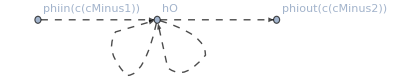

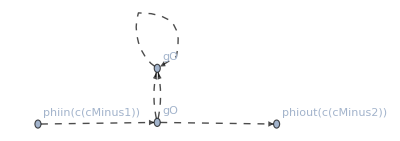

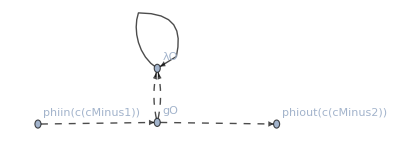

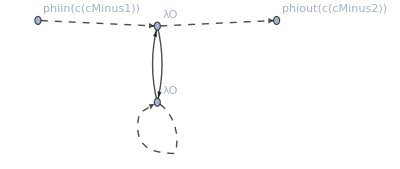

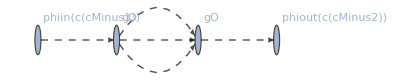

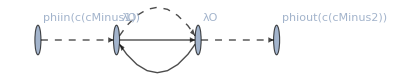

{Null,Null,Null,Null,Null,Null}

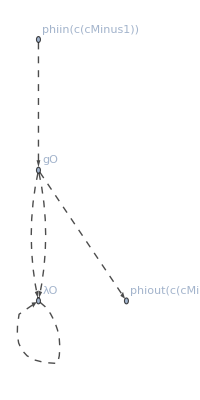

```mathematica
Print@*makeGraph/@justGraphStructure
```

```mathematica
Graph[{{UndirectedEdge[c1,c1,ϕ],UndirectedEdge[c1,c1,ϕ]}}]
```

Graph[(c1c1ϕ | c1c1ϕ)]

```mathematica
gotThemOut/.insertionsWithSubs//DiracChainJoin//FullSimplify
```

{(ⅈ h hO({c(cMinus1),c(cMinus2),c(c1),c(c2),c(c3),c(c4)}) ((ct (dZmϕ2 m^2-dZϕ2 k1^2))/(k1^2-m^2)+1) ((ct (dZmϕ2 m^2-dZϕ2 k2^2))/(k2^2-m^2)+1) phidelta({c(c1),c(c2)}) phidelta({c(c3),c(c4)}))/(8 (k1^2-m^2) (k2^2-m^2)),1/(4 (k1^2-m^2)^2 (k2^2-m^2))ⅈ g^2 gO({c(c2),c(c4),c(c5),c(c6)}) gO({c(cMinus1),c(cMinus2),c(c1),c(c3)}) ((ct (dZmϕ2 m^2-dZϕ2 k1^2))/(k1^2-m^2)+1) ((ct (dZmϕ2 m^2-dZϕ2 k1^2))/(k1^2-m^2)+1) ((ct (dZmϕ2 m^2-dZϕ2 k2^2))/(k2^2-m^2)+1) phidelta({c(c1),c(c2)}) phidelta({c(c3),c(c4)}) phidelta({c(c5),c(c6)}),1/(2 (k1^2-m^2)^2 (k2^2-M^2))g λ ((ct tr((M+γ·k2).(ⅈ dZψ2 γ·k2-ⅈ dZMψ2 M).(M+γ·k2)))/(k2^2-M^2)-ⅈ tr(M+γ·k2)) gO({c(cMinus1),c(cMinus2),c(c1),c(c3)}) ((ct (dZmϕ2 m^2-dZϕ2 k1^2))/(k1^2-m^2)+1) ((ct (dZmϕ2 m^2-dZϕ2 k1^2))/(k1^2-m^2)+1) phidelta({c(c1),c(c2)}) phidelta({c(c3),c(c4)}) psidelta({c(c5),c(c6)}) λO({c(c6),c(c5),c(c2),c(c4)}),1/(2 (k2^2-m^2))λ^2 (1/(k1^2-M^2))^2 ((ct (2 tr((M+γ·k1).(M+γ·k1).(ⅈ dZψ2 γ·k1-ⅈ dZMψ2 M).(M+γ·k1))+(ⅈ ct tr((M+γ·k1).(ⅈ dZψ2 γ·k1-ⅈ dZMψ2 M).(M+γ·k1).(M+γ·k1).(ⅈ dZψ2 γ·k1-ⅈ dZMψ2 M).(M+γ·k1)))/(k1^2-M^2)))/(k1^2-M^2)-ⅈ tr((M+γ·k1).(M+γ·k1))) ((ct (dZmϕ2 m^2-dZϕ2 k2^2))/(k2^2-m^2)+1) phidelta({c(c5),c(c6)}) psidelta({c(c1),c(c2)}) psidelta({c(c3),c(c4)}) λO({c(c2),c(c3),c(c5),c(c6)}) λO({c(c4),c(c1),c(cMinus1),c(cMinus2)}),1/(6 (k1^2-m^2) (k2^2-m^2) ((k1+k2-p)^2-m^2))ⅈ g^2 gO({c(cMinus1),c(c1),c(c3),c(c5)}) gO({c(cMinus2),c(c2),c(c4),c(c6)}) ((ct (dZmϕ2 m^2-dZϕ2 k1^2))/(k1^2-m^2)+1) ((ct (dZmϕ2 m^2-dZϕ2 k2^2))/(k2^2-m^2)+1) ((ct (dZmϕ2 m^2-dZϕ2 (k1+k2-p)^2))/((k1+k2-p)^2-m^2)+1) phidelta({c(c1),c(c2)}) phidelta({c(c3),c(c4)}) phidelta({c(c5),c(c6)}),1/((k1^2-M^2) (k2^2-M^2) ((k1+k2-p)^2-m^2))λ^2 (-ⅈ tr((M-γ·k1).(M+γ·k2))+(ct tr((M+γ·k2).(M-γ·k1).(-ⅈ (dZMψ2 M+dZψ2 γ·k1)).(M-γ·k1)))/(k1^2-M^2)+(ct (tr((M-γ·k1).(M+γ·k2).(ⅈ dZψ2 γ·k2-ⅈ dZMψ2 M).(M+γ·k2))+(ⅈ ct tr((M-γ·k1).(-ⅈ (dZMψ2 M+dZψ2 γ·k1)).(M-γ·k1).(M+γ·k2).(-ⅈ (dZMψ2 M-dZψ2 γ·k2)).(M+γ·k2)))/(k1^2-M^2)))/(k2^2-M^2)) ((ct (dZmϕ2 m^2-dZϕ2 (k1+k2-p)^2))/((k1+k2-p)^2-m^2)+1) phidelta({c(c1),c(c2)}) psidelta({c(c3),c(c4)}) psidelta({c(c5),c(c6)}) λO({c(c4),c(c5),c(cMinus2),c(c2)}) λO({c(c6),c(c3),c(cMinus1),c(c1)})}

```mathematica
mapRemoveIndexStructure=(#[__]->1 &/@ {phidelta, psidelta, gO, λO,hO});
groupIntoGenTopologies[fetchFCish_]:=Association@MapIndexed[generalisedTopo[#2[[1]]]->Association[#1]&,Split[fetchFCish,(#2[[2,1]]=!=nt[1])&]]

keepCTToThisOrder=(*key is nLoops*)<|5->0,4->0,3->0,2->1, 1->2,0->5|>;
keepCTToOrder[expr_,CTorder_Integer]:=Module[{output,ord},
If[CTorder === 0,
output=expr/.ct->0;
,
output =Normal@Series[expr, {ct,0,CTorder}];
];
output
];
analyzeSingleGenTopo[assocOfDiagsInGenTopo_Association,nLoops_Integer]:=Module[{},
symFacs = #[[2]]&/@assocOfDiagsInGenTopo; 
(*The following Times just maps sf[fermion, frac]->fermion*frac*)
evaluationsNextToJustIndexStructure ={(Times@@(#[[2]]))*(#[[3]]/.insertionsWithSubs),#[[3]]/.insertionsForGraph}&/@assocOfDiagsInGenTopo; 

fetchContractionStructureFromList[thisStructure_List]:=Module[{thisAmp,theseDeltas},
thisAmp=thisStructure/.ext[__]->Nothing/.killExternals;
theseDeltas =Cases[thisAmp,phidelta[__]|psidelta[__],Infinity];
thisAmp/.Thread[theseDeltas->Nothing]/.(#[[1,1]]->#[[1,2]]&/@theseDeltas)
];

externals=Union@Cases[evaluationsNextToJustIndexStructure[[1]], ext[__],Infinity];
killExternals =#[[1,1]]->e&/@externals;

evaluationAndContractionStructure ={DiracChainJoin@keepCTToOrder[#[[1]] /.mapRemoveIndexStructure,orderInCT ], fetchContractionStructureFromList[(List@@#[[2]])]}&/@ evaluationsNextToJustIndexStructure;

$Assumptions={(λo|dZλo)∈Arrays[{n,n,n,n}, Reals,{Symmetric[{1,2}],Symmetric[{3,4}]}],(go|dZgo)∈Arrays[{n,n,n,n}, Reals,Symmetric[{1,2,3,4}]],(ho|dZho)∈Arrays[{n,n,n,n,n,n}, Reals,Symmetric[{1,2,3,4,5,6}]]};
(*$Assumptions={λo∈Arrays[{n,n,n,n}, Reals],go∈Arrays[{n,n,n,n}, Reals],ho∈Arrays[{n,n,n,n,n,n}, Reals]}*)

getTensorContractionWithForgottenExternals[currentVersion_List]:=Module[{thisOne, tP, indices, contractedOnes, contractionRules},
tP=( TensorProduct@@currentVersion)/.{λO[__]->λo, gO[__]->go,hO[__]->ho};

indices=Flatten[First/@currentVersion];
contractedOnes =Union@Cases[indices,c[_]];
contractionRules =First/@Position[indices, #,{1}]&/@contractedOnes;
TensorContract[tP,contractionRules]//TensorReduce
];

getTensorStruct=GroupBy[evaluationAndContractionStructure, getTensorContractionWithForgottenExternals[#[[2]]]&];

getTensorStruct
]
```

```mathematica
done=stdQGCreateAmp[2,{"phi[p1]", "phi[p2]", "phi[p3]"}->{"phi[q1]","phi[q2]","phi[q3]"}];
fetchFCish =QGConvertToFC[done[[1]],DiracChainJoin->False];
fetchFCish[[1]]
(*The information generated by <new_topology> specifies whether or not the topology of
the current diagram differs from the topology of the preceding (output) diagram; it produces
a 1 when they differ, and a 0 in the opposite case (and for the first diagram, it produces a
1). Note that the ‘topology’ of a diagram is independent of the arrangement of the external
fields.*)

groupedIntoGenTopologies=groupIntoGenTopologies[fetchFCish];
analyzeSingleGenTopo[groupedIntoGenTopologies[[2]],2];
```

2

Part::partw: Part 2 of <|generalisedTopo(1)→Association[{2}]|> does not exist.

```mathematica
(*groupedIntoGenTopologies[[-1]]*)
```

```mathematica
results =EchoTiming@ParallelMap[analyzeSingleGenTopo[#,2]&,groupedIntoGenTopologies];
```

22.8223

```mathematica
(*
results[[1]]*)
```

```mathematica
Values[Length/@#]&/@results
```

<|generalisedTopo(1)→{15},generalisedTopo(2)→{10},generalisedTopo(3)→{15,15},generalisedTopo(4)→{15,15},generalisedTopo(5)→{15,15},generalisedTopo(6)→{60},generalisedTopo(7)→{45},generalisedTopo(8)→{45},generalisedTopo(9)→{45,45,90},generalisedTopo(10)→{45,45,90},generalisedTopo(11)→{45,180,90},generalisedTopo(12)→{90,90,180}|>

```mathematica
Keys[results[[-1]][[{-1}]]]/.getVisualOutput
```

ReplaceAll::reps: {getVisualOutput} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{λo⊗λo⊗λo⊗λo}/.getVisualOutput

```mathematica
Length@Union@FullSimplify@Values[First/@results[[-1]][[-1]]]
```

4

```mathematica
Length/@groupedIntoGenTopologies
```

<|generalisedTopo(1)→15,generalisedTopo(2)→10,generalisedTopo(3)→30,generalisedTopo(4)→30,generalisedTopo(5)→30,generalisedTopo(6)→60,generalisedTopo(7)→45,generalisedTopo(8)→45,generalisedTopo(9)→180,generalisedTopo(10)→180,generalisedTopo(11)→315,generalisedTopo(12)→360|>

```mathematica
runForExtSymmetricPoint[{head_Symbol,nLoops_Integer},listOfAmps_List]:=Module[{andConv,fetchFCish,fullInsertions, removedIndexStructure, justGraphStructure,keepToOrder,groupedIntoGenTopologies,andConvAllCt,symFacs,simplified,traces,renoPoint,diracedUp,prepped, internalMomenta,fcMLTID,appliedDiracSimplifyAgain, tracesSecondTime, withSymmetryFactors,uniqs, justUniqueDiags,uniqueDiagsLoopExtracted,justBadBits,justFinalBitsContainingLIs,justLoops, justLoopsDuped,equalDiagsGrouped,representativeDiagrams,mapDWSFToRepresentative,mapAllToSomething,testRun},

renoPoint=renormalisationPoints[head];
fetchFCish =QGConvertToFC[listOfAmps[[1]],DiracChainJoin->False];(*Form List[1->QG...., 2->QG...]*)

Print[ {head,nLoops} ->renoPoint, ". There are ", Length[fetchFCish], " diagrams."];
groupedIntoGenTopologies=groupIntoGenTopologies[fetchFCish];
analyzedAllTopos = analyzeSingleGenTopo /@groupedIntoGenTopologies;
(*symFacs = Association[#[[1]]->#[[2,2]]&/@fetchFCish]; (*Form List[1->sf[-1, 1/4],...., 2->...]*)*)



fullInsertions =(fetchFCish/.insertionsWithSubs);(*Form List[1->freeDiracIndices...., 2->QG...]*)
removedIndexStructure =fullInsertions /.mapRemoveIndexStructure;

If[nLoops >2,
andConv=removedIndexStructure/.ct->0;
,
Print["    ","Keeping to order ", keepToOrder];
andConv =Normal[Simplify[Series[#, {ct,0,keepToOrder[nLoops]}]],Series]& /@ removedIndexStructure;
];



diracedUp=andConv//DiracChainJoin;

justGraphStructure=List@@Simplify[((#/.insertionsForGraph)/(#/.killAllToJustSF)) ]&/@fetchFCish;



(*Print["    ","Running firstDiracSimplify:"];
simplified=DiracSimplify[diracedUp(* breaks ordering. DOT[Spinor[__], b___, Spinor[__]]->b *)/.Spinor[a__]->1/.renoPoint (*/.DiracTrace[inside_]->DiracTrace[inside, TraceOfOne->gammaMatrixDim]*), DiracTrace->True (*Simplify inside DiracTrace*),DiracTraceEvaluate->False (*But do not evaluate it*),SirlinSimplify->False,InsideDiracTrace->False]//FCTraceExpand;
traces = Union[Cases[simplified, DiracTrace[__],Infinity]];

Print["    ","Applying traceRules to the ", Length[traces], " traces"];
prepped = simplified/.traceRules;
internalMomenta=Sort@DeleteCases[Union@Cases[prepped, Momentum[mom_, D]->mom, Infinity], Except[k1|k2|k3|k3|k4|k5|k6|k7|k8|k9|k10]];
Print["    ","Internal momenta detected are: ",internalMomenta];
fcMLTID = FCMultiLoopTID[#, internalMomenta, FDS->False,ApartFF->False, DiracSimplify->False, Dimension->D]&/@prepped;

Print["    ","Applying DiracSimplify again after tensor integral decomposition"];
appliedDiracSimplifyAgain = FDS@(FCTraceFactor[DiracSimplify[#, DiracTrace->True (*Simplify inside DiracTrace*) ,DiracTraceEvaluate->False(*But do not evaluate it*),SirlinSimplify->False,InsideDiracTrace->False (*not working inside DiracTrace*)]] /.traceRules) &/@ fcMLTID;
(*GroupBy[(*all the same*)]*)
tracesSecondTime= Union[Cases[appliedDiracSimplifyAgain, DiracTrace[__],Infinity]];
Print["    ","Remaining traces: ",Short[ tracesSecondTime,5]];
withSymmetryFactors =Association[Simplify@MapThread[diagWithSF[head,nLoops, #2]->#1&, {appliedDiracSimplifyAgain, Range@Length[appliedDiracSimplifyAgain]}]];

uniqs =GroupBy[withSymmetryFactors, Identity]; (*GroupBy[assoc,f] gives an association whose keys are the distinct f[elemi] and whose values are subassociations of the association assoc.*)
Print["    ","Reduction in diagram count due to overlap between diagrams: ",
				 Length[withSymmetryFactors] ->Length[uniqs]];

equalDiagsGrouped = Values[Keys/@uniqs];
representativeDiagrams = First/@equalDiagsGrouped;
mapDWSFToRepresentative= Join@@Map[Thread[# -> First[#]] &, equalDiagsGrouped];

justUniqueDiags=Keys[uniqs];
Assert[justUniqueDiags === (withSymmetryFactors/@representativeDiagrams)];

uniqueDiagsLoopExtracted=AssociationMap[FCLoopExtract[#, internalMomenta, loopIntegral, PaVe->False, MultiLoop->False,FCLoopSplit->{2,3},FCLoopBasisSplit->True, FCI->True,FCLoopIBPReducableQ->False]&,justUniqueDiags];
(*"MultiLoop is an option for FCLoopIsolate. When set to True, FCLoopIsolate will
isolate only such loop integrals, that depend on all of the given loop
momenta. Integrals that depend only on some of the loop momenta will be
treated as non-loop terms and remain non-isolated.";*)

justBadBits=First/@uniqueDiagsLoopExtracted;
justFinalBitsContainingLIs=#[[2]]&/@uniqueDiagsLoopExtracted;
Print["    ","Are there no bad bits: ", Union[Values[justBadBits]] ==={0}];

justLoopsDuped =Join@@Values[#[[3]] &/@uniqueDiagsLoopExtracted];
justLoops =Union[justLoopsDuped];
Print["    ","Reduction in loopIntegrals count due to overlap between loopIntegrals: ", Length[justLoopsDuped] ->Length[justLoops]];

mapAllToSomething=((#*0) +something)& /@ justFinalBitsContainingLIs;
testRun= #/.mapAllToSomething &/@ withSymmetryFactors;
Assert[Union[Values[testRun]]=={something}];
(*Test that these really do replace all the right things*)

fetchContractionStructure[thisStructure_]:=Module[{thisAmp,theseDeltas},
thisAmp=thisStructure/.ext[__]->Nothing;
theseDeltas =Cases[thisAmp,phidelta[__]|psidelta[__],Infinity];
thisAmp/.Thread[theseDeltas->Nothing]/.(#[[1,1]]->#[[1,2]]&/@theseDeltas)
];
*)

Return@<|"loopIntsToDo"->justLoops,"diagsToEvaluate"->justFinalBitsContainingLIs,"diags"->withSymmetryFactors,"loopsExtracted"->uniqueDiagsLoopExtracted,"simpWithSF"->simplified, "traces"->{traces, tracesSecondTime}, "initialInserted"->diracedUp,"fromQG"->fetchFCish,"symFacs"->symFacs, "mapDWSFToRepresentative"->mapDWSFToRepresentative,"justStructure"->justGraphStructure,"contractionStructure"->(fetchContractionStructure/@justGraphStructure)|>
];
```

```mathematica
groupedIntoGenTopologies[generalisedTopo[2]]
```

<|2→{nt(1),sf(1,1),QGPolarization(phi(-1,p1),m) QGPolarization(phi(-2,q1),m) QGPolarization(psi(-3,p2),M) QGPolarization(psi(-4,q2),M) QGPropagator(psi(3,k1),psibar(4,-k1),M) QGPropagator(psi(7,-k2),psibar(8,k2),M) QGPropagator(phi(1,k1-p1-p2),phi(2,-k1+p1+p2),m) QGPropagator(phi(5,k2+q1+q2),phi(6,-k2-q1-q2),m) QGVertex(psibar(4,-k1),psi(-3,p2),phi(-1,p1),phi(1,k1-p1-p2)) QGVertex(psibar(-4,-q2),psi(7,-k2),phi(-2,-q1),phi(5,k2+q1+q2)) QGVertex(psibar(8,k2),psi(3,k1),phi(2,-k1+p1+p2),phi(6,-k2-q1-q2))},3→{nt(0),sf(1,1/4),QGPropagator(phi(3,-k1),phi(4,k1),m) QGPropagator(phi(7,-k2),phi(8,k2),m) QGPolarization(phi(-1,p1),m) QGPolarization(phi(-2,q1),m) QGPolarization(psi(-3,p2),M) QGPolarization(psi(-4,q2),M) QGVertex(phi(-1,p1),phi(-2,-q1),phi(1,k1-p1+q1),phi(3,-k1)) QGPropagator(phi(1,k1-p1+q1),phi(2,-k1+p1-q1),m) QGPropagator(phi(5,k2-p2+q2),phi(6,-k2+p2-q2),m) QGVertex(psibar(-4,-q2),psi(-3,p2),phi(5,k2-p2+q2),phi(7,-k2)) QGVertex(phi(2,-k1+p1-q1),phi(4,k1),phi(6,-k2+p2-q2),phi(8,k2))},4→{nt(0),sf(-1,1/2),QGPropagator(phi(7,-k2),phi(8,k2),m) QGPolarization(phi(-1,p1),m) QGPolarization(phi(-2,q1),m) QGPolarization(psi(-3,p2),M) QGPolarization(psi(-4,q2),M) QGPropagator(psi(3,k1),psibar(4,-k1),M) QGPropagator(phi(5,k2-p2+q2),phi(6,-k2+p2-q2),m) QGPropagator(psi(1,k1-p1+q1),psibar(2,-k1+p1-q1),M) QGVertex(psibar(4,-k1),psi(1,k1-p1+q1),phi(-1,p1),phi(-2,-q1)) QGVertex(psibar(-4,-q2),psi(-3,p2),phi(5,k2-p2+q2),phi(7,-k2)) QGVertex(psibar(2,-k1+p1-q1),psi(3,k1),phi(6,-k2+p2-q2),phi(8,k2))},5→{nt(0),sf(1,1),QGPolarization(phi(-1,p1),m) QGPolarization(phi(-2,q1),m) QGPolarization(psi(-3,p2),M) QGPolarization(psi(-4,q2),M) QGPropagator(psi(3,-k1),psibar(4,k1),M) QGPropagator(psi(7,k2),psibar(8,-k2),M) QGPropagator(phi(1,k1-p1+q2),phi(2,-k1+p1-q2),m) QGPropagator(phi(5,k2-p2+q1),phi(6,-k2+p2-q1),m) QGVertex(psibar(-4,-q2),psi(3,-k1),phi(-1,p1),phi(1,k1-p1+q2)) QGVertex(psibar(8,-k2),psi(-3,p2),phi(-2,-q1),phi(5,k2-p2+q1)) QGVertex(psibar(4,k1),psi(7,k2),phi(2,-k1+p1-q2),phi(6,-k2+p2-q1))}|>

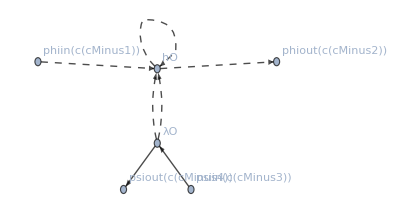

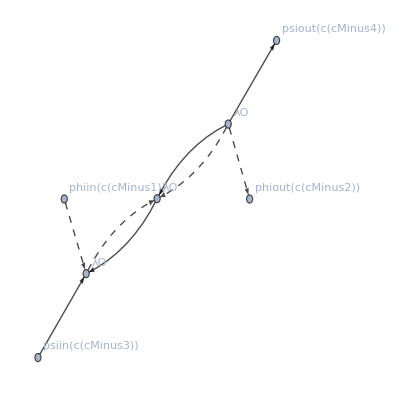

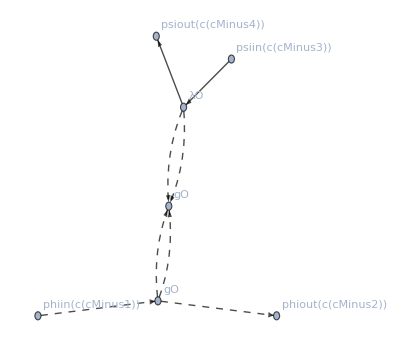

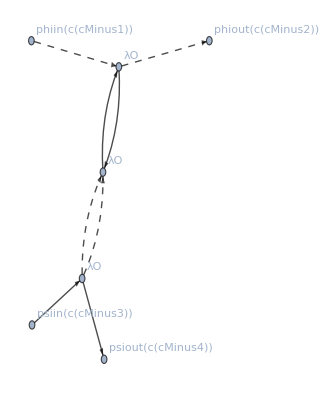

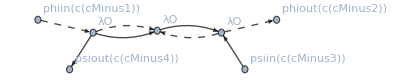

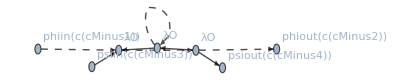

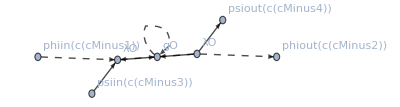

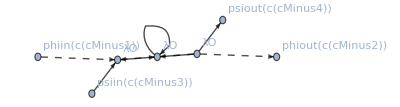

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Print@*makeGraph/@allResults[{λ,2}]["justStructure"]
```

```mathematica
results = {ϕϕ,2}->runFinal[{ϕϕ,2},done];
```

Warning! Some insertion rules are missing.

{ϕϕ,2}→{}. There are 6 diagrams.

Keeping to order <|5→0,4→0,3→0,2→1,1→2,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 5 traces

Internal momenta detected are: {k1,k2}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 6→6

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 58→48

```mathematica
results
```

{ϕϕ,2}→<|loopIntsToDo→{loopIntegral(1/(k1^2-m^2),{k1}),loopIntegral(1/(k2^2-m^2),{k2}),loopIntegral(1/(k2^2-M^2),{k2}),43,loopIntegral((k2·p)/((k1^2-M^2).(k2^2-M^2).((k1+k2-p)^2-m^2)^2),{k1,k2}),loopIntegral(((k1·k2) (k2·p))/((k1^2-M^2).(k2^2-M^2).((k1+k2-p)^2-m^2)^2),{k1,k2})},diagsToEvaluate→<|1|>,8,justStructure→1,contractionStructure→{{hO({c(cMinus1),c(cMinus2),c(c2),c(c2),c(c4),c(c4)})},{gO({c(c2),c(c4),c(c6),c(c6)}),gO({c(cMinus1),c(cMinus2),c(c2),c(c4)})},3,{λO({c(c4),c(c6),c(cMinus2),c(c2)}),λO({c(c6),c(c4),c(cMinus1),c(c2)})}}|>
 |  |  |  |

```mathematica
stdQGCreateAmp[nLoops_,input_]:=QGCreateAmp[nLoops,input,QGLoopMomentum->k,QGModel->"3dFull446",QGOptions->{"onepi","notadpole"},QGShowOutput->False,QGAmplitudeStyle->"./feyncalcWithTop.sty"];
makePhiPhi[nLoops_]:=Module[{done,results},
 done=stdQGCreateAmp[nLoops,{"phi[p]"}->{"phi[p]"}];
results = {ϕϕ,nLoops}->runFinal[{ϕϕ,nLoops},done];
PutAppend[results,"/tmp/3dFull446.out"];
results
];
makePsiPsi[nLoops_]:=Module[{done,results}, 
 done=stdQGCreateAmp[nLoops,{"psi[p]"}->{"psi[p]"}];
results = {ψψb,nLoops}->runFinal[{ψψb,nLoops},done];
PutAppend[results,"/tmp/3dFull446.out"];
results
];

makeLam[nLoops_]:=Module[{done,results},
 done=stdQGCreateAmp[nLoops,{"phi[p1]", "psi[p2]"}->{"phi[q1]","psi[q2]"}];
results = {λ,nLoops}->runFinal[{λ,nLoops},done];
PutAppend[results,"/tmp/3dFull446.out"];
results
];
makeg[nLoops_]:=Module[{done,results},
 done=stdQGCreateAmp[nLoops,{"phi[p1]", "phi[p2]"}->{"phi[q1]","phi[q2]"}];
results = {g,nLoops}->runFinal[{g,nLoops},done];
PutAppend[results,"/tmp/3dFull446.out"];
results
];
makeh[nLoops_]:=Module[{done,results},
 done=stdQGCreateAmp[nLoops,{"phi[p1]", "phi[p2]", "phi[p3]"}->{"phi[q1]","phi[q2]","phi[q3]"}];
results = {h,nLoops}->runFinal[{h,nLoops},done];
PutAppend[results,"/tmp/3dFull446.out"];
results
];
```

```mathematica
traceRules={DiracTrace[1] -> Tr1s, DiracTrace[DiracGamma[Momentum[k1_, D], D]] -> 0,  DiracTrace[DiracGamma[Momentum[mom1_, D], D] . DiracGamma[Momentum[mom2_, D], D]] -> Tr1s*Pair[Momentum[mom1, D], Momentum[mom2, D]],(*DiracTrace[DiracGamma[Momentum[mom1_, D], D] . DiracGamma[Momentum[mom2_, D], D] . DiracGamma[Momentum[mom3_, D], D]] -> 2*Tr3[Momentum[mom1, D], Momentum[mom2, D], Momentum[mom3, D]],*)DiracTrace[DiracGamma[Momentum[mom1_, D], D] . DiracGamma[Momentum[mom2_, D], D] . DiracGamma[Momentum[mom3_, D], D] . DiracGamma[Momentum[mom4_, D], D]] -> 2*DiracTrace[DiracGamma[Momentum[mom1, D], D] . DiracGamma[Momentum[mom2, D], D] . DiracGamma[Momentum[mom3, D], D] . DiracGamma[Momentum[mom4, D], D], DiracTraceEvaluate->True, TraceOfOne->Tr1s],
DiracTrace[DiracGamma[LorentzIndex[arb_,D],D]]->0 (*This can come from kslash Tr[kslash^3] -> gamm_mu Tr[gamm^mu] k^2*)}
renormalisationPoints=<|ϕϕ->{},ψψb->{},λ->{p1->0,p2->0,q1->0,q2->0},g->{p1->0,p2->0,q1->0,q2->0},h->{p1->0,p2->0,p3->0,q1->0,q2->0,q3->0}|>
runFinal[{head_Symbol,nLoops_Integer},listOfAmps_List]:=Module[{andConv,fetchFCish,fullInsertions, removeIndexStructure, justGraphStructure,keepToOrder,andConvAllCt,symFacs,simplified,traces,renoPoint,diracedUp,prepped, internalMomenta,fcMLTID,appliedDiracSimplifyAgain, tracesSecondTime, withSymmetryFactors,uniqs, justUniqueDiags,uniqueDiagsLoopExtracted,justBadBits,justFinalBitsContainingLIs,justLoops, justLoopsDuped,equalDiagsGrouped,representativeDiagrams,mapDWSFToRepresentative,mapAllToSomething,testRun},

renoPoint=renormalisationPoints[head];
fetchFCish =QGConvertToFC[listOfAmps[[1]],DiracChainJoin->True];
symFacs = fetchFCish/.killAllToJustSF; 
Print[ {head,nLoops} ->renoPoint, ". There are ", Length[symFacs], " diagrams."];

keepToOrder=(*key is nLoops*)<|5->0,4->0,3->0,2->1, 1->2,0->5|>;
fullInsertions =fetchFCish/.insertionsWithSubs;
removeIndexStructure =fullInsertions /.(#[__]->1 &/@ {phidelta, psidelta, gO, λO,hO});

If[nLoops >2,
andConv=removeIndexStructure/.ct->0;
,
Print["    ","Keeping to order ", keepToOrder];
andConv =Normal[Simplify[Series[#, {ct,0,keepToOrder[nLoops]}]],Series]& /@ removeIndexStructure;
];



diracedUp=andConv//DiracChainJoin;

justGraphStructure=List@@Simplify[((#/.insertionsForGraph)/(#/.killAllToJustSF)) ]&/@fetchFCish;



Print["    ","Running firstDiracSimplify:"];
simplified=DiracSimplify[diracedUp(* breaks ordering. DOT[Spinor[__], b___, Spinor[__]]->b *)/.Spinor[a__]->1/.renoPoint (*/.DiracTrace[inside_]->DiracTrace[inside, TraceOfOne->gammaMatrixDim]*), DiracTrace->True (*Simplify inside DiracTrace*),DiracTraceEvaluate->False (*But do not evaluate it*),SirlinSimplify->False,InsideDiracTrace->False]//FCTraceExpand;
traces = Union[Cases[simplified, DiracTrace[__],Infinity]];

Print["    ","Applying traceRules to the ", Length[traces], " traces"];
prepped = simplified/.traceRules;
internalMomenta=Sort@DeleteCases[Union@Cases[prepped, Momentum[mom_, D]->mom, Infinity], Except[k1|k2|k3|k3|k4|k5|k6|k7|k8|k9|k10]];
Print["    ","Internal momenta detected are: ",internalMomenta];
fcMLTID = FCMultiLoopTID[#, internalMomenta, FDS->False,ApartFF->False, DiracSimplify->False, Dimension->D]&/@prepped;

Print["    ","Applying DiracSimplify again after tensor integral decomposition"];
appliedDiracSimplifyAgain = FDS@(FCTraceFactor[DiracSimplify[#, DiracTrace->True (*Simplify inside DiracTrace*) ,DiracTraceEvaluate->False(*But do not evaluate it*),SirlinSimplify->False,InsideDiracTrace->False (*not working inside DiracTrace*)]] /.traceRules) &/@ fcMLTID;
(*GroupBy[(*all the same*)]*)
tracesSecondTime= Union[Cases[appliedDiracSimplifyAgain, DiracTrace[__],Infinity]];
Print["    ","Remaining traces: ",Short[ tracesSecondTime,5]];
withSymmetryFactors =Association[Simplify@MapThread[diagWithSF[head,nLoops, #2]->#1&, {appliedDiracSimplifyAgain, Range@Length[appliedDiracSimplifyAgain]}]];

uniqs =GroupBy[withSymmetryFactors, Identity]; (*GroupBy[assoc,f] gives an association whose keys are the distinct f[elemi] and whose values are subassociations of the association assoc.*)
Print["    ","Reduction in diagram count due to overlap between diagrams: ",
				 Length[withSymmetryFactors] ->Length[uniqs]];

equalDiagsGrouped = Values[Keys/@uniqs];
representativeDiagrams = First/@equalDiagsGrouped;
mapDWSFToRepresentative= Join@@Map[Thread[# -> First[#]] &, equalDiagsGrouped];

justUniqueDiags=Keys[uniqs];
Assert[justUniqueDiags === (withSymmetryFactors/@representativeDiagrams)];

uniqueDiagsLoopExtracted=AssociationMap[FCLoopExtract[#, internalMomenta, loopIntegral, PaVe->False, MultiLoop->False,FCLoopSplit->{2,3},FCLoopBasisSplit->True, FCI->True,FCLoopIBPReducableQ->False]&,justUniqueDiags];
(*"MultiLoop is an option for FCLoopIsolate. When set to True, FCLoopIsolate will
isolate only such loop integrals, that depend on all of the given loop
momenta. Integrals that depend only on some of the loop momenta will be
treated as non-loop terms and remain non-isolated.";*)

justBadBits=First/@uniqueDiagsLoopExtracted;
justFinalBitsContainingLIs=#[[2]]&/@uniqueDiagsLoopExtracted;
Print["    ","Are there no bad bits: ", Union[Values[justBadBits]] ==={0}];

justLoopsDuped =Join@@Values[#[[3]] &/@uniqueDiagsLoopExtracted];
justLoops =Union[justLoopsDuped];
Print["    ","Reduction in loopIntegrals count due to overlap between loopIntegrals: ", Length[justLoopsDuped] ->Length[justLoops]];

mapAllToSomething=((#*0) +something)& /@ justFinalBitsContainingLIs;
testRun= #/.mapAllToSomething &/@ withSymmetryFactors;
Assert[Union[Values[testRun]]=={something}];
(*Test that these really do replace all the right things*)

fetchContractionStructure[thisStructure_]:=Module[{thisAmp,theseDeltas},
thisAmp=thisStructure/.ext[__]->Nothing;
theseDeltas =Cases[thisAmp,phidelta[__]|psidelta[__],Infinity];
thisAmp/.Thread[theseDeltas->Nothing]/.(#[[1,1]]->#[[1,2]]&/@theseDeltas)
];


Return@<|"loopIntsToDo"->justLoops,"diagsToEvaluate"->justFinalBitsContainingLIs,"diags"->withSymmetryFactors,"loopsExtracted"->uniqueDiagsLoopExtracted,"simpWithSF"->simplified, "traces"->{traces, tracesSecondTime}, "initialInserted"->diracedUp,"fromQG"->fetchFCish,"symFacs"->symFacs, "mapDWSFToRepresentative"->mapDWSFToRepresentative,"justStructure"->justGraphStructure,"contractionStructure"->(fetchContractionStructure/@justGraphStructure)|>
];
```

{tr(1)→Tr1s,tr(γ·k1_)→0,tr((γ·mom1_).(γ·mom2_))→Tr1s (mom1·mom2),tr((γ·mom1_).(γ·mom2_).(γ·mom3_).(γ·mom4_))→2 Tr1s ((mom1·mom4) (mom2·mom3)-(mom1·mom3) (mom2·mom4)+(mom1·mom2) (mom3·mom4)),tr(γ^arb_)→0}

<|ϕϕ→{},ψψb→{},λ→{p1→0,p2→0,q1→0,q2→0},g→{p1→0,p2→0,q1→0,q2→0},h→{p1→0,p2→0,p3→0,q1→0,q2→0,q3→0}|>

```mathematica
GroupBy[allResults[{g,4}]["simpWithSF"], Identity, Length]//Values//Length
```

968

```mathematica
GroupBy[allResults[{g,4}]["diags"], Identity, Length]//Values//Length
```

712

```mathematica
allResults=Association@ReadList["~/Downloads/3dFull446.out"];
```

```mathematica
allResults//Length
```

19

```mathematica
allResults//ByteCount
```

1091328704

```mathematica
Keys@allResults
```

(ϕϕ | 1
ϕϕ | 2
ϕϕ | 3
ϕϕ | 4
ψψb | 1
ψψb | 2
ψψb | 3
ψψb | 4
λ | 1
λ | 2
λ | 3
λ | 4
g | 1
g | 2
g | 3
g | 4
h | 1
h | 2
h | 3)

```mathematica
(*GroupBy[gam2[{h,2}]["diagsToEvaluateNoSFs"],Identity, Length]//Length*)
```

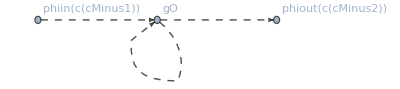

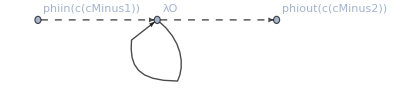

{Null,Null}

```mathematica
Print@*makeGraph/@phiphi2[{ϕϕ,2}]["justStructure"]
```

```mathematica
answers =allResults[{ϕϕ,2}]["contractionStructure"]
```

{{hO({c(cMinus1),c(cMinus2),c(c2),c(c2),c(c4),c(c4)})},{gO({c(c2),c(c4),c(c6),c(c6)}),gO({c(cMinus1),c(cMinus2),c(c2),c(c4)})},{gO({c(cMinus1),c(cMinus2),c(c2),c(c4)}),λO({c(c6),c(c6),c(c2),c(c4)})},{λO({c(c2),c(c4),c(c6),c(c6)}),λO({c(c4),c(c2),c(cMinus1),c(cMinus2)})},{gO({c(cMinus1),c(c2),c(c4),c(c6)}),gO({c(cMinus2),c(c2),c(c4),c(c6)})},{λO({c(c4),c(c6),c(cMinus2),c(c2)}),λO({c(c6),c(c4),c(cMinus1),c(c2)})}}

```mathematica
phiphi2 = Association[makePhiPhi/@Range[4] ]//EchoTiming;
psipsi2= Association[makePsiPsi/@Range[4]]//EchoTiming;
```

Warning! Some insertion rules are missing.

{ϕϕ,1}→{}. There are 2 diagrams.

Keeping to order <|5→0,4→0,3→0,2→1,1→2,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 2 traces

Internal momenta detected are: {k1}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 2→2

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 6→6

Warning! Some insertion rules are missing.

{ϕϕ,2}→{}. There are 6 diagrams.

Keeping to order <|5→0,4→0,3→0,2→1,1→2,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 5 traces

Internal momenta detected are: {k1,k2}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 6→6

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 58→48

Warning! Some insertion rules are missing.

{ϕϕ,3}→{}. There are 29 diagrams.

Running firstDiracSimplify:

Applying traceRules to the 16 traces

Internal momenta detected are: {k1,k2,k3}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 29→27

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 82→46

Warning! Some insertion rules are missing.

{ϕϕ,4}→{}. There are 193 diagrams.

Running firstDiracSimplify:

Applying traceRules to the 66 traces

Internal momenta detected are: {k1,k2,k3,k4}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 193→169

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 765→373

20.4669

Warning! Some insertion rules are missing.

{ψψb,1}→{}. There are 1 diagrams.

Keeping to order <|5→0,4→0,3→0,2→1,1→2,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 0 traces

Internal momenta detected are: {k1}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 1→1

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 3→3

Warning! Some insertion rules are missing.

{ψψb,2}→{}. There are 3 diagrams.

Keeping to order <|5→0,4→0,3→0,2→1,1→2,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 2 traces

Internal momenta detected are: {k1,k2}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 3→3

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 33→30

Warning! Some insertion rules are missing.

{ψψb,3}→{}. There are 14 diagrams.

Running firstDiracSimplify:

Applying traceRules to the 4 traces

Internal momenta detected are: {k1,k2,k3}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 14→14

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 41→23

Warning! Some insertion rules are missing.

{ψψb,4}→{}. There are 87 diagrams.

Running firstDiracSimplify:

Applying traceRules to the 14 traces

Internal momenta detected are: {k1,k2,k3,k4}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 87→87

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 409→204

11.3338

```mathematica
lam2 =Association[ makeLam/@Range[4] ]//EchoTiming;
gam2 =Association[ makeg/@Range[4]] //EchoTiming;
```

Warning! Some insertion rules are missing.

{λ,1}→{p1→0,p2→0,q1→0,q2→0}. There are 3 diagrams.

Keeping to order <|5→0,4→0,3→0,2→1,1→2,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 0 traces

Internal momenta detected are: {k1}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 3→2

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 14→14

Warning! Some insertion rules are missing.

{λ,2}→{p1→0,p2→0,q1→0,q2→0}. There are 25 diagrams.

Keeping to order <|5→0,4→0,3→0,2→1,1→2,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 5 traces

Internal momenta detected are: {k1,k2}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 25→15

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 167→134

Warning! Some insertion rules are missing.

{λ,3}→{p1→0,p2→0,q1→0,q2→0}. There are 258 diagrams.

Running firstDiracSimplify:

Applying traceRules to the 12 traces

Internal momenta detected are: {k1,k2,k3}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 258→127

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 376→207

Warning! Some insertion rules are missing.

{λ,4}→{p1→0,p2→0,q1→0,q2→0}. There are 2960 diagrams.

Running firstDiracSimplify:

Applying traceRules to the 45 traces

Internal momenta detected are: {k1,k2,k3,k4}

Tdec::slow: Tdec is computing a decomposition that is not available in TIDL. This might take quite some time. If this integral often appears in your computations, it is recommended to compute it once and then save the result to the TIDL directory.

General::stop: Further output of Tdec::slow will be suppressed during this calculation.

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 2960→1225

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 5620→3185

320.398

Warning! Some insertion rules are missing.

{g,1}→{p1→0,p2→0,q1→0,q2→0}. There are 7 diagrams.

Keeping to order <|5→0,4→0,3→0,2→1,1→2,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 2 traces

Internal momenta detected are: {k1}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 7→3

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 18→17

Warning! Some insertion rules are missing.

{g,2}→{p1→0,p2→0,q1→0,q2→0}. There are 57 diagrams.

Keeping to order <|5→0,4→0,3→0,2→1,1→2,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 5 traces

Internal momenta detected are: {k1,k2}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 57→13

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 123→90

Warning! Some insertion rules are missing.

{g,3}→{p1→0,p2→0,q1→0,q2→0}. There are 599 diagrams.

Running firstDiracSimplify:

Applying traceRules to the 16 traces

Internal momenta detected are: {k1,k2,k3}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 599→97

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 342→201

Warning! Some insertion rules are missing.

{g,4}→{p1→0,p2→0,q1→0,q2→0}. There are 7082 diagrams.

Running firstDiracSimplify:

Applying traceRules to the 61 traces

Internal momenta detected are: {k1,k2,k3,k4}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 7082→712

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 3506→1889

505.289

```mathematica
gam22 =Association[ EchoTiming[makeh[#]]&/@Range[2] ]//RuntimeTools`Profile;
```

Warning! Some insertion rules are missing.

{h,1}→{p1→0,p2→0,p3→0,q1→0,q2→0,q3→0}. There are 60 diagrams.

Keeping to order <|5→0,4→0,3→0,2→1,1→2,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 2 traces

Internal momenta detected are: {k1}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 60→3

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 21→18

11.5002

Warning! Some insertion rules are missing.

{h,2}→{p1→0,p2→0,p3→0,q1→0,q2→0,q3→0}. There are 1300 diagrams.

Keeping to order <|5→0,4→0,3→0,2→1,1→2,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 5 traces

Internal momenta detected are: {k1,k2}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 1300→22

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 277→216

423.222

```mathematica
hSextic3 =Association[  EchoTiming[makeh[#]]&/@Range[4] ];
```

Warning! Some insertion rules are missing.

{h,1}→{p1→0,p2→0,p3→0,q1→0,q2→0,q3→0}. There are 60 diagrams.

Keeping to order <|5→0,4→0,3→0,2→1,1→2,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 2 traces

Internal momenta detected are: {k1}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 60→3

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 21→18

6.81766

Warning! Some insertion rules are missing.

{h,2}→{p1→0,p2→0,p3→0,q1→0,q2→0,q3→0}. There are 1300 diagrams.

Keeping to order <|5→0,4→0,3→0,2→1,1→2,0→5|>

Running firstDiracSimplify:

Applying traceRules to the 5 traces

Internal momenta detected are: {k1,k2}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 1300→22

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 277→216

244.657

Warning! Some insertion rules are missing.

{h,3}→{p1→0,p2→0,p3→0,q1→0,q2→0,q3→0}. There are 25335 diagrams.

Running firstDiracSimplify:

Applying traceRules to the 16 traces

Internal momenta detected are: {k1,k2,k3}

Applying DiracSimplify again after tensor integral decomposition

Remaining traces: {}

Reduction in diagram count due to overlap between diagrams: 25335→223

Are there no bad bits: True

Reduction in loopIntegrals count due to overlap between loopIntegrals: 836→521

1252.83

Warning! Some insertion rules are missing.

{h,4}→{p1→0,p2→0,p3→0,q1→0,q2→0,q3→0}. There are 473055 diagrams.

Running firstDiracSimplify:

Applying traceRules to the 65 traces

Internal momenta detected are: {k1,k2,k3,k4}

```mathematica
$Assumptions={λo∈Arrays[{n,n,n,n}, Reals,{Symmetric[{1,2}],Symmetric[{3,4}]}],go∈Arrays[{n,n,n,n}, Reals,Symmetric[{1,2,3,4}]],ho∈Arrays[{n,n,n,n,n,n}, Reals,Symmetric[{1,2,3,4,5,6}]]}
(*$Assumptions={λo∈Arrays[{n,n,n,n}, Reals],go∈Arrays[{n,n,n,n}, Reals],ho∈Arrays[{n,n,n,n,n,n}, Reals]}*)
getTensorContractionButForgetExternal[currentVersion_List]:=Module[{thisOne, tP, indices, contractedOnes, contractionRules},
tP=( TensorProduct@@currentVersion)/.{λO[__]->λo, gO[__]->go,hO[__]->ho};
indices=Flatten[First/@currentVersion];
contractedOnes =Union@Cases[indices,c[_]];
contractionRules =First/@Position[indices, #,{1}]&/@contractedOnes;
TensorContract[tP,contractionRules]//TensorReduce
];

generateDirectGroupings[studyThis_Association]:=Module[{contractionStructures,externals, killExternals,groupDirect},
contractionStructures =Association@MapIndexed[#2[[1]](*diagramNumber*)->#1 &,Transpose[{studyThis["justStructure"],studyThis["contractionStructure"]}]];
externals=Union@Cases[contractionStructures[[1]], ext[__],Infinity];
killExternals =#[[1,1]]->e&/@externals;
groupDirect=GroupBy[contractionStructures,getTensorContractionButForgetExternal@Sort[#[[2]]/.killExternals]&];
Print["    ", killExternals,"    ", Length[contractionStructures]->Length[groupDirect]];
Return[groupDirect]
];
```

{λo∈Arrays[{n,n,n,n},ℝ,(Cycles[(1 | 2)] | 1
Cycles[(3 | 4)] | 1)],go∈Arrays[{n,n,n,n},ℝ,Symmetric[{1,2,3,4}]],ho∈Arrays[{n,n,n,n,n,n},ℝ,Symmetric[{1,2,3,4,5,6}]]}

```mathematica
(*
This is the code with which the above was developed:
studyThis=allResults[{h,2}];
contractionStructures =Association@MapIndexed[#2[[1]](*diagramNumber*)->#1 &,Transpose[{studyThis["justStructure"],studyThis["contractionStructure"]}]];

externals=Union@Cases[contractionStructures[[1]], ext[__],Infinity]
killExternals =#[[1,1]]->e&/@externals
indirectMethodMid=GroupBy[Sort[#[[2]]/.killExternals]&/@(contractionStructures),Identity];
doneIndirectMethod=getTensorContractionButForgetExternal/@Keys[indirectMethodMid];
Print[Length[contractionStructures]->Length[indirectMethodMid]->Length[Length/@GroupBy[doneIndirectMethod, Identity]]]

groupDirect=GroupBy[contractionStructures,getTensorContractionButForgetExternal@Sort[#[[2]]/.killExternals]&]//EchoTiming;
Length[groupDirect]
*)
```

```mathematica
studyThis=allResults[{h,2}];
Keys[allResults]
```

(ϕϕ | 1
ϕϕ | 2
ϕϕ | 3
ϕϕ | 4
ψψb | 1
ψψb | 2
ψψb | 3
ψψb | 4
λ | 1
λ | 2
λ | 3
λ | 4
g | 1
g | 2
g | 3
g | 4
h | 1
h | 2
h | 3)

```mathematica
allGroupDirects= EchoTiming@Map[EchoTiming@*generateDirectGroupings,allResults];
```

{c(cMinus1)→e,c(cMinus2)→e}    2→2

0.005241

{c(cMinus1)→e,c(cMinus2)→e}    6→6

0.004624

{c(cMinus1)→e,c(cMinus2)→e}    29→25

0.036253

{c(cMinus1)→e,c(cMinus2)→e}    193→148

0.200478

{c(cMinus1)→e,c(cMinus2)→e}    1→1

0.000812

{c(cMinus1)→e,c(cMinus2)→e}    3→3

0.003062

{c(cMinus1)→e,c(cMinus2)→e}    14→14

0.013388

{c(cMinus1)→e,c(cMinus2)→e}    87→87

0.091363

{c(cMinus1)→e,c(cMinus2)→e,c(cMinus3)→e,c(cMinus4)→e}    3→2

0.003161

{c(cMinus1)→e,c(cMinus2)→e,c(cMinus3)→e,c(cMinus4)→e}    25→17

0.021216

{c(cMinus1)→e,c(cMinus2)→e,c(cMinus3)→e,c(cMinus4)→e}    258→169

0.253308

{c(cMinus1)→e,c(cMinus2)→e,c(cMinus3)→e,c(cMinus4)→e}    2960→1802

3.42865

{c(cMinus1)→e,c(cMinus3)→e,c(cMinus2)→e,c(cMinus4)→e}    7→3

0.005167

{c(cMinus1)→e,c(cMinus3)→e,c(cMinus2)→e,c(cMinus4)→e}    57→13

0.046327

{c(cMinus1)→e,c(cMinus3)→e,c(cMinus2)→e,c(cMinus4)→e}    599→100

0.581813

{c(cMinus1)→e,c(cMinus3)→e,c(cMinus2)→e,c(cMinus4)→e}    7082→834

8.24665

{c(cMinus1)→e,c(cMinus3)→e,c(cMinus5)→e,c(cMinus2)→e,c(cMinus4)→e,c(cMinus6)→e}    60→3

0.053509

{c(cMinus1)→e,c(cMinus3)→e,c(cMinus5)→e,c(cMinus2)→e,c(cMinus4)→e,c(cMinus6)→e}    1300→27

1.20269

{c(cMinus1)→e,c(cMinus3)→e,c(cMinus5)→e,c(cMinus2)→e,c(cMinus4)→e,c(cMinus6)→e}    25335→289

27.998

44.9225

```mathematica
(*oldGroupDirect=groupDirect;*)
```

```mathematica
(*Length/@groupDirect*)
```

{λo∈Arrays[{n,n,n,n},ℝ,(Cycles[(1 | 2)] | 1
Cycles[(3 | 4)] | 1)],go∈Arrays[{n,n,n,n},ℝ,Symmetric[{1,2,3,4}]],ho∈Arrays[{n,n,n,n,n,n},ℝ,Symmetric[{1,2,3,4,5,6}]]}

```mathematica
currentGroup=allGroupDirects[[-2]][[-20]];
currentGroup[[1;;3]]
```

<|87→{{ext(phiin(c(cMinus1))),ext(phiin(c(cMinus3))),ext(phiin(c(cMinus5))),ext(phiout(c(cMinus2))),ext(phiout(c(cMinus4))),ext(phiout(c(cMinus6))),hO({c(cMinus5),c(cMinus2),c(cMinus4),c(cMinus6),c(c6),c(c8)}),phidelta({c(c5),c(c6)}),phidelta({c(c7),c(c8)}),psidelta({c(c1),c(c2)}),psidelta({c(c3),c(c4)}),λO({c(c2),c(c3),c(cMinus3),c(c7)}),λO({c(c4),c(c1),c(cMinus1),c(c5)})},{hO({c(cMinus5),c(cMinus2),c(cMinus4),c(cMinus6),c(c6),c(c8)}),λO({c(c2),c(c4),c(cMinus3),c(c8)}),λO({c(c4),c(c2),c(cMinus1),c(c6)})}},89→{{ext(phiin(c(cMinus1))),ext(phiin(c(cMinus3))),ext(phiin(c(cMinus5))),ext(phiout(c(cMinus2))),ext(phiout(c(cMinus4))),ext(phiout(c(cMinus6))),hO({c(cMinus3),c(cMinus2),c(cMinus4),c(cMinus6),c(c6),c(c8)}),phidelta({c(c5),c(c6)}),phidelta({c(c7),c(c8)}),psidelta({c(c1),c(c2)}),psidelta({c(c3),c(c4)}),λO({c(c2),c(c3),c(cMinus5),c(c7)}),λO({c(c4),c(c1),c(cMinus1),c(c5)})},{hO({c(cMinus3),c(cMinus2),c(cMinus4),c(cMinus6),c(c6),c(c8)}),λO({c(c2),c(c4),c(cMinus5),c(c8)}),λO({c(c4),c(c2),c(cMinus1),c(c6)})}},91→{{ext(phiin(c(cMinus1))),ext(phiin(c(cMinus3))),ext(phiin(c(cMinus5))),ext(phiout(c(cMinus2))),ext(phiout(c(cMinus4))),ext(phiout(c(cMinus6))),hO({c(cMinus3),c(cMinus5),c(cMinus4),c(cMinus6),c(c6),c(c8)}),phidelta({c(c5),c(c6)}),phidelta({c(c7),c(c8)}),psidelta({c(c1),c(c2)}),psidelta({c(c3),c(c4)}),λO({c(c2),c(c3),c(cMinus2),c(c7)}),λO({c(c4),c(c1),c(cMinus1),c(c5)})},{hO({c(cMinus3),c(cMinus5),c(cMinus4),c(cMinus6),c(c6),c(c8)}),λO({c(c2),c(c4),c(cMinus2),c(c8)}),λO({c(c4),c(c2),c(cMinus1),c(c6)})}}|>

```mathematica
here=Keys[currentGroup](*Flatten[Position[contractionStructures,#]&/@currentGroup]*);
Print[here->Length[here], " with different evaluations ", Length[Union[studyThis["simpWithSF"][[here]]]], " with SF " ,Union[studyThis["symFacs"][[here]]]];
```

{87,89,91,93,95,97,99,101,103,105,107,109,111,113,115}→15 with different evaluations 1 with SF {-1}

```mathematica
externals=Union@Cases[currentGroup[[1]], ext[__],Infinity];
killExternals =#[[1,1]]->e&/@externals;
getTensorStructureForThisStruct[thisOne_List]:=Module[{tP, indices,contractedOnes,contractionRules,contracted,freeOnesInGivenOrder,assignNumbers,correspondingPermutation},
tP=( TensorProduct@@thisOne)/.{λO[__]->λo, gO[__]->go,hO[__]->ho};
indices=Flatten[First/@thisOne];
contractedOnes =Union@Cases[indices/.killExternals,c[_]];
contractionRules =First/@Position[indices, #,{1}]&/@contractedOnes;
contracted =TensorContract[tP,contractionRules](*//TensorReduce*);

freeOnesInGivenOrder =DeleteCases[indices,Alternatives@@contractedOnes];
correspondingPermutation=FindPermutation[freeOnesInGivenOrder,Sort[freeOnesInGivenOrder]];
(*FindPermutation[expr1,expr2] gives a permutation that converts expr1 to expr2 for two expressions that differ only in the order of their arguments. We presently have an expression which is out of order; we must order them to become the new ones.*)

TensorTranspose[contracted,correspondingPermutation]//TensorReduce
];Print["May not work for λ!***************************************************"];
```

May not work for λ!***************************************************

```mathematica
currentGroup[[1]]
```

{{ext(phiin(c(cMinus1))),ext(phiin(c(cMinus3))),ext(phiin(c(cMinus5))),ext(phiout(c(cMinus2))),ext(phiout(c(cMinus4))),ext(phiout(c(cMinus6))),hO({c(cMinus5),c(cMinus2),c(cMinus4),c(cMinus6),c(c6),c(c8)}),phidelta({c(c5),c(c6)}),phidelta({c(c7),c(c8)}),psidelta({c(c1),c(c2)}),psidelta({c(c3),c(c4)}),λO({c(c2),c(c3),c(cMinus3),c(c7)}),λO({c(c4),c(c1),c(cMinus1),c(c5)})},{hO({c(cMinus5),c(cMinus2),c(cMinus4),c(cMinus6),c(c6),c(c8)}),λO({c(c2),c(c4),c(cMinus3),c(c8)}),λO({c(c4),c(c2),c(cMinus1),c(c6)})}}

```mathematica
eachTensored=getTensorStructureForThisStruct[#[[2]]]&/@currentGroup;
```

```mathematica
this = Total[eachTensored]//TensorReduce//FullSimplify;
```

```mathematica
(*this//TensorSymmetry does not work, so instead we just randomly test symmetries:*)
(TensorReduce[this-TensorTranspose[this,#]]===0 )&/@RandomChoice[Permutations[{1,2,3,4,5,6}],10]
```

{True,True,True,True,True,True,True,True,True,True}

```mathematica
(*Gamma matrices from the SUSY tensor model paper
aaas={{{0,-1},{1,0}}, {{0,1},{1,0}},{{1,0}, {0,-1}}}
aaas[[#]].aaas[[#]]&/@{1,2,3}*)
```

```mathematica
mySymmetrize[tensor_,listOfCycles:{{_Cycles,1}..}]:=Module[{expandTensor,group, order,tensorDimensions,listOfElements,symmetrised},
expandTensor=tensor//TensorExpand//EchoTiming;
group=PermutationGroup[First/@listOfCycles];
listOfElements=GroupElements[group];
tensorDimensions=TensorDimensions[expandTensor];
(*Print[tensorDimensions];*)
If[Length@Union[Permute[tensorDimensions,#]&/@listOfElements]!= 1, Print["Permuting illegal tensor dimensions in mySymmetrize: ", tensorDimensions, " asked to be permuted by ",listOfCycles ];
Abort[]
];(*Make sure we are not symmetrising over illegal dimensions*)
order=GroupOrder[group];
symmetrised=1/order Total[TensorTranspose[expandTensor,#]&/@listOfElements]//TensorReduce//EchoTiming;FullSimplify[symmetrised, TimeConstraint->{1,5}]
];
```

```mathematica
sym6 = {#, 1}&/@(SymmetricGroup[6]//GroupGenerators) (*Generators of the 6-symmetry group*)
```

(Cycles[(1 | 2)] | 1
Cycles[(1 | 2 | 3 | 4 | 5 | 6)] | 1)

```mathematica
this/((*(SymmetricGroup[6]//GroupOrder)/(4!*2)*)mySymmetrize[eachTensored[[1]], sym6]//TensorReduce)//FullSimplify
```

0.000891

0.470726

15

```mathematica
Keys[studyThis]
```

{loopIntsToDo,diagsToEvaluate,diags,loopsExtracted,simpWithSF,traces,initialInserted,fromQG,symFacs,mapDWSFToRepresentative,justStructure,contractionStructure}

```mathematica
analyzeGroup[groupWithSameStructureUpToExtperm_Association,studyThis_Association]:=Module[{whichDiagrams,allValues,eachTensored,tensorRank, allTensorsSummed,symGroup, numericalFactor,finalResult},
whichDiagrams=Keys[groupWithSameStructureUpToExtperm](*Flatten[Position[contractionStructures,#]&/@currentGroup]*);
allValues=Union[Values[studyThis["diags"][[whichDiagrams]]]];
If[Length[allValues]!= 1,Print["Same tensor structure but ", Length[Union@allValues], " different evaluations: panic"]; leakAllValues ={groupWithSameStructureUpToExtperm, allValues}; Abort[];];
Print[whichDiagrams->Length[whichDiagrams], " and so ",allValues, Union[studyThis["symFacs"][[whichDiagrams]]]];
eachTensored=getTensorStructureForThisStruct[#[[2]]]&/@groupWithSameStructureUpToExtperm;
tensorRank = TensorRank[eachTensored[[1]]];

allTensorsSummed = Total[eachTensored]//TensorReduce//FullSimplify[#, TimeConstraint->{0.1,0.5}]&; (*Don't really need to spend long on this, since we symmetrise later anyway*)
(*this//TensorSymmetry does not work, so instead we just randomly test symmetries:*)
Print["Check all true: ",(TensorReduce[allTensorsSummed-TensorTranspose[allTensorsSummed,#]]===0 )&/@RandomChoice[Permutations[Range@tensorRank],2]];

symGroup = {#, 1}&/@(SymmetricGroup[tensorRank]//GroupGenerators) (*Generators of the 6-symmetry group*);
(*numericalFactor2=allTensorsSummed/((*(SymmetricGroup[6]//GroupOrder)/(4!*2)*)mySymmetrize[eachTensored[[1]], symGroup]//TensorReduce)//FullSimplify;*)
numericalFactor=Length[eachTensored];
(*Print["Obtained: ",Short[numericalFactor], " vs ", Length[eachTensored]];*)
If[!IntegerQ[numericalFactor],Print["Not a symmetric tensor structure - panic!"]; Abort[];];
finalResult = fullContrib[numericalFactor ,eachTensored[[1]]/.getVisualOutput, fullSym[eachTensored[[1]],tensorRank],diag[allValues]];
Print["And hence ",finalResult];
finalResult
];
```

```mathematica
greekLetters=Alphabet["Greek"]
visualOutputOfSymmetrizedTensor[tensorNoTranspose_TensorContract]:=Module[{tensorUncontracted,contractionRules,fullRank, listifiedTensor,allLetters,allLettersFlat, tensorWithLetters, contractionMap},
(*tensorNoTranspose= tensor/.TensorTranspose[a_, b_]->a;
If[Head[tensorNoTranspose]!=TensorContract, Abort[];];*)
{tensorUncontracted, contractionRules}=List@@tensorNoTranspose;
fullRank = TensorRank[tensorUncontracted];
listifiedTensor=If[Head[tensorUncontracted]===Symbol, {tensorUncontracted} (*There's only one symbol*), (*else*)List@@tensorUncontracted];
allLetters=TakeList[greekLetters,TensorRank/@listifiedTensor];
allLettersFlat=Flatten[allLetters];
tensorWithLetters= MapThread[Subscript[#1, #2]&,{listifiedTensor,allLetters}];
contractionMap = allLettersFlat[[#[[2]]]]->allLettersFlat[[#[[1]]]]&/@contractionRules;
externalPoints = Complement[Range@TensorRank@tensorUncontracted, Flatten[contractionRules]];

externalMap = allLettersFlat[[#]]->Capitalize[allLettersFlat[[#]]]&/@externalPoints;
tensorWithLetters/.contractionMap/.externalMap
];getVisualOutput={TensorTranspose[a_,b_]:>visualOutputOfSymmetrizedTensor[a],TensorContract[a_,b_]:>visualOutputOfSymmetrizedTensor[TensorContract[a,b]]};
```

{α,β,γ,δ,ε,ζ,η,θ,ι,κ,λ,μ,ν,ξ,ο,π,ρ,σ,τ,υ,φ,χ,ψ,ω}

```mathematica
Keys[allGroupDirects[{g,1}]]
Keys[allGroupDirects[{g,1}]]/.getVisualOutput
```

{TensorContract[ho,(5 | 6)],TensorContract[go⊗go,(3 | 7
4 | 8)],TensorContract[λo⊗λo,(1 | 5
2 | 6)]}

{{ho_{Α,Β,Γ,Δ,ε,ε}},{go_{Α,Β,γ,δ},go_{Ε,Ζ,γ,δ}},{λo_{α,β,Γ,Δ},λo_{α,β,Η,Θ}}}

```mathematica
outputasd= analyzeGroup[groupDirect[[-1]], studyThis] (*//RuntimeTools`Profile*)
```

Part::partd: Part specification groupDirect⟦-1⟧ is longer than depth of object.

$Aborted[]

```mathematica
allLoopAndHeads = Keys@allGroupDirects
```

(ϕϕ | 1
ϕϕ | 2
ϕϕ | 3
ϕϕ | 4
ψψb | 1
ψψb | 2
ψψb | 3
ψψb | 4
λ | 1
λ | 2
λ | 3
λ | 4
g | 1
g | 2
g | 3
g | 4
h | 1
h | 2
h | 3)

```mathematica
allLoopAndHeads//InputForm
```

{{ϕϕ, 1}, {ϕϕ, 2}, {ϕϕ, 3}, {ϕϕ, 4}, {ψψb, 1}, {ψψb, 2}, {ψψb, 3}, {ψψb, 4}, {λ, 1}, {λ, 2}, {λ, 3}, {λ, 4}, {g, 1}, {g, 2}, {g, 3}, {g, 4}, {h, 1}, {h, 2}, {h, 3}}

```mathematica
doTheseLoopAndHeads={{ϕϕ,1},{ϕϕ,2},{ϕϕ,3},(*{ϕϕ,4}*){g,1},{g,2},{g,3}(*,{g,4},{h,1},{h,2},{h,3}*)}
```

(ϕϕ | 1
ϕϕ | 2
ϕϕ | 3
g | 1
g | 2
g | 3)

```mathematica
key ={ϕϕ,2}
```

{ϕϕ,2}

```mathematica
runKey[key_]:=Module[{onlySome, got},
Print["************* Running ", key , "******************"];
onlySome=KeySelect[allGroupDirects[key], FreeQ2[#, {ho, λo}]&];
Print[Keys@onlySome];
got=Map[analyzeGroup[#, allResults[key]]&,(*allGroupDirects[key]*)onlySome];
got/.allResults[key]["loopsExtracted"]
];
```

```mathematica
runKey[{g,1}]
```

************* Running {g,1}******************

{TensorContract[go⊗go,(3 | 7
4 | 8)]}

{2,4,6}→3 and so {1/2 g^2 (1/((k1^2-m^2)^2)+ct (dZmϕ2 m^2-dZϕ2 k1^2) (2/((k1^2-m^2)^3)+(ct (dZmϕ2 m^2-dZϕ2 k1^2))/((k1^2-m^2)^4)))}{1/2}

Check all true: {True,True}

And hence fullContrib(3,{go_{Α,Β,γ,δ},go_{ε,ζ,γ,δ}},fullSym(TensorTranspose[TensorContract[go⊗go,(3 | 7
4 | 8)],{1,3,2,4}],4),diag({1/2 g^2 (1/((k1^2-m^2)^2)+ct (dZmϕ2 m^2-dZϕ2 k1^2) (2/((k1^2-m^2)^3)+(ct (dZmϕ2 m^2-dZϕ2 k1^2))/((k1^2-m^2)^4)))}))

<|TensorContract[go⊗go,(3 | 7
4 | 8)]→fullContrib(3,{go_{Α,Β,γ,δ},go_{ε,ζ,γ,δ}},fullSym(TensorTranspose[TensorContract[go⊗go,(3 | 7
4 | 8)],{1,3,2,4}],4),diag((0 | 1/2 ct^2 dZmϕ2^2 g^2 m^4 loopIntegral(1/((k1^2-m^2)^4),{k1})-ct^2 dZmϕ2 dZϕ2 g^2 m^2 loopIntegral(k1^2/((k1^2-m^2)^4),{k1})+1/2 ct^2 dZϕ2^2 g^2 loopIntegral(k1^4/((k1^2-m^2)^4),{k1})+ct dZmϕ2 g^2 m^2 loopIntegral(1/((k1^2-m^2)^3),{k1})-ct dZϕ2 g^2 loopIntegral(k1^2/((k1^2-m^2)^3),{k1})+1/2 g^2 loopIntegral(1/((k1^2-m^2)^2),{k1}) | {loopIntegral(1/((k1^2-m^2)^2),{k1}),loopIntegral(1/((k1^2-m^2)^3),{k1}),loopIntegral(1/((k1^2-m^2)^4),{k1}),loopIntegral(k1^2/((k1^2-m^2)^3),{k1}),loopIntegral(k1^2/((k1^2-m^2)^4),{k1}),loopIntegral(k1^4/((k1^2-m^2)^4),{k1})})))|>

```mathematica
allAnalysed = AssociationMap[EchoTiming@runKey[#]&, doTheseLoopAndHeads];
```

************* Running {ϕϕ,1}******************

{TensorContract[go,(3 | 4)]}

{1}→1 and so {1/2 g (1/(k1^2-m^2)+(ct (dZmϕ2 m^2-dZϕ2 k1^2))/((k1^2-m^2)^2))}{1/2}

Check all true: {True,True}

And hence fullContrib(1,{go_{Α,Β,γ,γ}},fullSym(TensorContract[go,(3 | 4)],2),diag({1/2 g (1/(k1^2-m^2)+(ct (dZmϕ2 m^2-dZϕ2 k1^2))/((k1^2-m^2)^2))}))

0.008072

************* Running {ϕϕ,2}******************

{TensorContract[go⊗go,(3 | 5
4 | 6
7 | 8)],TensorContract[go⊗go,(2 | 6
3 | 7
4 | 8)]}

{2}→1 and so {1/4 ⅈ g^2 (1/((k1^2-m^2)^2.(k2^2-m^2))+(2 ct (dZmϕ2 m^2-dZϕ2 k1^2))/((k1^2-m^2)^3.(k2^2-m^2))+(ct (dZmϕ2 m^2-dZϕ2 k2^2))/((k1^2-m^2)^2.(k2^2-m^2)^2))}{1/4}

Check all true: {True,True}

And hence fullContrib(1,{go_{Α,Β,γ,δ},go_{γ,δ,η,η}},fullSym(TensorContract[go⊗go,(3 | 5
4 | 6
7 | 8)],2),diag({1/4 ⅈ g^2 (1/((k1^2-m^2)^2.(k2^2-m^2))+(2 ct (dZmϕ2 m^2-dZϕ2 k1^2))/((k1^2-m^2)^3.(k2^2-m^2))+(ct (dZmϕ2 m^2-dZϕ2 k2^2))/((k1^2-m^2)^2.(k2^2-m^2)^2))}))

{5}→1 and so {1/6 ⅈ g^2 (1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2))+ct ((dZmϕ2 m^2-dZϕ2 k1^2)/((k1^2-m^2)^2.(k2^2-m^2).((k1+k2-p)^2-m^2))+(dZmϕ2 m^2-dZϕ2 k2^2)/((k1^2-m^2).(k2^2-m^2)^2.((k1+k2-p)^2-m^2))+(dZmϕ2 m^2-dZϕ2 k1^2-2 dZϕ2 (k1·k2)+2 dZϕ2 (k1·p)-dZϕ2 k2^2+2 dZϕ2 (k2·p)-dZϕ2 p^2)/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2)))}{1/6}

Check all true: {True,True}

And hence fullContrib(1,{go_{Α,β,γ,δ},go_{ε,β,γ,δ}},fullSym(TensorContract[go⊗go,(2 | 6
3 | 7
4 | 8)],2),diag({1/6 ⅈ g^2 (1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2))+ct ((dZmϕ2 m^2-dZϕ2 k1^2)/((k1^2-m^2)^2.(k2^2-m^2).((k1+k2-p)^2-m^2))+(dZmϕ2 m^2-dZϕ2 k2^2)/((k1^2-m^2).(k2^2-m^2)^2.((k1+k2-p)^2-m^2))+(dZmϕ2 m^2-dZϕ2 k1^2-2 dZϕ2 (k1·k2)+2 dZϕ2 (k1·p)-dZϕ2 k2^2+2 dZϕ2 (k2·p)-dZϕ2 p^2)/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2)))}))

0.017113

************* Running {ϕϕ,3}******************

{TensorContract[go⊗go⊗go,(3 | 5
4 | 9
6 | 10
7 | 11
8 | 12)],TensorContract[go⊗go⊗go,(3 | 5
4 | 6
7 | 9
8 | 10
11 | 12)],TensorContract[go⊗go⊗go,(3 | 5
4 | 9
6 | 7
8 | 10
11 | 12)],TensorContract[go⊗go⊗go,(2 | 6
3 | 9
4 | 10
7 | 11
8 | 12)],TensorContract[go⊗go⊗go,(2 | 6
3 | 7
4 | 9
8 | 10
11 | 12)]}

{7}→1 and so {-g^3/(12 (k1^2-m^2)^2.(k2^2-m^2).(k3^2-m^2).((k1-k2-k3)^2-m^2))}{1/12}

Check all true: {True,True}

And hence fullContrib(1,{go_{Α,Β,γ,δ},go_{γ,ζ,η,θ},go_{δ,ζ,η,θ}},fullSym(TensorContract[go⊗go⊗go,(3 | 5
4 | 9
6 | 10
7 | 11
8 | 12)],2),diag({-g^3/(12 (k1^2-m^2)^2.(k2^2-m^2).(k3^2-m^2).((k1-k2-k3)^2-m^2))}))

{10}→1 and so {-g^3/(8 (k1^2-m^2)^2.(k2^2-m^2).(k3^2-m^2)^2)}{1/8}

Check all true: {True,True}

And hence fullContrib(1,{go_{Α,Β,γ,δ},go_{γ,δ,η,θ},go_{η,θ,λ,λ}},fullSym(TensorContract[go⊗go⊗go,(3 | 5
4 | 6
7 | 9
8 | 10
11 | 12)],2),diag({-g^3/(8 (k1^2-m^2)^2.(k2^2-m^2).(k3^2-m^2)^2)}))

{15}→1 and so {-g^3/(8 (k1^2-m^2)^3.(k2^2-m^2).(k3^2-m^2))}{1/8}

Check all true: {True,True}

And hence fullContrib(1,{go_{Α,Β,γ,δ},go_{γ,ζ,ζ,θ},go_{δ,θ,λ,λ}},fullSym(TensorContract[go⊗go⊗go,(3 | 5
4 | 9
6 | 7
8 | 10
11 | 12)],2),diag({-g^3/(8 (k1^2-m^2)^3.(k2^2-m^2).(k3^2-m^2))}))

{19}→1 and so {-g^3/(4 (k1^2-m^2).(k2^2-m^2).(k3^2-m^2).((k1+k2-p)^2-m^2).((k1-k3-p)^2-m^2))}{1/4}

Check all true: {True,True}

And hence fullContrib(1,{go_{Α,β,γ,δ},go_{ε,β,η,θ},go_{γ,δ,η,θ}},fullSym(TensorContract[go⊗go⊗go,(2 | 6
3 | 9
4 | 10
7 | 11
8 | 12)],2),diag({-g^3/(4 (k1^2-m^2).(k2^2-m^2).(k3^2-m^2).((k1+k2-p)^2-m^2).((k1-k3-p)^2-m^2))}))

{24}→1 and so {-g^3/(4 (k1^2-m^2).(k2^2-m^2)^2.(k3^2-m^2).((k1+k2-p)^2-m^2))}{1/4}

Check all true: {True,True}

And hence fullContrib(1,{go_{Α,β,γ,δ},go_{ε,β,γ,θ},go_{δ,θ,λ,λ}},fullSym(TensorContract[go⊗go⊗go,(2 | 6
3 | 7
4 | 9
8 | 10
11 | 12)],2),diag({-g^3/(4 (k1^2-m^2).(k2^2-m^2)^2.(k3^2-m^2).((k1+k2-p)^2-m^2))}))

0.032175

************* Running {g,1}******************

{TensorContract[go⊗go,(3 | 7
4 | 8)]}

{2,4,6}→3 and so {1/2 g^2 (1/((k1^2-m^2)^2)+ct (dZmϕ2 m^2-dZϕ2 k1^2) (2/((k1^2-m^2)^3)+(ct (dZmϕ2 m^2-dZϕ2 k1^2))/((k1^2-m^2)^4)))}{1/2}

Check all true: {True,True}

And hence fullContrib(3,{go_{Α,Β,γ,δ},go_{ε,ζ,γ,δ}},fullSym(TensorTranspose[TensorContract[go⊗go,(3 | 7
4 | 8)],{1,3,2,4}],4),diag({1/2 g^2 (1/((k1^2-m^2)^2)+ct (dZmϕ2 m^2-dZϕ2 k1^2) (2/((k1^2-m^2)^3)+(ct (dZmϕ2 m^2-dZϕ2 k1^2))/((k1^2-m^2)^4)))}))

0.014491

************* Running {g,2}******************

{TensorContract[go⊗go⊗go,(3 | 9
4 | 10
7 | 11
8 | 12)],TensorContract[go⊗go⊗go,(3 | 7
4 | 9
8 | 10
11 | 12)],TensorContract[go⊗go⊗go,(3 | 6
4 | 10
7 | 11
8 | 12)]}

{13,16,19}→3 and so {1/4 ⅈ g^3 (1/((k1^2-m^2)^2.(k2^2-m^2)^2)+2 ct ((dZmϕ2 m^2-dZϕ2 k1^2)/((k1^2-m^2)^3.(k2^2-m^2)^2)+(dZmϕ2 m^2-dZϕ2 k2^2)/((k1^2-m^2)^2.(k2^2-m^2)^3)))}{1/4}

Check all true: {True,True}

And hence fullContrib(3,{go_{Α,Β,γ,δ},go_{ε,ζ,η,θ},go_{γ,δ,η,θ}},fullSym(TensorTranspose[TensorContract[go⊗go⊗go,(3 | 9
4 | 10
7 | 11
8 | 12)],{1,3,2,4}],4),diag({1/4 ⅈ g^3 (1/((k1^2-m^2)^2.(k2^2-m^2)^2)+2 ct ((dZmϕ2 m^2-dZϕ2 k1^2)/((k1^2-m^2)^3.(k2^2-m^2)^2)+(dZmϕ2 m^2-dZϕ2 k2^2)/((k1^2-m^2)^2.(k2^2-m^2)^3)))}))

{22,26,30}→3 and so {1/2 ⅈ g^3 (1/((k1^2-m^2)^3.(k2^2-m^2))+(3 ct (dZmϕ2 m^2-dZϕ2 k1^2))/((k1^2-m^2)^4.(k2^2-m^2))+(ct (dZmϕ2 m^2-dZϕ2 k2^2))/((k1^2-m^2)^3.(k2^2-m^2)^2))}{1/2}

Check all true: {True,True}

And hence fullContrib(3,{go_{Α,Β,γ,δ},go_{ε,ζ,γ,θ},go_{δ,θ,λ,λ}},fullSym(TensorTranspose[TensorContract[go⊗go⊗go,(3 | 7
4 | 9
8 | 10
11 | 12)],{1,3,2,4}],4),diag({1/2 ⅈ g^3 (1/((k1^2-m^2)^3.(k2^2-m^2))+(3 ct (dZmϕ2 m^2-dZϕ2 k1^2))/((k1^2-m^2)^4.(k2^2-m^2))+(ct (dZmϕ2 m^2-dZϕ2 k2^2))/((k1^2-m^2)^3.(k2^2-m^2)^2))}))

{34,38,42,46,50,54}→6 and so {1/2 ⅈ g^3 (1/((k1^2-m^2)^2.(k2^2-m^2).((k1-k2)^2-m^2))+ct ((2 (dZmϕ2 m^2-dZϕ2 k1^2))/((k1^2-m^2)^3.(k2^2-m^2).((k1-k2)^2-m^2))+(dZmϕ2 m^2-dZϕ2 k2^2)/((k1^2-m^2)^2.(k2^2-m^2)^2.((k1-k2)^2-m^2))+(dZmϕ2 m^2-dZϕ2 k1^2+2 dZϕ2 (k1·k2)-dZϕ2 k2^2)/((k1^2-m^2)^2.(k2^2-m^2).((k1-k2)^2-m^2)^2)))}{1/2}

Check all true: {True,True}

And hence fullContrib(6,{go_{Α,Β,γ,δ},go_{ε,γ,η,θ},go_{ι,δ,η,θ}},fullSym(TensorTranspose[TensorContract[go⊗go⊗go,(3 | 6
4 | 10
7 | 11
8 | 12)],{1,3,2,4}],4),diag({1/2 ⅈ g^3 (1/((k1^2-m^2)^2.(k2^2-m^2).((k1-k2)^2-m^2))+ct ((2 (dZmϕ2 m^2-dZϕ2 k1^2))/((k1^2-m^2)^3.(k2^2-m^2).((k1-k2)^2-m^2))+(dZmϕ2 m^2-dZϕ2 k2^2)/((k1^2-m^2)^2.(k2^2-m^2)^2.((k1-k2)^2-m^2))+(dZmϕ2 m^2-dZϕ2 k1^2+2 dZϕ2 (k1·k2)-dZϕ2 k2^2)/((k1^2-m^2)^2.(k2^2-m^2).((k1-k2)^2-m^2)^2)))}))

0.087262

************* Running {g,3}******************

{TensorContract[go⊗go⊗go⊗go,(3 | 9
4 | 13
7 | 10
8 | 14
11 | 15
12 | 16)],TensorContract[go⊗go⊗go⊗go,(3 | 9
4 | 10
7 | 13
8 | 14
11 | 15
12 | 16)],TensorContract[go⊗go⊗go⊗go,(3 | 7
4 | 9
8 | 13
10 | 14
11 | 15
12 | 16)],TensorContract[go⊗go⊗go⊗go,(3 | 9
4 | 13
7 | 10
8 | 11
12 | 14
15 | 16)],TensorContract[go⊗go⊗go⊗go,(3 | 7
4 | 9
8 | 10
11 | 13
12 | 14
15 | 16)],TensorContract[go⊗go⊗go⊗go,(3 | 9
4 | 13
7 | 10
8 | 14
11 | 12
15 | 16)],TensorContract[go⊗go⊗go⊗go,(3 | 7
4 | 9
8 | 13
10 | 11
12 | 14
15 | 16)],TensorContract[go⊗go⊗go⊗go,(3 | 13
4 | 14
6 | 10
7 | 11
8 | 15
12 | 16)],TensorContract[go⊗go⊗go⊗go,(3 | 6
4 | 13
7 | 10
8 | 14
11 | 15
12 | 16)],TensorContract[go⊗go⊗go⊗go,(3 | 6
4 | 10
7 | 13
8 | 14
11 | 15
12 | 16)],TensorContract[go⊗go⊗go⊗go,(3 | 6
4 | 13
7 | 10
8 | 11
12 | 14
15 | 16)],TensorContract[go⊗go⊗go⊗go,(3 | 6
4 | 10
7 | 11
8 | 13
12 | 14
15 | 16)],TensorContract[go⊗go⊗go⊗go,(2 | 6
3 | 10
4 | 14
7 | 11
8 | 15
12 | 16)],TensorContract[go⊗go⊗go⊗go,(2 | 6
3 | 7
4 | 10
8 | 14
11 | 15
12 | 16)]}

{126,131,136}→3 and so {-g^4/(4 (k1^2-m^2)^2.(k2^2-m^2)^2.(k3^2-m^2).((k1+k2-k3)^2-m^2))}{1/4}

Check all true: {True,True}

And hence fullContrib(3,{go_{Α,Β,γ,δ},go_{ε,ζ,η,θ},go_{γ,η,λ,μ},go_{δ,θ,λ,μ}},fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 9
4 | 13
7 | 10
8 | 14
11 | 15
12 | 16)],{1,3,2,4}],4),diag({-g^4/(4 (k1^2-m^2)^2.(k2^2-m^2)^2.(k3^2-m^2).((k1+k2-k3)^2-m^2))}))

{141,146,151}→3 and so {-g^4/(8 (k1^2-m^2)^2.(k2^2-m^2)^2.(k3^2-m^2)^2)}{1/8}

Check all true: {True,True}

And hence fullContrib(3,{go_{Α,Β,γ,δ},go_{ε,ζ,η,θ},go_{γ,δ,λ,μ},go_{η,θ,λ,μ}},fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 9
4 | 10
7 | 13
8 | 14
11 | 15
12 | 16)],{1,3,2,4}],4),diag({-g^4/(8 (k1^2-m^2)^2.(k2^2-m^2)^2.(k3^2-m^2)^2)}))

{156,160,164}→3 and so {-g^4/(6 (k1^2-m^2)^3.(k2^2-m^2).(k3^2-m^2).((k1+k2+k3)^2-m^2))}{1/6}

Check all true: {True,True}

And hence fullContrib(3,{go_{Α,Β,γ,δ},go_{ε,ζ,γ,θ},go_{δ,κ,λ,μ},go_{θ,κ,λ,μ}},fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 7
4 | 9
8 | 13
10 | 14
11 | 15
12 | 16)],{1,3,2,4}],4),diag({-g^4/(6 (k1^2-m^2)^3.(k2^2-m^2).(k3^2-m^2).((k1+k2+k3)^2-m^2))}))

{168,174,180,186,192,198}→6 and so {-g^4/(4 (k1^2-m^2)^3.(k2^2-m^2)^2.(k3^2-m^2))}{1/4}

Check all true: {True,True}

And hence fullContrib(6,{go_{Α,Β,γ,δ},go_{ε,ζ,η,θ},go_{γ,η,θ,μ},go_{δ,μ,ο,ο}},fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 9
4 | 13
7 | 10
8 | 11
12 | 14
15 | 16)],{1,3,2,4}],4),diag({-g^4/(4 (k1^2-m^2)^3.(k2^2-m^2)^2.(k3^2-m^2))}))

{204,211,218}→3 and so {-g^4/(4 (k1^2-m^2)^3.(k2^2-m^2).(k3^2-m^2)^2)}{1/4}

Check all true: {True,True}

And hence fullContrib(3,{go_{Α,Β,γ,δ},go_{ε,ζ,γ,θ},go_{δ,θ,λ,μ},go_{λ,μ,ο,ο}},fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 7
4 | 9
8 | 10
11 | 13
12 | 14
15 | 16)],{1,3,2,4}],4),diag({-g^4/(4 (k1^2-m^2)^3.(k2^2-m^2).(k3^2-m^2)^2)}))

{225,229,233}→3 and so {-g^4/(8 (k1^2-m^2)^4.(k2^2-m^2).(k3^2-m^2))}{1/8}

Check all true: {True,True}

And hence fullContrib(3,{go_{Α,Β,γ,δ},go_{ε,ζ,η,θ},go_{γ,η,λ,λ},go_{δ,θ,ο,ο}},fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 9
4 | 13
7 | 10
8 | 14
11 | 12
15 | 16)],{1,3,2,4}],4),diag({-g^4/(8 (k1^2-m^2)^4.(k2^2-m^2).(k3^2-m^2))}))

{237,243,249}→3 and so {-g^4/(4 (k1^2-m^2)^4.(k2^2-m^2).(k3^2-m^2))}{1/4}

Check all true: {True,True}

And hence fullContrib(3,{go_{Α,Β,γ,δ},go_{ε,ζ,γ,θ},go_{δ,κ,κ,μ},go_{θ,μ,ο,ο}},fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 7
4 | 9
8 | 13
10 | 11
12 | 14
15 | 16)],{1,3,2,4}],4),diag({-g^4/(4 (k1^2-m^2)^4.(k2^2-m^2).(k3^2-m^2))}))

{255,261,267,273,279,285}→6 and so {-g^4/(4 (k1^2-m^2)^2.(k2^2-m^2).(k3^2-m^2)^2.((k2+k3)^2-m^2))}{1/4}

Check all true: {True,True}

And hence fullContrib(6,{go_{Α,Β,γ,δ},go_{ε,ζ,η,θ},go_{ι,ζ,η,μ},go_{γ,δ,θ,μ}},fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 13
4 | 14
6 | 10
7 | 11
8 | 15
12 | 16)],{1,3,2,4}],4),diag({-g^4/(4 (k1^2-m^2)^2.(k2^2-m^2).(k3^2-m^2)^2.((k2+k3)^2-m^2))}))

{291,299,307,315,323,331,339,347,355,363,371,379}→12 and so {-g^4/(2 (k1^2-m^2)^2.(k2^2-m^2).(k3^2-m^2).((k1-k2)^2-m^2).((k2-k3)^2-m^2))}{1/2}

Check all true: {True,True}

And hence fullContrib(12,{go_{Α,Β,γ,δ},go_{ε,γ,η,θ},go_{ι,η,λ,μ},go_{δ,θ,λ,μ}},fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 6
4 | 13
7 | 10
8 | 14
11 | 15
12 | 16)],{1,3,2,4}],4),diag({-g^4/(2 (k1^2-m^2)^2.(k2^2-m^2).(k3^2-m^2).((k1-k2)^2-m^2).((k2-k3)^2-m^2))}))

{387,392,397,402,407,412}→6 and so {-g^4/(4 (k1^2-m^2)^2.(k2^2-m^2).(k3^2-m^2).((k1-k2)^2-m^2).((k1+k3)^2-m^2))}{1/4}

Check all true: {True,True}

And hence fullContrib(6,{go_{Α,Β,γ,δ},go_{ε,γ,η,θ},go_{ι,δ,λ,μ},go_{η,θ,λ,μ}},fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 6
4 | 10
7 | 13
8 | 14
11 | 15
12 | 16)],{1,3,2,4}],4),diag({-g^4/(4 (k1^2-m^2)^2.(k2^2-m^2).(k3^2-m^2).((k1-k2)^2-m^2).((k1+k3)^2-m^2))}))

{417,423,429,435,441,447,453,459,465,471,477,483}→12 and so {-g^4/(4 (k1^2-m^2)^3.(k2^2-m^2).(k3^2-m^2).((k1-k2)^2-m^2))}{1/4}

Check all true: {True,True}

And hence fullContrib(12,{go_{Α,Β,γ,δ},go_{ε,γ,η,θ},go_{ι,η,θ,μ},go_{δ,μ,ο,ο}},fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 6
4 | 13
7 | 10
8 | 11
12 | 14
15 | 16)],{1,3,2,4}],4),diag({-g^4/(4 (k1^2-m^2)^3.(k2^2-m^2).(k3^2-m^2).((k1-k2)^2-m^2))}))

{489,499,509,519,529,539}→6 and so {-g^4/(2 (k1^2-m^2)^2.(k2^2-m^2).(k3^2-m^2).((k1-k2)^2-m^2)^2)}{1/2}

Check all true: {True,True}

And hence fullContrib(6,{go_{Α,Β,γ,δ},go_{ε,γ,η,θ},go_{ι,δ,η,μ},go_{θ,μ,ο,ο}},fullSym(TensorTranspose[TensorContract[go⊗go⊗go⊗go,(3 | 6
4 | 10
7 | 11
8 | 13
12 | 14
15 | 16)],{1,3,2,4}],4),diag({-g^4/(2 (k1^2-m^2)^2.(k2^2-m^2).(k3^2-m^2).((k1-k2)^2-m^2)^2)}))

{549}→1 and so {-g^4/((k1^2-m^2).(k2^2-m^2).(k3^2-m^2).((k1+k2)^2-m^2).((k1-k3)^2-m^2).((k2+k3)^2-m^2))}{1}

Check all true: {True,True}

And hence fullContrib(1,{go_{Α,β,γ,δ},go_{ε,β,η,θ},go_{ι,γ,η,μ},go_{ν,δ,θ,μ}},fullSym(TensorContract[go⊗go⊗go⊗go,(2 | 6
3 | 10
4 | 14
7 | 11
8 | 15
12 | 16)],4),diag({-g^4/((k1^2-m^2).(k2^2-m^2).(k3^2-m^2).((k1+k2)^2-m^2).((k1-k3)^2-m^2).((k2+k3)^2-m^2))}))

{564,570,576,582,588,594}→6 and so {-g^4/(4 (k1^2-m^2).(k2^2-m^2)^2.(k3^2-m^2).((k1+k2)^2-m^2).((k2-k3)^2-m^2))}{1/4}

Check all true: {True,True}

And hence fullContrib(6,{go_{Α,β,γ,δ},go_{ε,β,η,θ},go_{ι,γ,δ,μ},go_{ν,η,θ,μ}},fullSym(TensorContract[go⊗go⊗go⊗go,(2 | 6
3 | 10
4 | 11
7 | 14
8 | 15
12 | 16)],4),diag({-g^4/(4 (k1^2-m^2).(k2^2-m^2)^2.(k3^2-m^2).((k1+k2)^2-m^2).((k2-k3)^2-m^2))}))

0.590723

```mathematica
repRuleForDodgy={loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k2,D],Momentum[p,D]],{k1,k2}]->(-loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]],{k1,k2}]+2loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1,k2}]+(1+1(*this second is actually a k2^2, but they are equal*))*loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k1,D],Momentum[k2,D]],{k1,k2}]-2*loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k1,D],Momentum[p,D]],{k1,k2}]+loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]],{k1,k2}]*(Pair[Momentum[p,D],Momentum[p,D]]-m^2))/2,

loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], 
   PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]]*Pair[Momentum[k1, D], Momentum[k2, D]], {k1, k2}] ->1/2(-(loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], 
   PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]], {k1, k2}] ) + (1+1(*this is actually a k2^2, but they are the same*))loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], 
   PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]]*Pair[Momentum[k1, D], Momentum[k1, D]], {k1, k2}] -m^2 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], 
   PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]], {k1, k2}])}
1/2(-((k1-k2)^2-m^2) +2 k1^2-m^2)//Expand

1/2(-((k1+k2-p)^2-m^2) +2 k1^2+(p^2-m^2)+2 k1 k2 - 2 k1 p)//Expand
```

{loopIntegral((k2·p)/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→1/2 (-loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2})+2 loopIntegral(k1^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})+(p^2-m^2) loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})+2 loopIntegral((k1·k2)/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})-2 loopIntegral((k1·p)/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})),loopIntegral((k1·k2)/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})→1/2 (m^2 (-loopIntegral(1/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2}))-loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})+2 loopIntegral(k1^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2}))}

k1^2/2+k1 k2-k2^2/2

k1^2/2-k2^2/2+k2 p

```mathematica
allAnalysedDropBad =(#/.diag[a__]:>FullSimplify@diag[a/.repRuleForDodgy]&/@#)&/@allAnalysed;
```

```mathematica
(*foundLIs=Union@Cases[Normal@allAnalysed, loopIntegral[_,_],Infinity];*)
foundLIs=Union@Cases[Normal@allAnalysedDropBad /.diag[{{0,b_,c_}}]->b, loopIntegral[_,_],Infinity];
```

```mathematica
foundSFADLIs=AssociationMap[FCLoopPropagatorPowersCombine@*ToSFAD, foundLIs];
```

```mathematica
rules ={loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0, X_, {b_, 1}]], {k1_}]:>IMaster[0,b,X ],
loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0, X_, {b_, 1}]]*Pair[Momentum[k1_, D], Momentum[k1_, D]], {k1_}]->IMaster[1,b,X ],
loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0, X_, {b_, 1}]]*Pair[Momentum[k1_, D], Momentum[k1_, D]]^2, {k1_}]->IMaster[2,b,X ],

loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0,Xk1_, {b1_, 1}], StandardPropagatorDenominator[Momentum[k2_, D], 0,Xk2_, {b2_, 1}], StandardPropagatorDenominator[Momentum[k1_, D] + Momentum[k2_, D] - Momentum[p, D], 0,Xk3_, {b3_, 1}]],{k1_, k2_}]->genSunrise3[{b1,Xk1}, {b2,Xk2 }, {b3,Xk3, -Momentum[p,D] }],
loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0,Xk1_, {b1_, 1}], StandardPropagatorDenominator[Momentum[k2_, D], 0,Xk2_, {b2_, 1}], StandardPropagatorDenominator[Momentum[k1_, D] + Momentum[k2_, D] , 0,Xk3_, {b3_, 1}]], {k1_, k2_}]->genSunrise3[{b1,Xk1}, {b2,Xk2 }, {b3,Xk3, 0 }],
loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0,Xk1_, {b1_, 1}], StandardPropagatorDenominator[Momentum[k2_, D], 0,Xk2_, {b2_, 1}], StandardPropagatorDenominator[Momentum[k1_, D] - Momentum[k2_, D] , 0,Xk3_, {b3_, 1}]], {k1_, k2_}]->genSunrise3[{b1,Xk1}, {b2,Xk2 }, {b3,Xk3, 0 }],

loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0,Xk1_, {b1_, 1}], StandardPropagatorDenominator[Momentum[k2_, D], 0,Xk2_, {b2_, 1}], StandardPropagatorDenominator[Momentum[k1_, D] + Momentum[k2_, D] - Momentum[p, D], 0,Xk3_, {b3_, 1}]]*Pair[Momentum[k1_, D], Momentum[k1_, D]],{k1_, k2_}]->genSunrise3TopK2[{b1,Xk1}, {b2,Xk2 }, {b3,Xk3, -Momentum[p,D] }],
loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0,Xk1_, {b1_, 1}], StandardPropagatorDenominator[Momentum[k2_, D], 0,Xk2_, {b2_, 1}], StandardPropagatorDenominator[Momentum[k1_, D] + Momentum[k2_, D] , 0,Xk3_, {b3_, 1}]]*Pair[Momentum[k1_, D], Momentum[k1_, D]], {k1_, k2_}]->genSunrise3TopK2[{b1,Xk1}, {b2,Xk2 }, {b3,Xk3, 0 }],
loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0,Xk1_, {b1_, 1}], StandardPropagatorDenominator[Momentum[k2_, D], 0,Xk2_, {b2_, 1}], StandardPropagatorDenominator[Momentum[k1_, D] - Momentum[k2_, D] , 0,Xk3_, {b3_, 1}]]*Pair[Momentum[k1_, D], Momentum[k1_, D]], {k1_, k2_}]->genSunrise3TopK2[{b1,Xk1}, {b2,Xk2 }, {b3,Xk3, 0 }],
loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0,Xk1_, {b1_, 1}], StandardPropagatorDenominator[Momentum[k2_, D], 0,Xk2_, {b2_, 1}], StandardPropagatorDenominator[Momentum[k1_, D] - Momentum[k2_, D] , 0,Xk3_, {b3_, 1}]]*Pair[Momentum[k1_, D], Momentum[k2_, D]], {k1_, k2_}]->genSunrise3TopKL[{b1,Xk1}, {b2,Xk2 }, {b3,Xk3, 0 }],

loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0,Xk1_, {b1_, 1}], StandardPropagatorDenominator[Momentum[k2_, D], 0,Xk2_, {b2_, 1}], StandardPropagatorDenominator[Momentum[k1_, D] + Momentum[k2_, D] - Momentum[p, D], 0,Xk3_, {b3_, 1}]]*Pair[Momentum[k2_, D], Momentum[k2_, D]],{k1_, k2_}]->genSunrise3TopK2[ {b2,Xk2 },{b1,Xk1}, {b3,Xk3, -Momentum[p,D] }],
loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0,Xk1_, {b1_, 1}], StandardPropagatorDenominator[Momentum[k2_, D], 0,Xk2_, {b2_, 1}], StandardPropagatorDenominator[Momentum[k1_, D] + Momentum[k2_, D] , 0,Xk3_, {b3_, 1}]]*Pair[Momentum[k2_, D], Momentum[k2_, D]], {k1_, k2_}]->genSunrise3TopK2[ {b2,Xk2 },{b1,Xk1}, {b3,Xk3, 0 }],
loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0,Xk1_, {b1_, 1}], StandardPropagatorDenominator[Momentum[k2_, D], 0,Xk2_, {b2_, 1}], StandardPropagatorDenominator[Momentum[k1_, D] - Momentum[k2_, D] , 0,Xk3_, {b3_, 1}]]*Pair[Momentum[k2_, D], Momentum[k2_, D]], {k1_, k2_}]->genSunrise3TopK2[{b2,Xk2 },{b1,Xk1},  {b3,Xk3, 0 }],

loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1_, D], 0,Xk1_, {b1_, 1}], StandardPropagatorDenominator[Momentum[k2_, D], 0,Xk2_, {b2_, 1}], 
StandardPropagatorDenominator[Momentum[k3_, D], 0,Xk3_, {b3_, 1}], StandardPropagatorDenominator[Momentum[k1_, D] - Momentum[k2_, D]- Momentum[k3_, D] +mom_., 0,Xk4_, {b4_, 1}]],{k1_, k2_,k3_}]->genSunrise4[{b1,Xk1}, {b2,Xk2 }, {b3,Xk3},{b4, Xk4,mom }]}
```

{loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,X_,{b_,1})),{k1_}):>IMaster(0,b,X),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,X_,{b_,1})) k1_^2,{k1_})→IMaster(1,b,X),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,X_,{b_,1})) k1_^4,{k1_})→IMaster(2,b,X),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(-p+k1_+k2_,0,Xk3_,{b3_,1})),{k1_,k2_})→genSunrise3({b1,Xk1},{b2,Xk2},{b3,Xk3,-p}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(k1_+k2_,0,Xk3_,{b3_,1})),{k1_,k2_})→genSunrise3({b1,Xk1},{b2,Xk2},{b3,Xk3,0}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(k1_-k2_,0,Xk3_,{b3_,1})),{k1_,k2_})→genSunrise3({b1,Xk1},{b2,Xk2},{b3,Xk3,0}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(-p+k1_+k2_,0,Xk3_,{b3_,1})) k1_^2,{k1_,k2_})→genSunrise3TopK2({b1,Xk1},{b2,Xk2},{b3,Xk3,-p}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(k1_+k2_,0,Xk3_,{b3_,1})) k1_^2,{k1_,k2_})→genSunrise3TopK2({b1,Xk1},{b2,Xk2},{b3,Xk3,0}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(k1_-k2_,0,Xk3_,{b3_,1})) k1_^2,{k1_,k2_})→genSunrise3TopK2({b1,Xk1},{b2,Xk2},{b3,Xk3,0}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(k1_-k2_,0,Xk3_,{b3_,1})) (k1_·k2_),{k1_,k2_})→genSunrise3TopKL({b1,Xk1},{b2,Xk2},{b3,Xk3,0}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(-p+k1_+k2_,0,Xk3_,{b3_,1})) k2_^2,{k1_,k2_})→genSunrise3TopK2({b2,Xk2},{b1,Xk1},{b3,Xk3,-p}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(k1_+k2_,0,Xk3_,{b3_,1})) k2_^2,{k1_,k2_})→genSunrise3TopK2({b2,Xk2},{b1,Xk1},{b3,Xk3,0}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(k1_-k2_,0,Xk3_,{b3_,1})) k2_^2,{k1_,k2_})→genSunrise3TopK2({b2,Xk2},{b1,Xk1},{b3,Xk3,0}),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,Xk1_,{b1_,1}),StandardPropagatorDenominator(k2_,0,Xk2_,{b2_,1}),StandardPropagatorDenominator(k3_,0,Xk3_,{b3_,1}),StandardPropagatorDenominator(k1_-k2_-k3_+mom_.,0,Xk4_,{b4_,1})),{k1_,k2_,k3_})→genSunrise4({b1,Xk1},{b2,Xk2},{b3,Xk3},{b4,Xk4,mom})}

```mathematica
(*Now we use msbar*)
```

```mathematica
plot3L=FCLoopGraphPlot/@KeySelect[gs,Length[#[[2]]]==3&];
KeyValueMap[{#1,#1/.doem, #2}&, plot3L]
```

KeySelect::invru: The argument gs is not a valid Association or a list of rules.

KeySelect::invru: The argument FCLoopGraphPlot(gs) is not a valid Association or a list of rules.

KeyValueMap::invak: The argument KeySelect[FCLoopGraphPlot(gs),FCLoopGraphPlot(Length[#1⟦2⟧]==3&)] is not a valid Association.

KeyValueMap[{#1,#1/.doem,#2}&,KeySelect[FCLoopGraphPlot(gs),FCLoopGraphPlot(Length[#1⟦2⟧]==3&)]]

```mathematica
#->testa &/@Keys[plot3L[[2;;6]]]//InputForm
```

Part::take: Cannot take positions 2 through 6 in KeySelect[FCLoopGraphPlot(gs),FCLoopGraphPlot(Length[#1⟦2⟧]==3&)].

Keys::invrl: The argument KeySelect[FCLoopGraphPlot(gs),FCLoopGraphPlot(Length[Slot[«1»]⟦2⟧]==3&)]⟦2;;6⟧ is not a valid Association or a list of rules.

KeySelect[FCLoopGraphPlot[gs], FCLoopGraphPlot[Length[#1[[2]]] == 3 & ]][[2 ;; 6]]

ReplaceAll::reps: {doem2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

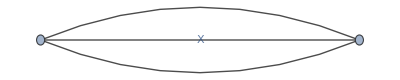
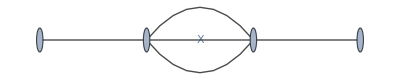
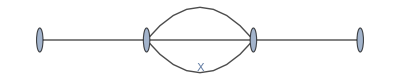
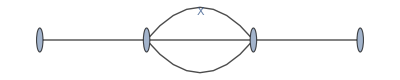
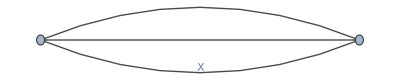
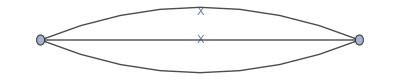
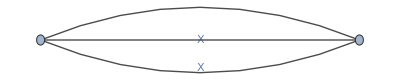
(loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2}) | loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2})/.doem2 | -Graphics-
loopIntegral(1/(((k1+k2-p)^2-m^2).(k1^2-m^2).(k2^2-m^2)),{k1,k2}) | loopIntegral(1/(((k1+k2-p)^2-m^2).(k1^2-m^2).(k2^2-m^2)),{k1,k2})/.doem2 | -Graphics-
loopIntegral(1/((k1^2-m^2)^2.((k1-k2)^2-m^2).(k2^2-m^2)),{k1,k2}) | loopIntegral(1/((k1^2-m^2)^2.((k1-k2)^2-m^2).(k2^2-m^2)),{k1,k2})/.doem2 | -Graphics-
loopIntegral(1/((k1^2-m^2)^2.(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2}) | loopIntegral(1/((k1^2-m^2)^2.(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2})/.doem2 | -Graphics-
loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2}) | loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})/.doem2 | -Graphics-
loopIntegral(1/((k1^2-m^2).((k1+k2-p)^2-m^2).(k2^2-m^2)^2),{k1,k2}) | loopIntegral(1/((k1^2-m^2).((k1+k2-p)^2-m^2).(k2^2-m^2)^2),{k1,k2})/.doem2 | -Graphics-
loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^2),{k1,k2}) | loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})/.doem2 | -Graphics-
loopIntegral(1/((k2^2-m^2).((k2+k3)^2-m^2).(k3^2-m^2)^2),{k2,k3}) | loopIntegral(1/((k2^2-m^2).((k2+k3)^2-m^2).(k3^2-m^2)^2),{k2,k3})/.doem2 | -Graphics-
loopIntegral(1/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2}) | loopIntegral(1/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})/.doem2 | -Graphics-
loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^3),{k1,k2}) | loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^3),{k1,k2})/.doem2 | -Graphics-
loopIntegral(1/((k2^2-m^2)^2.((k1-k2)^2-m^2).(k1^2-m^2)^2),{k1,k2}) | loopIntegral(1/((k2^2-m^2)^2.((k1-k2)^2-m^2).(k1^2-m^2)^2),{k1,k2})/.doem2 | -Graphics-
loopIntegral(k1^2/((k1^2-m^2)^2.(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2}) | loopIntegral(k1^2/((k1^2-m^2)^2.(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2})/.doem2 | -Graphics-
loopIntegral(k1^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2}) | loopIntegral(k1^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})/.doem2 | -Graphics-
loopIntegral(k1^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2}) | loopIntegral(k1^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})/.doem2 | -Graphics-
loopIntegral(k1^2/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^3),{k1,k2}) | loopIntegral(k1^2/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^3),{k1,k2})/.doem2 | -Graphics-
loopIntegral(k2^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2}) | loopIntegral(k2^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})/.doem2 | -Graphics-
loopIntegral(k2^2/((k1^2-m^2).((k1+k2-p)^2-m^2).(k2^2-m^2)^2),{k1,k2}) | loopIntegral(k2^2/((k1^2-m^2).((k1+k2-p)^2-m^2).(k2^2-m^2)^2),{k1,k2})/.doem2 | -Graphics-
loopIntegral(k2^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2}) | loopIntegral(k2^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})/.doem2 | -Graphics-
loopIntegral(k2^2/((k2^2-m^2)^2.((k1-k2)^2-m^2).(k1^2-m^2)^2),{k1,k2}) | loopIntegral(k2^2/((k2^2-m^2)^2.((k1-k2)^2-m^2).(k1^2-m^2)^2),{k1,k2})/.doem2 | -Graphics-)

```mathematica
gs2=AssociationMap[FCLoopIntegralToGraph@@#&,foundLIs];
plot2L=FCLoopGraphPlot/@KeySelect[gs2,Length[#[[2]]]==2&];
KeyValueMap[{#1,#1/.doem2, #2}&, plot2L]
```

```mathematica
(*doem ={loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D] - Momentum[k3, D], m], PropagatorDenominator[Momentum[k3, D], m], 
   PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]], {k1, k2, k3}]->martinF[m], 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k3, D], m], PropagatorDenominator[Momentum[k1, D], m], 
   PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m]], {k1, k2, k3}]->dmartinGbdw[m], 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3, D], m], PropagatorDenominator[Momentum[k2, D] + Momentum[k3, D], m], PropagatorDenominator[Momentum[k1, D], m], 
   PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k3, D], m]], {k1, k2, k3}]->martinH[m],

loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k3,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->martinGWithMomInjection,loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]+Momentum[k3,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k3,D],m]],{k1,k2,k3}]->d2martinEbdz2[m],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->dmartinGbdv[m],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->dmartinGbdw[m],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->d2martinEbdzbdy[m]}*)
```

```mathematica
martinF= 1/eps^3 mF3[m]
```

(mF3(m))/eps^3

```mathematica
Keys[plot3L]//InputForm
```

Keys::invrl: The argument KeySelect[FCLoopGraphPlot(gs),FCLoopGraphPlot(Length[#1⟦2⟧]==3&)] is not a valid Association or a list of rules.

Keys[KeySelect[FCLoopGraphPlot[gs], FCLoopGraphPlot[Length[#1[[2]]] == 3 & ]]]

```mathematica
appliedRules=foundSFADLIs /.rules;
unDone=KeySortBy[Select[appliedRules, Head[#]===loopIntegral&],#[[2]]&];
Length[unDone]->Length[Union@unDone]
AssociationMap[InputForm,Values[ unDone][[1;;3]]]
allRepRules =Join[rules, MapIndexed[#1 ->unknown3L[#2[[1]]]&,Values[unDone]]]
```

321→321

<|loopIntegral(1/((k1^2-m^2+ⅈ η).(k1^2-M^2+ⅈ η)),{k1})→loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1, D], 0, -m^2, {1, 1}], StandardPropagatorDenominator[Momentum[k1, D], 0, -M^2, {1, 1}]], {k1}],loopIntegral(1/((k1^2-m^2+ⅈ η).(k1^2-M^2+ⅈ η)^2),{k1})→loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1, D], 0, -m^2, {1, 1}], StandardPropagatorDenominator[Momentum[k1, D], 0, -M^2, {2, 1}]], {k1}],loopIntegral(1/((k1^2-M^2+ⅈ η).(k1^2-m^2+ⅈ η)^2),{k1})→loopIntegral[FeynAmpDenominator[StandardPropagatorDenominator[Momentum[k1, D], 0, -M^2, {1, 1}], StandardPropagatorDenominator[Momentum[k1, D], 0, -m^2, {2, 1}]], {k1}]|>

{loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,X_,{b_,1})),{k1_}):>IMaster(0,b,X),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,X_,{b_,1})) k1_^2,{k1_})→IMaster(1,b,X),loopIntegral(FeynAmpDenominator(StandardPropagatorDenominator(k1_,0,X_,{b_,1})) k1_^4,{k1_})→IMaster(2,b,X),330,loopIntegral((k3·p)/((k1^2-m^2+ⅈ η).(k2^2-M^2+ⅈ η).(k3^2-M^2+ⅈ η).((k1+k2-p)^2-m^2+ⅈ η).((k1-k3-p)^2-m^2+ⅈ η)),{k1,k2,k3})→unknown3L(320),loopIntegral((k3·p)/((k1^2-m^2+ⅈ η).(k2^2-m^2+ⅈ η).(k3^2-M^2+ⅈ η).((k1+k2-p)^2-m^2+ⅈ η).((k1-k3-p)^2-M^2+ⅈ η)),{k1,k2,k3})→unknown3L(321)}
 |  |  |  |

```mathematica
mapped = #/.allRepRules&/@foundSFADLIs
```

<|loopIntegral(1/(k1^2-m^2),{k1})→IMaster(0,1,-m^2),loopIntegral(1/(k1^2-M^2),{k1})→IMaster(0,1,-M^2),loopIntegral(1/(k2^2-m^2),{k2})→IMaster(0,1,-m^2),loopIntegral(1/(k2^2-M^2),{k2})→IMaster(0,1,-M^2),450,loopIntegral((k2^2 k3^2)/((k3^2-M^2).((k2+k3)^2-m^2).(k1^2-m^2).(k2^2-M^2).((k1+k2)^2-M^2).((k1-k3)^2-M^2)),{k1,k2,k3})→unknown3L(319),loopIntegral((k3·p)/((k3^2-M^2).((k1+k2-p)^2-m^2).((k1-k3-p)^2-m^2).(k1^2-m^2).(k2^2-M^2)),{k1,k2,k3})→unknown3L(320),loopIntegral((k3·p)/((k3^2-M^2).((k1+k2-p)^2-m^2).((k1-k3-p)^2-M^2).(k1^2-m^2).(k2^2-m^2)),{k1,k2,k3})→unknown3L(321)|>
 |  |  |  |

```mathematica
Union[Values[mapped]]/.{genSunrise4[__]->unk3L}
```

{genSunrise3({1,-m^2},{1,-m^2},{1,-m^2,-p}),genSunrise3({1,-m^2},{1,-m^2},{2,-m^2,-p}),genSunrise3({1,-m^2},{2,-m^2},{1,-m^2,0}),genSunrise3({1,-m^2},{2,-m^2},{1,-m^2,-p}),genSunrise3({2,-m^2},{1,-m^2},{1,-m^2,0}),genSunrise3({2,-m^2},{1,-m^2},{1,-m^2,-p}),genSunrise3({2,-m^2},{1,-m^2},{2,-m^2,0}),genSunrise3({2,-m^2},{2,-m^2},{1,-m^2,0}),genSunrise3({3,-m^2},{1,-m^2},{1,-m^2,0}),genSunrise3TopK2({1,-m^2},{1,-m^2},{2,-m^2,-p}),genSunrise3TopK2({1,-m^2},{2,-m^2},{2,-m^2,0}),genSunrise3TopK2({2,-m^2},{1,-m^2},{1,-m^2,-p}),genSunrise3TopK2({2,-m^2},{1,-m^2},{2,-m^2,0}),genSunrise3TopK2({2,-m^2},{2,-m^2},{1,-m^2,0}),genSunrise3TopK2({3,-m^2},{1,-m^2},{1,-m^2,0}),unk3L,IMaster(0,1,-m^2),IMaster(0,2,-m^2),IMaster(0,3,-m^2),IMaster(0,4,-m^2),IMaster(1,2,-m^2),IMaster(1,3,-m^2),IMaster(1,4,-m^2),IMaster(2,4,-m^2),unknown3L(1),unknown3L(2),unknown3L(3),unknown3L(4),unknown3L(5),unknown3L(6),unknown3L(7)}

```mathematica
replaceAMR ={A[x_]:> x (LnB[x]-1), Aϵ[x_]:> x (-1 - Zeta[2]/2+LnB[x]-(LnB[x]^2/2))}
replaceLnB= LnB[x_]-> Log[x/μb^2]
```

{A(x_):>x (LnB(x)-1),Aϵ(x_):>x (-1/2 (LnB(x))^2+LnB(x)-2/2-1)}

LnB(x_)→log(x/μb^2)

```mathematica
(*The loop integrals are functions of a common external momentum invariant
s=−p2 (2.6) using a Euclidean or signature (−+++) metric.*)
```

```mathematica
(*S[x_,y_,z_,s_]:= (-(x+y+z))/ϵMR^2+(A[x]+B[y]+B[z] - (x+y+z)/2+s/4)/ϵMR+Sfin[x,y,z]+Aϵ[x]+Aϵ[y]+Aϵ[z]
ourS[x_,y_,z_,s_]:=(f4π^2)^2 S[x,y,z,s]/.ϵMR->ϵ/2*)
S[x_,y_,z_,s_]:= (-(x+y+z))/(2 ϵMR^2)+(A[x]+A[y]+A[z] - (x+y+z)/2+s/4)/ϵMR(*+Sfin[x,y,z]+Aϵ[x]+Aϵ[y]+Aϵ[z]*)/.replaceAMR/.replaceLnB
ourS[x_,y_,z_,s_]:=1/((f4π^2)^2)S[x,y,z,s]/.ϵMR->ϵ/2
```

```mathematica
D[ourS[x,y,z,s], {x,0},{y,0},{z,0}]
```

((2 (s/4+x (log(x/μb^2)-1)+1/2 (-x-y-z)+y (log(y/μb^2)-1)+z (log(z/μb^2)-1)))/ϵ-(2 (x+y+z))/ϵ^2)/f4π^4

```mathematica
mapGSR3TopK2={genSunrise3TopK2[{1,-m1_^2},{b_/;b>=1,-m2_^2},{c_/;c>=1,-m3_^2,mom_}]:>(*DANGEROUS CASE, WHERE SUBTRACTING 1 FROM POWER REMOVES PROP*)IMaster[0,b,-m2^2]IMaster[0,c,-m3^2]+m1^2 genSunrise3[{1,-m1^2}, {b, -m2^2}, {c, -m3^2,mom}],genSunrise3TopK2[{a_/;a>1,mxSub_}, {b_, mySub_}, {c_, mzSub_,mom_}]:>genSunrise3[{a-1,mxSub}, {b, mySub}, {c, mzSub,mom}]+(-mxSub)genSunrise3[{a,mxSub}, {b, mySub}, {c, mzSub,mom}]}
genSunrise3Eval[{1,mxSub_}, {1, mySub_}, {1, mzSub_,mom_}]:=(ourS[x,y,z,s]/.{x->-mxSub, y->-mySub, z->-mzSub,s->Pair[mom,mom]}) + O[ϵ]^1/ϵ
mapGSR3 =genSunrise3[{1,mxSub_}, {1, mySub_}, {1, mzSub_,mom_}]:>genSunrise3Eval[{1,mxSub}, {1, mySub}, {1, mzSub,mom}]
mapGSR3Higher= genSunrise3[{a_/;a>=1,-m1_^2}, {b_/;b>=1, -m2_^2}, {c_/;c>=1, -m3_^2,mom_}]:>genSunrise3Evaluator[{a,-m1^2}, {b, -m2^2}, {c, -m3^2,mom}];

applyAllMaps = {mapGSR3,mapGSR3Higher,repImaster};

(*
1/((a-1)!(b-1)!(c-1)!)(1/(2 m1))^(a-1)(1/(2 m2))^(b-1)(1/(2 m3))^(c-1)(D[,{m1temp, a-1}, {m2temp, b-1}, {m3temp, c-1}]/.{m1temp->m1, m2temp->m2, m3temp->m3})+ O[ϵ]^1/ϵ*)

genSunrise3Evaluator[{a_/;a>=1,-m1_^2}, {b_/;b>=1, -m2_^2}, {c_/;c>=1, -m3_^2,mom_}]:= Module[{expr},
expr =genSunrise3Eval[{1,-m1temp^2}, {1, -m2temp^2}, {1, -m3temp^2,mom}];

Do[expr = 1/(2m1temp)D[expr,m1temp],a-1];
expr = 1/((a-1)!)expr;
Do[expr = 1/(2m2temp)D[expr,m2temp],b-1];
expr = 1/((b-1)!)expr;
Do[expr = 1/(2m3temp)D[expr,m3temp],c-1];
expr = 1/((c-1)!)expr;
(FullSimplify[expr] /.{m1temp->m1, m2temp->m2, m3temp->m3})+ O[ϵ]^1/ϵ
];


(*genSunrise3[{a_/;a>0,mxSub_}, {b_/;b>0, mySub_}, {c_/;c>0, mzSub_,mom_}]:>((D[ourS[x,y,z,s], {x,a-1},{y,b-1},{z,c-1}])/.{x->-mxSub, y->-mySub, z->-mzSub,s->Pair[mom,mom]}) + O[ϵ]*)
```

{genSunrise3TopK2({1,-m1_^2},{b_/;b≥1,-m2_^2},{c_/;c≥1,-m3_^2,mom_}):>m1^2 genSunrise3({1,-m1^2},{b,-m2^2},{c,-m3^2,mom})+IMaster(0,b,-m2^2) IMaster(0,c,-m3^2),genSunrise3TopK2({a_/;a>1,mxSub_},{b_,mySub_},{c_,mzSub_,mom_}):>genSunrise3({a-1,mxSub},{b,mySub},{c,mzSub,mom})-mxSub genSunrise3({a,mxSub},{b,mySub},{c,mzSub,mom})}

genSunrise3({1,mxSub_},{1,mySub_},{1,mzSub_,mom_}):>genSunrise3Eval({1,mxSub},{1,mySub},{1,mzSub,mom})

```mathematica
(*genSunrise3[{1,m}, {1,m}, {1,m,Momentum[p,D]}]/.mapGSR3/.f4π->4π*)
```

```mathematica
ImasterStd[a_,b_,X_]:=(μ^2)^((4-dim)/2)I (-1)^(a-b) 1/(4 π)^(dim/2) 1/(-X)^(b-a-dim/2) (Gamma[a+dim/2] Gamma[b-a-dim/2])/(Gamma[b] Gamma[dim/2])/.μ^2->μb^2/(4π Exp[-EulerGamma ])
```

```mathematica
repImaster=IMaster[a_,b_,X_]:> Series[ImasterStd[a,b,X]/.dim->4-ϵ, {ϵ,0,1},Assumptions->{m>0, μb>0}]
```

IMaster(a_,b_,X_):>Series[ImasterStd(a,b,X)/.dim→4-ϵ,{ϵ,0,1},Assumptions→{m>0,μb>0}]

```mathematica
(#/.{genSunrise4[__]->unk3L}/.applyAllMaps)&/@mapped[[33;;34]]
```

<|loopIntegral(1/((k1^2-m^2)^2.(k2^2-M^2).((k1+k2-p)^2-m^2)),{k1,k2})→-2/(f4π^4 ϵ^2)+(2 log(m^2/μb^2)-1)/(f4π^4 ϵ)+O(ϵ^0),loopIntegral(1/((k1^2-m^2).(k1^2-M^2)^3),{k1})→unknown3L(5)|>

```mathematica
evaluated=(#/.{genSunrise4[__]->unk3L}/.mapGSR3TopK2/.applyAllMaps)&/@mapped
```

<|loopIntegral(1/(k1^2-m^2),{k1})→(ⅈ m^2)/(8 π^2 ϵ)-(ⅈ (2 log(m) m^2-2 log(μb) m^2-m^2))/(16 π^2)+(ⅈ (24 log^2(m) m^2+24 log^2(μb) m^2-24 log(m) m^2-48 log(m) log(μb) m^2+24 log(μb) m^2+π^2 m^2+12 m^2) ϵ)/(384 π^2)+O(ϵ^2),loopIntegral(1/(k1^2-M^2),{k1})→(ⅈ M^2)/(8 π^2 ϵ)-(ⅈ (log(M^2) M^2-2 log(μb) M^2-M^2))/(16 π^2)+(ⅈ (6 log^2(M^2) M^2+24 log^2(μb) M^2-12 log(M^2) M^2-24 log(M^2) log(μb) M^2+24 log(μb) M^2+π^2 M^2+12 M^2) ϵ)/(384 π^2)+O(ϵ^2),454,loopIntegral((k3·p)/((k3^2-M^2).((k1+k2-p)^2-m^2).((k1-k3-p)^2-M^2).(k1^2-m^2).(k2^2-m^2)),{k1,k2,k3})→unknown3L(321)|>
 |  |  |  |

```mathematica
prepareIncludingMinusSignVariationNeg[loopIntegral[integrand_, loopMomenta_]]:= Module[{fcped, fixed, results, totalCorrectionFactor, propagators, indices},
fcped = FCFeynmanPrepare[integrand, loopMomenta, Names->x];
fixed = FCE[fcped[[3]] /.FeynAmpDenominator[a_]->FeynAmpDenominator[a]^-1//FeynAmpDenominatorExplicit] /.SPD -> Times;
results={(-1)^(#[[3]]),- #[[2]], #[[3]]} &/@ fixed;
totalCorrectionFactor =Times@@(First/@results);
propagators = #[[2]]&/@results;
indices = #[[3]]&/@results;
<|pmC->totalCorrectionFactor,loopMs->loopMomenta, props->propagators, idxs->indices,uf-> UF[loopMomenta, propagators, {}(*No map*)]|>
];
```

```mathematica
prepped =prepareIncludingMinusSignVariationNeg/@foundSFADLIs;
```

```mathematica
Merge[{prepped,evaluated}, Identity][[1]]/.m->3/.μb->1//N
```

{<|pmC→-1.,loopMs→{k1},props→{9.-1. k1^2},idxs→{1.},uf→UF({k1},{9.-1. k1^2},{})|>,(0.+0.113986 ⅈ)/(ϵ+0.)-(0.+0.0682336 ⅈ)+(0.+0.0581085 ⅈ) (ϵ+0.)+O((ϵ+0.)^2)}

```mathematica
prepped//InputForm
```

<|loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m]], {k1}] -> <|pmC -> -1, loopMs -> {k1}, props -> {-k1^2 + m^2}, idxs -> {1}, uf -> UF[{k1}, {-k1^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m]], {k2}] -> <|pmC -> -1, loopMs -> {k2}, props -> {-k2^2 + m^2}, idxs -> {1}, uf -> UF[{k2}, {-k2^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3, D], m]], {k3}] -> <|pmC -> -1, loopMs -> {k3}, props -> {-k3^2 + m^2}, idxs -> {1}, uf -> UF[{k3}, {-k3^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]], {k1}] -> 
  <|pmC -> 1, loopMs -> {k1}, props -> {-k1^2 + m^2}, idxs -> {2}, uf -> UF[{k1}, {-k1^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m]], {k2}] -> 
  <|pmC -> 1, loopMs -> {k2}, props -> {-k2^2 + m^2}, idxs -> {2}, uf -> UF[{k2}, {-k2^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3, D], m], PropagatorDenominator[Momentum[k3, D], m]], {k3}] -> 
  <|pmC -> 1, loopMs -> {k3}, props -> {-k3^2 + m^2}, idxs -> {2}, uf -> UF[{k3}, {-k3^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]], {k1}] -> 
  <|pmC -> -1, loopMs -> {k1}, props -> {-k1^2 + m^2}, idxs -> {3}, uf -> UF[{k1}, {-k1^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m]], 
   {k1, k2}] -> <|pmC -> -1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2}, idxs -> {1, 1, 1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m]], {k2}] -> 
  <|pmC -> -1, loopMs -> {k2}, props -> {-k2^2 + m^2}, idxs -> {3}, uf -> UF[{k2}, {-k2^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], m]], 
   {k1, k2}] -> <|pmC -> -1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2}, idxs -> {1, 1, 1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]], 
   {k1}] -> <|pmC -> 1, loopMs -> {k1}, props -> {-k1^2 + m^2}, idxs -> {4}, uf -> UF[{k1}, {-k1^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], 
    PropagatorDenominator[Momentum[k2, D], m]], {k1, k2}] -> <|pmC -> 1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2}, idxs -> {2, 1, 1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], m], 
    PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m]], {k1, k2}] -> 
  <|pmC -> 1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2}, idxs -> {2, 1, 1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m], 
    PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m]], {k1, k2}] -> 
  <|pmC -> 1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2}, idxs -> {1, 1, 2}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m], PropagatorDenominator[Momentum[k2, D], m], 
    PropagatorDenominator[Momentum[k2, D], m]], {k1, k2}] -> <|pmC -> 1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2}, idxs -> {1, 2, 1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D], m], 
    PropagatorDenominator[Momentum[k1, D], m]], {k1, k2}] -> <|pmC -> 1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2}, idxs -> {2, 1, 1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D] + Momentum[k3, D], m], PropagatorDenominator[Momentum[k3, D], m], 
    PropagatorDenominator[Momentum[k3, D], m]], {k2, k3}] -> <|pmC -> 1, loopMs -> {k2, k3}, props -> {-k2^2 + m^2, -k3^2 + m^2, -k2^2 - 2*k2*k3 - k3^2 + m^2}, idxs -> {1, 2, 1}, 
   uf -> UF[{k2, k3}, {-k2^2 + m^2, -k3^2 + m^2, -k2^2 - 2*k2*k3 - k3^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], 
    PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]], {k1, k2}] -> <|pmC -> -1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2}, 
   idxs -> {2, 2, 1}, uf -> UF[{k1, k2}, {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D], m], 
    PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]], {k1, k2}] -> <|pmC -> -1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2}, 
   idxs -> {3, 1, 1}, uf -> UF[{k1, k2}, {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], 
    PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]], {k1, k2}] -> <|pmC -> -1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2}, 
   idxs -> {2, 1, 2}, uf -> UF[{k1, k2}, {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D] - Momentum[k3, D], m], PropagatorDenominator[Momentum[k3, D], m], 
    PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]], {k1, k2, k3}] -> 
  <|pmC -> -1, loopMs -> {k1, k2, k3}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + 2*k1*k3 - 2*k2*k3 - k3^2 + m^2, -k3^2 + m^2}, idxs -> {2, 1, 1, 1}, 
   uf -> UF[{k1, k2, k3}, {-k1^2 + m^2, -k2^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + 2*k1*k3 - 2*k2*k3 - k3^2 + m^2, -k3^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m], 
    PropagatorDenominator[Momentum[k1, D] - Momentum[k3, D] - Momentum[p, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], m]], {k1, k2, k3}] -> 
  <|pmC -> -1, loopMs -> {k1, k2, k3}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k3^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2, -k1^2 + 2*k1*k3 - k3^2 + m^2 + 2*k1*p - 2*k3*p - p^2}, 
   idxs -> {1, 1, 1, 1, 1}, uf -> UF[{k1, k2, k3}, {-k1^2 + m^2, -k2^2 + m^2, -k3^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2, -k1^2 + 2*k1*k3 - k3^2 + m^2 + 2*k1*p - 2*k3*p - p^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], 
    PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] + Momentum[k3, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k3, D], m]], {k1, k2, k3}] -> 
  <|pmC -> 1, loopMs -> {k1, k2, k3}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k3^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 - 2*k1*k3 - 2*k2*k3 - k3^2 + m^2}, idxs -> {3, 1, 1, 1}, 
   uf -> UF[{k1, k2, k3}, {-k1^2 + m^2, -k2^2 + m^2, -k3^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 - 2*k1*k3 - 2*k2*k3 - k3^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D] - Momentum[k3, D], m], PropagatorDenominator[Momentum[k3, D], m], PropagatorDenominator[Momentum[k1, D], m], 
    PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m]], {k1, k2, k3}] -> 
  <|pmC -> 1, loopMs -> {k1, k2, k3}, props -> {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2, -k2^2 + 2*k2*k3 - k3^2 + m^2, -k3^2 + m^2}, idxs -> {2, 1, 1, 1, 1}, 
   uf -> UF[{k1, k2, k3}, {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2, -k2^2 + 2*k2*k3 - k3^2 + m^2, -k3^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D] - Momentum[k3, D], m], PropagatorDenominator[Momentum[k3, D], m], PropagatorDenominator[Momentum[k1, D], m], 
    PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m]], {k1, k2, k3}] -> 
  <|pmC -> 1, loopMs -> {k1, k2, k3}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2, -k2^2 + 2*k2*k3 - k3^2 + m^2, -k3^2 + m^2}, idxs -> {1, 2, 1, 1, 1}, 
   uf -> UF[{k1, k2, k3}, {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2, -k2^2 + 2*k2*k3 - k3^2 + m^2, -k3^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[k3, D], m], PropagatorDenominator[Momentum[k3, D], m], PropagatorDenominator[Momentum[k1, D], m], 
    PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m]], {k1, k2, k3}] -> 
  <|pmC -> 1, loopMs -> {k1, k2, k3}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + 2*k1*k3 + 2*k2*k3 - k3^2 + m^2, -k3^2 + m^2}, idxs -> {2, 2, 1, 1}, 
   uf -> UF[{k1, k2, k3}, {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + 2*k1*k3 + 2*k2*k3 - k3^2 + m^2, -k3^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k3, D], m], PropagatorDenominator[Momentum[k1, D], m], 
    PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m]], {k1, k2, k3}] -> 
  <|pmC -> 1, loopMs -> {k1, k2, k3}, props -> {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2, -k3^2 + m^2, -k1^2 - 2*k1*k3 - k3^2 + m^2}, idxs -> {2, 1, 1, 1, 1}, 
   uf -> UF[{k1, k2, k3}, {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2, -k3^2 + m^2, -k1^2 - 2*k1*k3 - k3^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3, D], m], PropagatorDenominator[Momentum[k2, D] + Momentum[k3, D], m], PropagatorDenominator[Momentum[k1, D], m], 
    PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k3, D], m]], {k1, k2, k3}] -> 
  <|pmC -> 1, loopMs -> {k1, k2, k3}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2, -k1^2 + 2*k1*k3 - k3^2 + m^2, -k3^2 + m^2, -k2^2 - 2*k2*k3 - k3^2 + m^2}, idxs -> {1, 1, 1, 1, 1, 1}, 
   uf -> UF[{k1, k2, k3}, {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2, -k1^2 + 2*k1*k3 - k3^2 + m^2, -k3^2 + m^2, -k2^2 - 2*k2*k3 - k3^2 + m^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]]*Pair[Momentum[k1, D], Momentum[k1, D]], {k1}] -> 
  <|pmC -> -1, loopMs -> {k1}, props -> {-k1^2 + m^2, -k1^2}, idxs -> {2, -1}, uf -> UF[{k1}, {-k1^2 + m^2, -k1^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]]*Pair[Momentum[k1, D], Momentum[k1, D]], 
   {k1}] -> <|pmC -> 1, loopMs -> {k1}, props -> {-k1^2 + m^2, -k1^2}, idxs -> {3, -1}, uf -> UF[{k1}, {-k1^2 + m^2, -k1^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]]*
    Pair[Momentum[k1, D], Momentum[k1, D]], {k1}] -> <|pmC -> -1, loopMs -> {k1}, props -> {-k1^2 + m^2, -k1^2}, idxs -> {4, -1}, uf -> UF[{k1}, {-k1^2 + m^2, -k1^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], m], 
     PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m]]*Pair[Momentum[k1, D], Momentum[k1, D]], {k1, k2}] -> 
  <|pmC -> -1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2, -k1^2}, idxs -> {2, 1, 1, -1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2, -k1^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m], 
     PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m]]*Pair[Momentum[k1, D], Momentum[k1, D]], {k1, k2}] -> 
  <|pmC -> -1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2, -k1^2}, idxs -> {1, 1, 2, -1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2, -k1^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], 
     PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]]*Pair[Momentum[k1, D], Momentum[k1, D]], {k1, k2}] -> 
  <|pmC -> 1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2, -k1^2}, idxs -> {2, 2, 1, -1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2, -k1^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D], m], 
     PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]]*Pair[Momentum[k1, D], Momentum[k1, D]], {k1, k2}] -> 
  <|pmC -> 1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2, -k1^2}, idxs -> {3, 1, 1, -1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2, -k1^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]]*
    Pair[Momentum[k1, D], Momentum[k1, D]]^2, {k1}] -> <|pmC -> 1, loopMs -> {k1}, props -> {-k1^2 + m^2, -k1^2}, idxs -> {4, -2}, uf -> UF[{k1}, {-k1^2 + m^2, -k1^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m]]*Pair[Momentum[k2, D], Momentum[k2, D]], {k2}] -> 
  <|pmC -> -1, loopMs -> {k2}, props -> {-k2^2 + m^2, -k2^2}, idxs -> {2, -1}, uf -> UF[{k2}, {-k2^2 + m^2, -k2^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m]]*Pair[Momentum[k2, D], Momentum[k2, D]], 
   {k2}] -> <|pmC -> 1, loopMs -> {k2}, props -> {-k2^2 + m^2, -k2^2}, idxs -> {3, -1}, uf -> UF[{k2}, {-k2^2 + m^2, -k2^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m], 
     PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m]]*Pair[Momentum[k2, D], Momentum[k2, D]], {k1, k2}] -> 
  <|pmC -> -1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2, -k2^2}, idxs -> {1, 1, 2, -1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2, -k2^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D] + Momentum[k2, D] - Momentum[p, D], m], PropagatorDenominator[Momentum[k2, D], m], 
     PropagatorDenominator[Momentum[k2, D], m]]*Pair[Momentum[k2, D], Momentum[k2, D]], {k1, k2}] -> 
  <|pmC -> -1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2, -k2^2}, idxs -> {1, 2, 1, -1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k2^2 + m^2, -k1^2 - 2*k1*k2 - k2^2 + m^2 + 2*k1*p + 2*k2*p - p^2, -k2^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], 
     PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]]*Pair[Momentum[k2, D], Momentum[k2, D]], {k1, k2}] -> 
  <|pmC -> 1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2, -k2^2}, idxs -> {2, 2, 1, -1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2, -k2^2}, {}]|>, 
 loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k2, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], 
     PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]]*Pair[Momentum[k2, D], Momentum[k2, D]], {k1, k2}] -> 
  <|pmC -> 1, loopMs -> {k1, k2}, props -> {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2, -k2^2}, idxs -> {2, 1, 2, -1}, 
   uf -> UF[{k1, k2}, {-k1^2 + m^2, -k1^2 + 2*k1*k2 - k2^2 + m^2, -k2^2 + m^2, -k2^2}, {}]|>|>

```mathematica
testThisOne[thisOne_Association]:=Module[{nLoops, epsOrder,fiestaResult,ourResult},

nLoops=Length[thisOne[loopMs]];
epsOrder=If[nLoops>1, 1, 2];

fiestaResult =SDEvaluate[thisOne[uf]/.evalPoint, thisOne[idxs], epsOrder, d0->modeldim, NumberOfLinks->6,NumberOfSubkernels->6, UsingC->True,IntegratorOptions->{{"maxeval","50000000"}},ComplexMode->True,SectorSplitting->True,Precision->9];
ourResult =Λ^nLoops thisOne[pmC] (fiestaResult /.ep->ϵ/2)/.loopCoeffRule//Expand;
Series[ourResult,{ϵ,0,epsOrder}]
];
modeldim=4;
evalPoint = {m->2, p->8}
loopCoeffRule =Λ -> I π^(d0/2)/(2π)^d0/.d0->modeldim;

evaled=testThisOne/@prepped;
(*ourResult =Λ^nLoops thisOne[pmC] (fiestaResult /.ep->ϵ/2)/.loopCoeffRule//Expand*)
```

{m→2,p→8}

```mathematica
dataSoFound=<|loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m]],{k1}]->SeriesData[ϵ,0,{0.+0.05066059182116889*I,0.-0.009784947661057286*I,0.+0.017694209491894597*I,0.-0.0037224194599248524*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m]],{k2}]->SeriesData[ϵ,0,{0.+0.05066059182116889*I,0.-0.009784947661057286*I,0.+0.017694209491894597*I,0.-0.0037224194599248524*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3,D],m]],{k3}]->SeriesData[ϵ,0,{0.+0.05066059182116889*I,0.-0.009784947661057286*I,0.+0.017694209491894597*I,0.-0.0037224194599248524*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1}]->SeriesData[ϵ,0,{0.+0.012665147955292222*I,0.-0.008778809309766938*I,0.+0.005646670830605809*I,0.-0.0031423811215221375*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k2}]->SeriesData[ϵ,0,{0.+0.012665147955292222*I,0.-0.008778809309766938*I,0.+0.005646670830605809*I,0.-0.0031423811215221375*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m]],{k3}]->SeriesData[ϵ,0,{0.+0.012665147955292222*I,0.-0.008778809309766938*I,0.+0.005646670830605809*I,0.-0.0031423811215221375*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1}]->SeriesData[ϵ,0,{0.-0.0007915717472057639*I,0.+0.0005486763734321808*I,0.-0.00035291732250084375*I},0,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]],{k1,k2}]->SeriesData[ϵ,0,{(-0.0009623484114321816-2.0353111849775345*^-8*I)+(3.675806487353564*^-6+9.2923228123958*^-7*I)*pm146,(0.0011737001955536557+6.76957316560749*^-8*I)+(0.000013167408617330965+9.700018332171644*^-6*I)*pm147,(-0.002241211528084359+0.0005310085159210851*I)+(0.000036887074264410804+0.000031776956146547004*I)*pm148,(0.0014776956683505136-0.00009658650086956667*I)+(0.00006235177078375712+0.000061033593919634356*I)*pm149},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k2}]->SeriesData[ϵ,0,{0.-0.0007915717472057639*I,0.+0.0005486763734321808*I,0.-0.00035291732250084375*I},0,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2}]->SeriesData[ϵ,0,{(-0.0009623484114321816-2.0353111849775345*^-8*I)+(3.675806487353564*^-6+9.2923228123958*^-7*I)*pm169,(0.0011737001955536557+6.76957316560749*^-8*I)+(0.000013167408617330965+9.700018332171644*^-6*I)*pm170,(-0.002241211528084359+0.0005310085159210851*I)+(0.000036887074264410804+0.000031776956146547004*I)*pm171,(0.0014776956683505136-0.00009658650086956667*I)+(0.00006235177078375712+0.000061033593919634356*I)*pm172},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1}]->SeriesData[ϵ,0,{0.+0.00006596431437800497*I,0.-0.000012740610073096841*I,0.+6.54845934026154*^-6*I},0,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2}]->SeriesData[ϵ,0,{-0.00008020190603049504-1.7041530542775998*^-9*pm192,0.00007108329542768749-1.3069237034104078*^-8*pm193,-0.000027509143546297665-6.470047092729802*^-8*pm194,-0.000030013624617004063-9.98634050720112*^-8*pm195},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]],{k1,k2}]->SeriesData[ϵ,0,{(-0.00008019570088584598-1.6961327556411278*^-9*I)-(3.063171805451349*^-7+7.743598333513848*^-8*I)*pm206,(0.00007107470440460004-8.467430285455459*^-9*I)-(5.981031840207095*^-7+4.5519004403831706*^-7*I)*pm207,(-0.00017293760220838577-0.00012257415817445037*I)-(1.2987213439948878*^-6+1.5463029502161347*^-6*I)*pm208,(0.0003523551419212216+0.0000785928425591858*I)-(2.2763576112608247*^-6+2.354983806913616*^-6*I)*pm209},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]],{k1,k2}]->SeriesData[ϵ,0,{(-0.00008019570088584598-1.6961327556411278*^-9*I)-(3.063171805451349*^-7+7.743598333513848*^-8*I)*pm220,(0.00007107470440460004-8.467430285455459*^-9*I)-(5.981031840207095*^-7+4.5519004403831706*^-7*I)*pm221,(-0.00017293760220838577-0.00012257415817445037*I)-(1.2987213439948878*^-6+1.5463029502161347*^-6*I)*pm222,(0.0003523551419212216+0.0000785928425591858*I)-(2.2763576112608247*^-6+2.354983806913616*^-6*I)*pm223},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2}]->SeriesData[ϵ,0,{(-0.00008019570088584598-1.6961327556411278*^-9*I)-(3.063171805451349*^-7+7.743598333513848*^-8*I)*pm234,(0.00007107470440460004-8.467430285455459*^-9*I)-(5.981031840207095*^-7+4.5519004403831706*^-7*I)*pm235,(-0.00017293760220838577-0.00012257415817445037*I)-(1.2987213439948878*^-6+1.5463029502161347*^-6*I)*pm236,(0.0003523551419212216+0.0000785928425591858*I)-(2.2763576112608247*^-6+2.354983806913616*^-6*I)*pm237},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1,k2}]->SeriesData[ϵ,0,{-0.00008020190603049504-1.7041530542775998*^-9*pm248,0.00007108329542768749-1.3069237034104078*^-8*pm249,-0.000027509143546297665-6.470047092729802*^-8*pm250,-0.000030013624617004063-9.98634050720112*^-8*pm251},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D]+Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m]],{k2,k3}]->SeriesData[ϵ,0,{-0.00008020190603049504-1.7041530542775998*^-9*pm262,0.00007108329542768749-1.3069237034104078*^-8*pm263,-0.000027509143546297665-6.470047092729802*^-8*pm264,-0.000030013624617004063-9.98634050720112*^-8*pm265},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1,k2}]->SeriesData[ϵ,0,{7.83286433754077*^-6+2.5297625959160416*^-9*pm269,-0.000017604922796632398+5.7459825521277336*^-9*pm270},0,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1,k2}]->SeriesData[ϵ,0,{0.000010025238233761133+2.1301913178469998*^-10*pm277,-0.000016718337571159412+2.0511913762777495*^-9*pm278,0.000021043723744815433+1.993826190280382*^-9*pm279},-1,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1,k2}]->SeriesData[ϵ,0,{7.83286433754077*^-6+2.5297625959160416*^-9*pm283,-0.000017604922796632398+5.7459825521277336*^-9*pm284},0,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.-8.126152035160348*^-6*I)+(0.+1.2209504762423328*^-10*I)*pm300,(0.+7.417639760945818*^-6*I)+(0.+9.475668880970153*^-9*I)*pm301,(0.-8.961895461547776*^-6*I)+(0.+3.123454619258642*^-8*I)*pm302,(0.+0.000011844274925835922*I)+(0.+8.291203592077704*^-8*I)*pm303,(0.-0.000011008750595267285*I)+(0.+1.7556316174260927*^-7*I)*pm304},-3,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k3,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(8.853561915279932*^-12-8.125724374395855*^-6*I)-(4.160396010641974*^-9-1.3148183450415376*^-8*I)*pm320,(-2.8428537427422428*^-9+0.00001554491058627005*I)-(5.40526857551781*^-8-7.522134913807466*^-8*I)*pm321,(-0.000013441675527519762-0.000048737474397094305*I)-(2.521132169812517*^-7-3.0012158993309103*^-7*I)*pm322,(3.76568888823489*^-6+0.000052804126563971805*I)-(7.518606971017091*^-7-8.405427281239189*^-7*I)*pm323,(6.9835831940160455*^-6-0.00017341043825166224*I)-(1.8142741309735237*^-6-2.0128187156637315*^-6*I)*pm324},-3,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]+Momentum[k3,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k3,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.+8.464832220957154*^-7*I)-(0.+6.565511408835685*^-11*I)*pm335,(0.-4.905088702863148*^-7*I)-(0.+3.072564871545046*^-10*I)*pm336,(0.+1.2498025442618361*^-7*I)-(0.+1.5023918621445514*^-9*I)*pm337,(0.+2.3166653551772027*^-6*I)-(0.+4.269540844767136*^-9*I)*pm338},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.-3.3859567674023095*^-7*I)-(0.+6.539608950272167*^-12*I)*pm354,(0.+1.9619085164354252*^-7*I)-(0.+1.4376575550635608*^-10*I)*pm355,(0.+1.1788950515198913*^-7*I)-(0.+4.813601163348749*^-10*I)*pm356,(0.-6.832233468713513*^-8*I)-(0.+1.376467059838*^-9*I)*pm357,(0.-1.0623006883420037*^-6*I)-(0.+2.1181435834425103*^-9*I)*pm358},-3,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.-6.771913534804619*^-7*I)-(0.+1.8497402762419408*^-11*I)*pm374,(0.+7.309866073972608*^-7*I)-(0.+2.723618123386884*^-10*I)*pm375,(0.+3.7822552210643094*^-7*I)-(0.+1.1247253821355787*^-9*I)*pm376,(0.-3.1345310852194597*^-6*I)-(0.+1.7268739956112624*^-9*I)*pm377,(0.+7.975291446806417*^-6*I)-(0.+3.4449463611972084*^-9*I)*pm378},-3,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.-6.771793367712537*^-7*I)-(0.+1.4389577569051803*^-11*I)*pm394,(0.+1.0695784414315802*^-6*I)-(0.+1.162268710312351*^-10*I)*pm395,(0.-1.3469478745060848*^-6*I)-(0.+2.221295299703956*^-9*I)*pm396,(0.+2.023961443922739*^-6*I)-(0.+2.5051313932949393*^-9*I)*pm397,(0.-3.941281097172294*^-6*I)-(0.+6.036420679738411*^-9*I)*pm398},-3,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.-6.771913534804619*^-7*I)-(0.+1.8497402762419408*^-11*I)*pm414,(0.+7.309866073972608*^-7*I)-(0.+2.723618123386884*^-10*I)*pm415,(0.+3.7822552210643094*^-7*I)-(0.+1.1247253821355787*^-9*I)*pm416,(0.-3.1345310852194597*^-6*I)-(0.+1.7268739956112624*^-9*I)*pm417,(0.+7.975291446806417*^-6*I)-(0.+3.4449463611972084*^-9*I)*pm418},-3,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k2,D]+Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k3,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.-1.2211182906529958*^-6*I)-(0.+3.484987879924163*^-10*I)*pm425,(0.+5.087742503032666*^-6*I)-(0.+1.4739448679456742*^-9*I)*pm426,(0.-0.000013256927994548486*I)-(0.+3.4212059960867256*^-9*I)*pm427},-1,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1}]->SeriesData[ϵ,0,{0.+0.10132118364233778*I,0.-0.04490019756527299*I,0.+0.040280889648030845*I,0.-0.016291948133427946*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1}]->SeriesData[ϵ,0,{0.+0.012665147955292222*I,0.-0.011945099464876981*I,0.+0.007841374744357326*I,0.-0.0045540494838034245*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1}]->SeriesData[ϵ,0,{0.-0.0005277144960263179*I,0.+0.0004977128755999391*I,0.-0.00032672401390972474*I},0,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1,k2}]->SeriesData[ϵ,0,{(-0.0012832019815993665-2.279561359652657*^-8*I)+(5.001099080731084*^-6+1.2904285156107482*^-6*I)*pm475,(0.0014578389098051938+1.444357936785267*^-7*I)+(0.000019559782486291962+0.000013160962382504888*I)*pm476,(-0.002932917219021027+0.00003954525238818947*I)+(0.00006020783921059059+0.00005018145447513938*I)*pm477,(0.0028881880058459868+0.00021737207678721124*I)+(0.00010908279485763983+0.00010683187442553443*I)*pm478},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1,k2}]->SeriesData[ϵ,0,{(-0.0009623473126512684+7.344684719932997*^-8*I)+(0.000010189579125407601+6.382513072193426*^-6*I)*pm489,(0.0008521927735076428+9.209949533220049*^-8*I)+(0.0000349170927427886+0.000019979940347104087*I)*pm490,(-0.0012875825567111373-0.0004928110388680198*I)+(0.00007157114849883628+0.00006329107912657967*I)*pm491,(0.0018275187299498685+0.0003139119036491674*I)+(0.00013141943463373885+0.00012350981381261417*I)*pm492},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1,k2}]->SeriesData[ϵ,0,{-0.00008020212129531044-4.518957063733861*^-9*pm503,0.00007108449983593374-2.1101566118530922*^-8*pm504,3.820023687792753*^-6-7.916628256297097*^-8*pm505,-0.00010042715625428233-2.0205887237854944*^-7*pm506},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1,k2}]->SeriesData[ϵ,0,{-0.00008020190603049504-1.7041530542775998*^-9*pm517,0.00011118466638069696-1.1583556914683979*^-8*pm518,-0.00009438170106451658-4.232764737339307*^-8*pm519,0.00005415933973602064-2.070959006327062*^-7*pm520},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]]^2,{k1}]->SeriesData[ϵ,0,{0.+0.012665147980622517*I,0.-0.014055956429437844*I,0.+0.009832224141176234*I,0.-0.005860944798531168*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]]*Pair[Momentum[k2,D],Momentum[k2,D]],{k2}]->SeriesData[ϵ,0,{0.+0.10132118364233778*I,0.-0.04490019756527299*I,0.+0.040280889648030845*I,0.-0.016291948133427946*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]]*Pair[Momentum[k2,D],Momentum[k2,D]],{k2}]->SeriesData[ϵ,0,{0.+0.012665147955292222*I,0.-0.011945099464876981*I,0.+0.007841374744357326*I,0.-0.0045540494838034245*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k2,D],Momentum[k2,D]],{k1,k2}]->SeriesData[ϵ,0,{(-0.0009623473126512684+7.344684719932997*^-8*I)+(0.000010189579125407601+6.382513072193426*^-6*I)*pm573,(0.0008521927735076428+9.209949533220049*^-8*I)+(0.0000349170927427886+0.000019979940347104087*I)*pm574,(-0.0012875825567111373-0.0004928110388680198*I)+(0.00007157114849883628+0.00006329107912657967*I)*pm575,(0.0018275187299498685+0.0003139119036491674*I)+(0.00013141943463373885+0.00012350981381261417*I)*pm576},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]]*Pair[Momentum[k2,D],Momentum[k2,D]],{k1,k2}]->SeriesData[ϵ,0,{(-0.0012832019815993665-2.279561359652657*^-8*I)+(5.001099080731084*^-6+1.2904285156107482*^-6*I)*pm587,(0.0014578389098051938+1.444357936785267*^-7*I)+(0.000019559782486291962+0.000013160962382504888*I)*pm588,(-0.002932917219021027+0.00003954525238818947*I)+(0.00006020783921059059+0.00005018145447513938*I)*pm589,(0.0028881880058459868+0.00021737207678721124*I)+(0.00010908279485763983+0.00010683187442553443*I)*pm590},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k2,D],Momentum[k2,D]],{k1,k2}]->SeriesData[ϵ,0,{-0.0001604042424302149-9.037914127467722*^-9*pm601,0.00022237197833710216-1.5529439579945997*^-7*pm602,-0.00018876333215192754-6.928391921236774*^-7*pm603,0.00010831574468436423-6.700089909892811*^-7*pm604},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k2,D],Momentum[k2,D]],{k1,k2}]->SeriesData[ϵ,0,{-0.00008020212129531044-4.518957063733861*^-9*pm615,0.00007108449983593374-2.1101566118530922*^-8*pm616,3.820023687792753*^-6-7.916628256297097*^-8*pm617,-0.00010042715625428233-2.0205887237854944*^-7*pm618},-2,2,1]|>;

dataSoFound2=<|loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m]],{k1}]->SeriesData[ϵ,0,{0.+0.05066059182116889*I,0.-0.009784947661057286*I,0.+0.017694209491894597*I,0.-0.0037224194599248524*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m]],{k2}]->SeriesData[ϵ,0,{0.+0.05066059182116889*I,0.-0.009784947661057286*I,0.+0.017694209491894597*I,0.-0.0037224194599248524*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3,D],m]],{k3}]->SeriesData[ϵ,0,{0.+0.05066059182116889*I,0.-0.009784947661057286*I,0.+0.017694209491894597*I,0.-0.0037224194599248524*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1}]->SeriesData[ϵ,0,{0.+0.012665147955292222*I,0.-0.008778809309766938*I,0.+0.005646670830605809*I,0.-0.0031423811215221375*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k2}]->SeriesData[ϵ,0,{0.+0.012665147955292222*I,0.-0.008778809309766938*I,0.+0.005646670830605809*I,0.-0.0031423811215221375*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m]],{k3}]->SeriesData[ϵ,0,{0.+0.012665147955292222*I,0.-0.008778809309766938*I,0.+0.005646670830605809*I,0.-0.0031423811215221375*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1}]->SeriesData[ϵ,0,{0.-0.0007915717472057639*I,0.+0.0005486763734321808*I,0.-0.00035291732250084375*I},0,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]],{k1,k2}]->SeriesData[ϵ,0,{(-0.0009624356870386959-2.791063925492304*^-11*I)+(1.329518488729077*^-7+2.9805194198830486*^-8*I)*pm1354,(0.0011738135273459743-3.512890802774796*^-11*I)+(4.3233283454826237*^-7+3.1121662057618296*^-7*I)*pm1355,(-0.002241346684953936+0.0005307822572011232*I)+(1.199622774651597*^-6+1.0210233158862218*^-6*I)*pm1356,(0.0014773895980347606-0.00009602692134537757*I)+(2.0181741126272513*^-6+1.9617594723735326*^-6*I)*pm1357},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k2}]->SeriesData[ϵ,0,{0.-0.0007915717472057639*I,0.+0.0005486763734321808*I,0.-0.00035291732250084375*I},0,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2}]->SeriesData[ϵ,0,{(-0.0009624356870386959-2.791063925492304*^-11*I)+(1.329518488729077*^-7+2.9805194198830486*^-8*I)*pm1377,(0.0011738135273459743-3.512890802774796*^-11*I)+(4.3233283454826237*^-7+3.1121662057618296*^-7*I)*pm1378,(-0.002241346684953936+0.0005307822572011232*I)+(1.199622774651597*^-6+1.0210233158862218*^-6*I)*pm1379,(0.0014773895980347606-0.00009602692134537757*I)+(2.0181741126272513*^-6+1.9617594723735326*^-6*I)*pm1380},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1}]->SeriesData[ϵ,0,{0.+0.00006596431437800497*I,0.-0.000012740610073096841*I,0.+6.54845934026154*^-6*I},0,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2}]->SeriesData[ϵ,0,{-0.0000802029855626915-7.819791170560334*^-10*pm1400,0.00007108354253308848-1.191415362447936*^-9*pm1401,-0.00002751087360491654-2.1378507030448306*^-9*pm1402,-0.00003001557050185924-3.3190201339846737*^-9*pm1403},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]],{k1,k2}]->SeriesData[ϵ,0,{(-0.0000802029738530555-2.2456836182121986*^-12*I)-(1.107924053642261*^-8+2.4837260817426913*^-9*I)*pm1414,(0.00007108344316158838-9.223343431942958*^-12*I)-(1.9964929395770094*^-8+1.4555157762483269*^-8*I)*pm1415,(-0.00017297817461340258-0.00012256803491705038*I)-(4.226833726497636*^-8+4.963177344312143*^-8*I)*pm1416,(0.0003523712920356724+0.00007856053042014068*I)-(7.399962623210223*^-8+7.560486895344554*^-8*I)*pm1417},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]],{k1,k2}]->SeriesData[ϵ,0,{(-0.0000802029738530555-2.2456836182121986*^-12*I)-(1.107924053642261*^-8+2.4837260817426913*^-9*I)*pm1428,(0.00007108344316158838-9.223343431942958*^-12*I)-(1.9964929395770094*^-8+1.4555157762483269*^-8*I)*pm1429,(-0.00017297817461340258-0.00012256803491705038*I)-(4.226833726497636*^-8+4.963177344312143*^-8*I)*pm1430,(0.0003523712920356724+0.00007856053042014068*I)-(7.399962623210223*^-8+7.560486895344554*^-8*I)*pm1431},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2}]->SeriesData[ϵ,0,{(-0.0000802029738530555-2.2456836182121986*^-12*I)-(1.107924053642261*^-8+2.4837260817426913*^-9*I)*pm1442,(0.00007108344316158838-9.223343431942958*^-12*I)-(1.9964929395770094*^-8+1.4555157762483269*^-8*I)*pm1443,(-0.00017297817461340258-0.00012256803491705038*I)-(4.226833726497636*^-8+4.963177344312143*^-8*I)*pm1444,(0.0003523712920356724+0.00007856053042014068*I)-(7.399962623210223*^-8+7.560486895344554*^-8*I)*pm1445},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1,k2}]->SeriesData[ϵ,0,{-0.0000802029855626915-7.819791170560334*^-10*pm1456,0.00007108354253308848-1.191415362447936*^-9*pm1457,-0.00002751087360491654-2.1378507030448306*^-9*pm1458,-0.00003001557050185924-3.3190201339846737*^-9*pm1459},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D]+Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m]],{k2,k3}]->SeriesData[ϵ,0,{-0.0000802029855626915-7.819791170560334*^-10*pm1470,0.00007108354253308848-1.191415362447936*^-9*pm1471,-0.00002751087360491654-2.1378507030448306*^-9*pm1472,-0.00003001557050185924-3.3190201339846737*^-9*pm1473},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1,k2}]->SeriesData[ϵ,0,{7.83284857765395*^-6+7.78369982669621*^-11*pm1477,-0.000017605001215102317+1.7540393117964565*^-10*pm1478},0,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1,k2}]->SeriesData[ϵ,0,{0.000010025373215387185+9.776744037859537*^-11*pm1485,-0.000016718285118406327+1.7969479095015824*^-10*pm1486,0.000021043859027202685+1.7546408341941918*^-10*pm1487},-1,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1,k2}]->SeriesData[ϵ,0,{7.83284857765395*^-6+7.78369982669621*^-11*pm1491,-0.000017605001215102317+1.7540393117964565*^-10*pm1492},0,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.-8.126261424798103*^-6*I)+(0.+5.602041528541628*^-11*I)*pm1508,(0.+7.4174557488644*^-6*I)+(0.+3.506898312520834*^-10*I)*pm1509,(0.-8.962227925190242*^-6*I)+(0.+1.0426496329919835*^-9*I)*pm1510,(0.+0.000011843647452744235*I)+(0.+2.728737160246918*^-9*I)*pm1511,(0.-0.000010997067370690232*I)+(0.+5.627433048412698*^-9*I)*pm1512},-3,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k3,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(5.89153959483979*^-14-8.126260957538066*^-6*I)-(1.3358151826879335*^-10-4.511090920807501*^-10*I)*pm1528,(-1.4714628029456757*^-11+0.000015543716781570384*I)-(1.7314655873101547*^-9-2.4640785359284823*^-9*I)*pm1529,(-0.00001344481365151393-0.00004872129369498907*I)-(8.076189518263842*^-9-9.706385126743488*^-9*I)*pm1530,(3.750340155322515*^-6+0.00005281083433168307*I)-(2.405647592138924*^-8-2.706474962105127*^-8*I)*pm1531,(6.787556786797122*^-6-0.0001734013878890885*I)-(5.7991005640624535*^-8-6.464309931850253*^-8*I)*pm1532},-3,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]+Momentum[k3,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k3,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.+8.464879769744816*^-7*I)-(0.+1.441497213627094*^-11*I)*pm1543,(0.-4.904948926086261*^-7*I)-(0.+2.997676292815811*^-11*I)*pm1544,(0.+1.2492817931086136*^-7*I)-(0.+6.140711088393962*^-11*I)*pm1545,(0.+2.316798924252133*^-6*I)-(0.+1.446329799768896*^-10*I)*pm1546},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.-3.385901447877079*^-7*I)-(0.+2.3911524493539422*^-12*I)*pm1562,(0.+1.9619555979630497*^-7*I)-(0.+6.163769355428939*^-12*I)*pm1563,(0.+1.1790750329756002*^-7*I)-(0.+1.58492572928078*^-11*I)*pm1564,(0.-6.852324532936336*^-8*I)-(0.+4.400954682778104*^-11*I)*pm1565,(0.-1.062370909272305*^-6*I)-(0.+6.604682528771204*^-11*I)*pm1566},-3,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.-6.771802895754158*^-7*I)-(0.+6.761049576423042*^-12*I)*pm1582,(0.+7.309850695022699*^-7*I)-(0.+1.579135767954817*^-11*I)*pm1583,(0.+3.7821398941767397*^-7*I)-(0.+3.827012069058388*^-11*I)*pm1584,(0.-3.1345427519915312*^-6*I)-(0.+5.901113346681404*^-11*I)*pm1585,(0.+7.975296213874576*^-6*I)-(0.+1.0762166798335833*^-10*I)*pm1586},-3,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[k3,D],m],PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.-6.771884524051027*^-7*I)-(0.+6.602587476975626*^-12*I)*pm1602,(0.+1.069580488233698*^-6*I)-(0.+1.4672980939217374*^-11*I)*pm1603,(0.-1.3470414275838287*^-6*I)-(0.+7.175539702573796*^-11*I)*pm1604,(0.+2.02397455539174*^-6*I)-(0.+8.35481261509608*^-11*I)*pm1605,(0.-3.9414206340974945*^-6*I)-(0.+1.9203790741470535*^-10*I)*pm1606},-3,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.-6.771802895754158*^-7*I)-(0.+6.761049576423042*^-12*I)*pm1622,(0.+7.309850695022699*^-7*I)-(0.+1.579135767954817*^-11*I)*pm1623,(0.+3.7821398941767397*^-7*I)-(0.+3.827012069058388*^-11*I)*pm1624,(0.-3.1345427519915312*^-6*I)-(0.+5.901113346681404*^-11*I)*pm1625,(0.+7.975296213874576*^-6*I)-(0.+1.0762166798335833*^-10*I)*pm1626},-3,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k3,D],m],PropagatorDenominator[Momentum[k2,D]+Momentum[k3,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k3,D],m]],{k1,k2,k3}]->SeriesData[ϵ,0,{(0.-1.2210293771626828*^-6*I)-(0.+1.062661059852008*^-11*I)*pm1633,(0.+5.087476348922284*^-6*I)-(0.+4.4544610359088255*^-11*I)*pm1634,(0.-0.0000132564039010893*I)-(0.+1.0234251837700804*^-10*I)*pm1635},-1,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1}]->SeriesData[ϵ,0,{0.+0.10132118364233778*I,0.-0.04490019756527299*I,0.+0.040280889648030845*I,0.-0.016291948133427946*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1}]->SeriesData[ϵ,0,{0.+0.012665147955292222*I,0.-0.011945099464876981*I,0.+0.007841374744357326*I,0.-0.0045540494838034245*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1}]->SeriesData[ϵ,0,{0.-0.0005277144960263179*I,0.+0.0004977128755999391*I,0.-0.00032672401390972474*I},0,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1,k2}]->SeriesData[ϵ,0,{(-0.001283247682544245-3.272281843680632*^-11*I)+(1.7920410907957887*^-7+4.137656025958703*^-8*I)*pm1683,(0.0014581473319131163+5.646290240076384*^-11*I)+(6.413697276539811*^-7+4.220271518153275*^-7*I)*pm1684,(-0.0029332585316919325+0.00004050934553907637*I)+(1.9552188787339964*^-6+1.611523537510008*^-6*I)*pm1685,(0.002886874321832855+0.00021821576929517038*I)+(3.5280734486518507*^-6+3.43354085537305*^-6*I)*pm1686},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1,k2}]->SeriesData[ϵ,0,{(-0.0009624356209514351+9.447911793764178*^-11*I)+(3.41960029309508*^-7+2.04135528202998*^-7*I)*pm1697,(0.000853001109651905+2.414109889578113*^-10*I)+(1.183011372724695*^-6+6.393839017115908*^-7*I)*pm1698,(-0.0012879754389799403-0.0004902741451839771*I)+(2.3652373176039205*^-6+2.028075472055175*^-6*I)*pm1699,(0.0018264133428570403+0.0003142428244592307*I)+(4.3175193233832134*^-6+3.957049246850592*^-6*I)*pm1700},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1,k2}]->SeriesData[ϵ,0,{-0.00008020276243798345-6.2750816531758*^-10*pm1711,0.00007108367871775933-1.4583309010697287*^-9*pm1712,3.820725945141363*^-6-2.548730602191298*^-9*pm1713,-0.00010043554594782325-6.5267586243882965*^-9*pm1714},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]],{k1,k2}]->SeriesData[ϵ,0,{-0.0000802029855626915-7.819791170560334*^-10*pm1725,0.00011118493810841477-1.8740229793980794*^-9*pm1726,-0.00009438394410143625-2.027812205752433*^-9*pm1727,0.00005415984611762581-6.823208912738897*^-9*pm1728},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k1,D],Momentum[k1,D]]^2,{k1}]->SeriesData[ϵ,0,{0.+0.012665147980622517*I,0.-0.014055956429437844*I,0.+0.009832224141176234*I,0.-0.005860944798531168*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]]*Pair[Momentum[k2,D],Momentum[k2,D]],{k2}]->SeriesData[ϵ,0,{0.+0.10132118364233778*I,0.-0.04490019756527299*I,0.+0.040280889648030845*I,0.-0.016291948133427946*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]]*Pair[Momentum[k2,D],Momentum[k2,D]],{k2}]->SeriesData[ϵ,0,{0.+0.012665147955292222*I,0.-0.011945099464876981*I,0.+0.007841374744357326*I,0.-0.0045540494838034245*I},-1,3,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m]]*Pair[Momentum[k2,D],Momentum[k2,D]],{k1,k2}]->SeriesData[ϵ,0,{(-0.0009624356209514351+9.447911793764178*^-11*I)+(3.41960029309508*^-7+2.04135528202998*^-7*I)*pm1781,(0.000853001109651905+2.414109889578113*^-10*I)+(1.183011372724695*^-6+6.393839017115908*^-7*I)*pm1782,(-0.0012879754389799403-0.0004902741451839771*I)+(2.3652373176039205*^-6+2.028075472055175*^-6*I)*pm1783,(0.0018264133428570403+0.0003142428244592307*I)+(4.3175193233832134*^-6+3.957049246850592*^-6*I)*pm1784},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D]+Momentum[k2,D]-Momentum[p,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m]]*Pair[Momentum[k2,D],Momentum[k2,D]],{k1,k2}]->SeriesData[ϵ,0,{(-0.001283247682544245-3.272281843680632*^-11*I)+(1.7920410907957887*^-7+4.137656025958703*^-8*I)*pm1795,(0.0014581473319131163+5.646290240076384*^-11*I)+(6.413697276539811*^-7+4.220271518153275*^-7*I)*pm1796,(-0.0029332585316919325+0.00004050934553907637*I)+(1.9552188787339964*^-6+1.611523537510008*^-6*I)*pm1797,(0.002886874321832855+0.00021821576929517038*I)+(3.5280734486518507*^-6+3.43354085537305*^-6*I)*pm1798},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k2,D],Momentum[k2,D]],{k1,k2}]->SeriesData[ϵ,0,{-0.0001604055248759669-1.2548559246624306*^-9*pm1809,0.00022237000903297494-4.935852186857683*^-9*pm1810,-0.0001887676170766771-2.2205439921361766*^-8*pm1811,0.00010831947799302428-2.133830528353299*^-8*pm1812},-2,2,1],loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D]-Momentum[k2,D],m],PropagatorDenominator[Momentum[k1,D],m],PropagatorDenominator[Momentum[k1,D],m]]*Pair[Momentum[k2,D],Momentum[k2,D]],{k1,k2}]->SeriesData[ϵ,0,{-0.00008020276243798345-6.2750816531758*^-10*pm1823,0.00007108367871775933-1.4583309010697287*^-9*pm1824,3.820725945141363*^-6-2.548730602191298*^-9*pm1825,-0.00010043554594782325-6.5267586243882965*^-9*pm1826},-2,2,1]|>; (*Done wiwth precision 10x higher*)
```

```mathematica
errorVars=Select[Union@Cases[Normal[dataSoFound2],_Symbol,Infinity],StringTake[ToString[#],UpTo[2]]=="pm"&];
```

```mathematica
evalEntirely=Join[evalPoint,{μb->1,f4π->4π}]
evalCheck = N[#/.Pair[Momentum[p, D], Momentum[p, D]]->p^2/.evalEntirely/.Thread[errorVars->0]]&/@Merge[{dataSoFound2,evaluated}, Identity];
```

{m→2,p→8,μb→1,f4π→4 π}

```mathematica
Clear[compareTwoSDs]
```

```mathematica
(*compareTwoSDs[HoldPattern@{SeriesData[ϵ,0., list1_,n_, biggerNum_, 1],SeriesData[ϵ,0., list2_,n_, smallerNum_, 1]}]/;smallerNum<=biggerNum :=Abs[f[list1[[#]],list2[[#]]]/(g@list2[[#]])]&/@Range@Length[list2]*)

compareTwoSDs[HoldPattern@{SeriesData[ϵ,0., list1_,n_, biggerNum_, 1],SeriesData[ϵ,0.,{},n_, smallerNum_, 1]}]/;smallerNum<=biggerNum :=oEps0[SeriesData[ϵ,0.,{},n, smallerNum, 1]]
compareTwoSDs[HoldPattern@{SeriesData[ϵ,0., list1_,n_, biggerNum_, 1],SeriesData[ϵ,0., list2_,n_, smallerNum_, 1]}]/;smallerNum<=biggerNum :=Chop[Abs[(list1[[#]]-list2[[#]])/list2[[#]]]&/@Range@Length[list2], 10^-8]
compareTwoSDs[{sd_SeriesData,unknown_}]/;!(Head[unknown]===SeriesData):=noAnalyticForm
```

```mathematica
evalCheck[[-2]]//InputForm
```

{SeriesData[ϵ, 0., {-0.0001604042424302149, 0.00022237197833710216, -0.00018876333215192754, 0.00010831574468436423}, -2, 2, 1], SeriesData[ϵ, 0., {-0.00016040597272944275, 0.00022236989548477743}, -2, 0, 1]}

```mathematica
comparing =compareTwoSDs/@evalCheck;
comparing
```

<|loopIntegral(1/(k1^2-m^2),{k1})→{0,2.87656×10^-7,5.9309×10^-8},loopIntegral(1/(k2^2-m^2),{k2})→{0,2.87656×10^-7,5.9309×10^-8},loopIntegral(1/(k3^2-m^2),{k3})→{0,2.87656×10^-7,5.9309×10^-8},loopIntegral(1/((k1^2-m^2)^2),{k1})→{0,2.60493×10^-7,1.58467×10^-8},loopIntegral(1/((k2^2-m^2)^2),{k2})→{0,2.60493×10^-7,1.58467×10^-8},loopIntegral(1/((k3^2-m^2)^2),{k3})→{0,2.60493×10^-7,1.58467×10^-8},loopIntegral(1/((k1^2-m^2)^3),{k1})→{0,1.1822×10^-6},loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2})→{1.57853×10^-7,1.12394×10^-7},loopIntegral(1/((k2^2-m^2)^3),{k2})→{0,1.1822×10^-6},loopIntegral(1/(((k1+k2-p)^2-m^2).(k1^2-m^2).(k2^2-m^2)),{k1,k2})→{1.57853×10^-7,1.12394×10^-7},loopIntegral(1/((k1^2-m^2)^4),{k1})→{3.2×10^-8,0.0000165499},loopIntegral(1/((k1^2-m^2)^2.((k1-k2)^2-m^2).(k2^2-m^2)),{k1,k2})→{1.×10^-8,1.2376×10^-6},loopIntegral(1/((k1^2-m^2)^2.(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2})→{1.58493×10^-7,2.06274×10^-7},loopIntegral(1/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→{1.58493×10^-7,2.06274×10^-7},loopIntegral(1/((k1^2-m^2).((k1+k2-p)^2-m^2).(k2^2-m^2)^2),{k1,k2})→{1.58493×10^-7,2.06274×10^-7},loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})→{1.×10^-8,1.2376×10^-6},loopIntegral(1/((k2^2-m^2).((k2+k3)^2-m^2).(k3^2-m^2)^2),{k2,k3})→{1.×10^-8,1.2376×10^-6},loopIntegral(1/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})→oEps0(O((ϵ+0.)^0)),loopIntegral(1/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^3),{k1,k2})→{0},loopIntegral(1/((k2^2-m^2)^2.((k1-k2)^2-m^2).(k1^2-m^2)^2),{k1,k2})→oEps0(O((ϵ+0.)^0)),loopIntegral(1/((k2^2-m^2).((k1-k2-k3)^2-m^2).(k3^2-m^2).(k1^2-m^2)^2),{k1,k2,k3})→noAnalyticForm,loopIntegral(1/((k3^2-m^2).((k1+k2-p)^2-m^2).((k1-k3-p)^2-m^2).(k1^2-m^2).(k2^2-m^2)),{k1,k2,k3})→noAnalyticForm,loopIntegral(1/((k1^2-m^2)^3.((k1+k2+k3)^2-m^2).(k2^2-m^2).(k3^2-m^2)),{k1,k2,k3})→noAnalyticForm,loopIntegral(1/(((k2-k3)^2-m^2).(k3^2-m^2).(k1^2-m^2)^2.((k1-k2)^2-m^2).(k2^2-m^2)),{k1,k2,k3})→noAnalyticForm,loopIntegral(1/(((k2-k3)^2-m^2).(k3^2-m^2).(k1^2-m^2).((k1+k2)^2-m^2).(k2^2-m^2)^2),{k1,k2,k3})→noAnalyticForm,loopIntegral(1/(((k1+k2-k3)^2-m^2).(k3^2-m^2).(k1^2-m^2)^2.(k2^2-m^2)^2),{k1,k2,k3})→noAnalyticForm,loopIntegral(1/((k3^2-m^2).((k1+k3)^2-m^2).(k1^2-m^2)^2.((k1-k2)^2-m^2).(k2^2-m^2)),{k1,k2,k3})→noAnalyticForm,loopIntegral(1/((k3^2-m^2).((k2+k3)^2-m^2).(k1^2-m^2).(k2^2-m^2).((k1+k2)^2-m^2).((k1-k3)^2-m^2)),{k1,k2,k3})→noAnalyticForm,loopIntegral(k1^2/((k1^2-m^2)^2),{k1})→{0,1.56608×10^-8,6.14382×10^-8},loopIntegral(k1^2/((k1^2-m^2)^3),{k1})→{0,7.36259×10^-8,1.1798×10^-7},loopIntegral(k1^2/((k1^2-m^2)^4),{k1})→{0,8.73077×10^-7},loopIntegral(k1^2/((k1^2-m^2)^2.(k2^2-m^2).((k1+k2-p)^2-m^2)),{k1,k2})→{8.14686×10^-8,8.69344×10^-8},loopIntegral(k1^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→{2.44414×10^-7,4.93705×10^-7},loopIntegral(k1^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})→{2.792×10^-6,3.15344×10^-6},loopIntegral(k1^2/(((k1-k2)^2-m^2).(k2^2-m^2).(k1^2-m^2)^3),{k1,k2})→{1.×10^-8,8.66482×10^-8},loopIntegral(k1^4/((k1^2-m^2)^4),{k1})→{0,1.05663×10^-8,5.67225×10^-8},loopIntegral(k2^2/((k2^2-m^2)^2),{k2})→{0,1.56608×10^-8,6.14382×10^-8},loopIntegral(k2^2/((k2^2-m^2)^3),{k2})→{0,7.36259×10^-8,1.1798×10^-7},loopIntegral(k2^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→{2.44414×10^-7,4.93705×10^-7},loopIntegral(k2^2/((k1^2-m^2).((k1+k2-p)^2-m^2).(k2^2-m^2)^2),{k1,k2})→{8.14686×10^-8,8.69344×10^-8},loopIntegral(k2^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})→{2.792×10^-6,5.10628×10^-7},loopIntegral(k2^2/((k2^2-m^2)^2.((k1-k2)^2-m^2).(k1^2-m^2)^2),{k1,k2})→{2.792×10^-6,3.15344×10^-6}|>

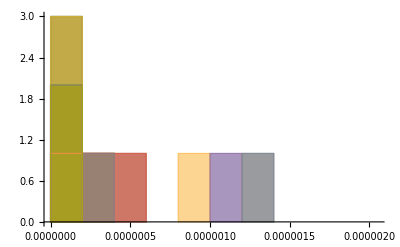

```mathematica
Histogram[Values[comparing]]
```

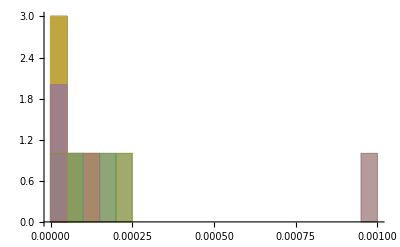

```mathematica
Histogram[Values[comparing]]
```

```mathematica
(*evaluated=(#/.{genSunrise4[__]->unk3L}/.repImaster/.mapGSR3TopK2)&/@mapped*)
```

```mathematica
mapped[[{-2}]]/.mapGSR3TopK2
```

<|loopIntegral(k2^2/(((k1-k2)^2-m^2)^2.(k2^2-m^2).(k1^2-m^2)^2),{k1,k2})→m^2 genSunrise3({1,-m^2},{2,-m^2},{2,-m^2,0})+IMaster(0,2,-m^2) IMaster(0,2,-m^2)|>

```mathematica
(mapped[[-2]]/.mapGSR3TopK2)//N
```

m^2 genSunrise3({1.,-1. m^2},{2.,-1. m^2},{2.,-1. m^2,0.})+(IMaster(0.,2.,-1. m^2))^2

```mathematica
List@@(mapped[[-4]]/.mapGSR3TopK2)/.applyAllMaps
```

{-(2 m^2)/(f4π^4 ϵ^2)+(m^2 (2 log(m^2/μb^2)-1))/(f4π^4 ϵ)+O(ϵ^0),-m^2/(64 π^4 ϵ^2)+(((log(m)-log(μb)) m^2)/(64 π^4)+(2 log(m) m^2-2 log(μb) m^2-m^2)/(128 π^4))/ϵ+(-((24 log^2(m)-48 log(μb) log(m)+24 log^2(μb)+π^2) m^2)/(3072 π^4)-((log(m)-log(μb)) (2 log(m) m^2-2 log(μb) m^2-m^2))/(128 π^4)-(24 log^2(m) m^2+24 log^2(μb) m^2-24 log(m) m^2-48 log(m) log(μb) m^2+24 log(μb) m^2+π^2 m^2+12 m^2)/(3072 π^4))+O(ϵ^1)}

```mathematica
List@@(mapped[[-4]]/.mapGSR3TopK2)/.mapGSR3TopK2/.mapGSR3Higher/.mapGSR3/.repImaster
```

{-(2 m^2)/(f4π^4 ϵ^2)+(m^2 (2 log(m^2/μb^2)-1))/(f4π^4 ϵ)+O(ϵ^0),-m^2/(64 π^4 ϵ^2)+(((log(m)-log(μb)) m^2)/(64 π^4)+(2 log(m) m^2-2 log(μb) m^2-m^2)/(128 π^4))/ϵ+(-((24 log^2(m)-48 log(μb) log(m)+24 log^2(μb)+π^2) m^2)/(3072 π^4)-((log(m)-log(μb)) (2 log(m) m^2-2 log(μb) m^2-m^2))/(128 π^4)-(24 log^2(m) m^2+24 log^2(μb) m^2-24 log(m) m^2-48 log(m) log(μb) m^2+24 log(μb) m^2+π^2 m^2+12 m^2)/(3072 π^4))+O(ϵ^1)}

```mathematica
Identity[List@@(mapped[[-4]]/.mapGSR3TopK2)/.mapGSR3Higher/.mapGSR3/.repImaster/.evalEntirely//N]
```

{-0.000320812/(ϵ+0.)^2+0.000284334/(ϵ+0.)+O((ϵ+0.)^0),-0.000641624/(ϵ+0.)^2+0.000568668/(ϵ+0.)-0.000596064+O((ϵ+0.)^1)}

```mathematica
evalCheck[[{-4}]]
```

<|loopIntegral(k2^2/((k1^2-m^2).(k2^2-m^2).((k1+k2-p)^2-m^2)^2),{k1,k2})→{-(0.000962347-7.34468×10^-8 ⅈ)/(ϵ+0.)^2+(0.000852193+9.20995×10^-8 ⅈ)/(ϵ+0.)-(0.00128758+0.000492811 ⅈ)+(0.00182752+0.000313912 ⅈ) (ϵ+0.)+O((ϵ+0.)^2),-0.000962436/(ϵ+0.)^2+0.000853001/(ϵ+0.)+O((ϵ+0.)^0)}|>

```mathematica
0.000320812/0.0009623
```

0.33338

```mathematica
genSunrise3Evaluator[{1, -m1^2}, {1, -m^2}, {2, -m^2,mom}]/.evalEntirely//N
```

-0.000080203/(ϵ+0.)^2+0.0000710835/(ϵ+0.)+O((ϵ+0.)^0)

```mathematica
genSunrise3Evaluator[{3, -m^2}, {1, -m^2}, {1, -m^2,0}]/.evalEntirely//N
```

0.0000100254/(ϵ+0.)+O((ϵ+0.)^0)

```mathematica
m^2
```

```mathematica
mapGSR3Higher
```

genSunrise3({a_/;a≥1,-m1_^2},{b_/;b≥1,-m2_^2},{c_/;c≥1,-m3_^2,mom_}):>((1/(2 m1))^(a-1) (1/(2 m2))^(b-1) (1/(2 m3))^(c-1) (∂^((a-1)+(b-1)+(c-1)) genSunrise3Eval({1,-m1^2},{1,-m2^2},{1,-m3^2,mom}))/(∂m1^(a-1) ∂m2^(b-1) ∂m3^(c-1)))/((a-1)! (b-1)! (c-1)!)+(O(ϵ))^1/ϵ

```mathematica
genSunrise3[{2, -m^2}, {2, -m^2}, {1, -m^2,0}]/.mapGSR3Higher
```

O(ϵ^0)

```mathematica
D[genSunrise3Eval[{1,-m1^2}, {1, -m2^2}, {1, -m3^2,mom}],{m1,1}, {m2,1}]
```

0

```mathematica
/.mapGSR3TopK2(*/.mapGSR3Higher/.mapGSR3*)
```

```mathematica
genSunrise3Eval[{1,x}, {2,y},{3,z,p}]
```

genSunrise3Eval({1,x},{2,y},{3,z,p})

```mathematica
evaluatedWithEpsFor3L=(evaluated)/.{unknown3L[a_]->unknown3L[a]/ϵ^3+unknown3L[a]/ϵ^2+(unknown3L[a]+O[ϵ])/ϵ, unk3L->unk3L/ϵ^3+unk3L/ϵ^2+(unk3L+O[ϵ])/ϵ};
```

```mathematica
withHigherOrder =Normal[#]+hOϵ(*higher order in eps*)*ϵ^(#/.HoldPattern@SeriesData[x_,x0_,list_, nmin_, nmax_, den_]->nmax)&/@evaluatedWithEpsFor3L;
properReplacementRule = Dispatch@Normal[withHigherOrder, Association];
```

```mathematica
allDone =((#/.diag[{{0, b_,c_}}]:>ev@Series[b/.properReplacementRule,{ϵ,0,10}])&/@#)&/@allAnalysedDropBad;
```

```mathematica
Cases[Normal@Normal@Normal[allDone],loopIntegral[_,_],Infinity]/.properReplacementRule
```

{}

```mathematica
withHigherOrder[[{7}]]//InputForm
```

<|loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m]], {k1}] -> 
  (I/8)/(Pi^2*ϵ) + hOϵ*ϵ^2 - ((I/8)*(Log[m] - Log[μb]))/Pi^2 + ((I/384)*ϵ*(Pi^2 + 24*Log[m]^2 - 48*Log[m]*Log[μb] + 24*Log[μb]^2))/Pi^2|>

```mathematica
KeySelect[withHigherOrder, Length[#[[2]]]==2&][[{4}]]//InputForm
```

<|loopIntegral[FeynAmpDenominator[PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D], m], PropagatorDenominator[Momentum[k1, D] - Momentum[k2, D], m], 
    PropagatorDenominator[Momentum[k2, D], m]], {k1, k2}] -> hOϵ - 2/(f4π^4*ϵ^2) + (-1 + 2*Log[m^2/μb^2])/(f4π^4*ϵ)|>

```mathematica
~
```

```mathematica
Collect[#[[4]],g]&/@allDone[[4]]
```

<|TensorContract[go⊗go,(3 | 7
4 | 8)]→ev((ⅈ (ct^2 dZϕ2^2-2 ct dZϕ2+1) g^2)/(16 π^2 ϵ)+1/2 g^2 ((ⅈ ct (ct dZmϕ2^2+4 ct dZϕ2 dZmϕ2-6 dZmϕ2-5 ct dZϕ2^2+6 dZϕ2-12 ct dZϕ2^2 log(m)+24 dZϕ2 log(m)+12 ct dZϕ2^2 log(μb)-24 dZϕ2 log(μb)))/(96 π^2)-(ⅈ (log(m)-log(μb)))/(8 π^2))+1/2 g^2 ((ⅈ (24 log^2(m)-48 log(μb) log(m)+24 log^2(μb)+π^2))/(384 π^2)+ct ((ⅈ ct (24 log^2(m)-48 log(μb) log(m)+20 log(m)+24 log^2(μb)-20 log(μb)+π^2+2) dZϕ2^2)/(384 π^2)-(ⅈ (24 log^2(m)-48 log(μb) log(m)+12 log(m)+24 log^2(μb)-12 log(μb)+π^2) dZϕ2)/(192 π^2)-(ⅈ dZmϕ2 (-ct dZmϕ2+2 ct log(m) dZmϕ2-2 ct log(μb) dZmϕ2+2 ct dZϕ2+8 ct dZϕ2 log(m)-12 log(m)-8 ct dZϕ2 log(μb)+12 log(μb)))/(192 π^2))) ϵ+1/2 g^2 (hOϵ+ct (ct hOϵ dZϕ2^2-2 hOϵ dZϕ2+dZmϕ2 m^2 (ct dZmϕ2 hOϵ m^2-2 ct dZϕ2 hOϵ+2 hOϵ))) ϵ^2+O(ϵ^11))|>

```mathematica
allDone[[{1,2,4,5}]]
```

<|{ϕϕ,1}→<|TensorContract[go,(3 | 4)]→fullContrib(1,{go_{Α,Β,γ,γ}},fullSym(TensorContract[go,(3 | 4)],2),ev((ⅈ g (ct dZmϕ2 m^2-2 ct dZϕ2 m^2+m^2))/(16 π^2 ϵ)+(ⅈ g (-ct dZϕ2 m^2-2 ct dZmϕ2 log(m) m^2+4 ct dZϕ2 log(m) m^2-2 log(m) m^2+2 ct dZmϕ2 log(μb) m^2-4 ct dZϕ2 log(μb) m^2+2 log(μb) m^2+m^2))/(32 π^2)+1/2 g ((ⅈ ct dZmϕ2 (24 log^2(m)-48 log(μb) log(m)+24 log^2(μb)+π^2) m^2)/(384 π^2)-(ⅈ ct dZϕ2 (24 log^2(m) m^2+24 log^2(μb) m^2-12 log(m) m^2-48 log(m) log(μb) m^2+12 log(μb) m^2+π^2 m^2+6 m^2))/(192 π^2)+(ⅈ (24 log^2(m) m^2+24 log^2(μb) m^2-24 log(m) m^2-48 log(m) log(μb) m^2+24 log(μb) m^2+π^2 m^2+12 m^2))/(384 π^2)) ϵ+1/2 g (ct dZmϕ2 hOϵ m^2-ct dZϕ2 hOϵ+hOϵ) ϵ^2+O(ϵ^11)))|>,{ϕϕ,2}→<|TensorContract[go⊗go,(3 | 5
4 | 6
7 | 8)]→fullContrib(1,{go_{Α,Β,γ,δ},go_{γ,δ,η,η}},fullSym(TensorContract[go⊗go,(3 | 5
4 | 6
7 | 8)],2),ev(-(ⅈ g^2 (ct dZmϕ2 m^2-4 ct dZϕ2 m^2+m^2))/(256 π^4 ϵ^2)+(ⅈ g^2 (ct dZmϕ2 m^2+2 ct dZϕ2 m^2+4 ct dZmϕ2 log(m) m^2-16 ct dZϕ2 log(m) m^2+4 log(m) m^2-4 ct dZmϕ2 log(μb) m^2+16 ct dZϕ2 log(μb) m^2-4 log(μb) m^2-m^2))/(512 π^4 ϵ)-1/(6144 π^4)ⅈ g^2 (48 ct dZmϕ2 log^2(m) m^2-192 ct dZϕ2 log^2(m) m^2+48 log^2(m) m^2+48 ct dZmϕ2 log^2(μb) m^2-192 ct dZϕ2 log^2(μb) m^2+48 log^2(μb) m^2-6 ct dZmϕ2 m^2-12 ct dZϕ2 m^2+24 ct dZmϕ2 log(m) m^2+48 ct dZϕ2 log(m) m^2-24 log(m) m^2-24 ct dZmϕ2 log(μb) m^2-48 ct dZϕ2 log(μb) m^2-96 ct dZmϕ2 log(m) log(μb) m^2+384 ct dZϕ2 log(m) log(μb) m^2-96 log(m) log(μb) m^2+24 log(μb) m^2+ct dZmϕ2 π^2 m^2-4 ct dZϕ2 π^2 m^2+π^2 m^2+6 m^2)+1/4 ⅈ g^2 ((ⅈ (2 ct dZmϕ2 hOϵ m^2-2 ct dZϕ2 hOϵ+hOϵ) m^2)/(8 π^2)-1/(6144 π^4)(2 log(m) m^2-2 log(μb) m^2-m^2) (48 ct dZϕ2 log^2(m)-24 log^2(m)-24 ct dZmϕ2 log(m)+24 ct dZϕ2 log(m)-96 ct dZϕ2 log(μb) log(m)+48 log(μb) log(m)+48 ct dZϕ2 log^2(μb)-24 log^2(μb)+24 ct dZmϕ2 log(μb)-24 ct dZϕ2 log(μb)+2 ct dZϕ2 π^2-π^2)+((ct dZmϕ2-ct dZϕ2-4 ct dZϕ2 log(m)+2 log(m)+4 ct dZϕ2 log(μb)-2 log(μb)) (24 log^2(m) m^2+24 log^2(μb) m^2-24 log(m) m^2-48 log(m) log(μb) m^2+24 log(μb) m^2+π^2 m^2+12 m^2))/(6144 π^4)+ct ((ⅈ (dZmϕ2-2 dZϕ2) hOϵ m^2)/(8 π^2)+((dZϕ2 m^2+2 dZmϕ2 log(m) m^2-4 dZϕ2 log(m) m^2-2 dZmϕ2 log(μb) m^2+4 dZϕ2 log(μb) m^2) (24 log^2(m)-48 log(μb) log(m)+24 log^2(μb)+π^2))/(6144 π^4)-(ⅈ (log(m)-log(μb)) ((ⅈ dZmϕ2 m^2 (24 log^2(m)-48 log(μb) log(m)+24 log^2(μb)+π^2))/(384 π^2)-(ⅈ dZϕ2 (24 log^2(m) m^2+24 log^2(μb) m^2-12 log(m) m^2-48 log(m) log(μb) m^2+12 log(μb) m^2+π^2 m^2+6 m^2))/(192 π^2)))/(8 π^2)+(ⅈ (dZmϕ2 hOϵ m^2-dZϕ2 hOϵ))/(8 π^2))-(ⅈ (2 ct dZϕ2-1) hOϵ)/(8 π^2)) ϵ+1/4 ⅈ g^2 (-(ⅈ hOϵ (ct dZmϕ2-ct dZϕ2-4 ct dZϕ2 log(m)+2 log(m)+4 ct dZϕ2 log(μb)-2 log(μb)))/(16 π^2)-(ⅈ (2 ct dZmϕ2 hOϵ m^2-2 ct dZϕ2 hOϵ+hOϵ) (2 log(m) m^2-2 log(μb) m^2-m^2))/(16 π^2)+1/(147456 π^4)(48 ct dZϕ2 log^2(m)-24 log^2(m)-24 ct dZmϕ2 log(m)+24 ct dZϕ2 log(m)-96 ct dZϕ2 log(μb) log(m)+48 log(μb) log(m)+48 ct dZϕ2 log^2(μb)-24 log^2(μb)+24 ct dZmϕ2 log(μb)-24 ct dZϕ2 log(μb)+2 ct dZϕ2 π^2-π^2) (24 log^2(m) m^2+24 log^2(μb) m^2-24 log(m) m^2-48 log(m) log(μb) m^2+24 log(μb) m^2+π^2 m^2+12 m^2)+ct (-(ⅈ (dZmϕ2 hOϵ m^2-dZϕ2 hOϵ) (log(m)-log(μb)))/(8 π^2)-(ⅈ hOϵ (dZϕ2 m^2+2 dZmϕ2 log(m) m^2-4 dZϕ2 log(m) m^2-2 dZmϕ2 log(μb) m^2+4 dZϕ2 log(μb) m^2))/(16 π^2)+(ⅈ (24 log^2(m)-48 log(μb) log(m)+24 log^2(μb)+π^2) ((ⅈ dZmϕ2 m^2 (24 log^2(m)-48 log(μb) log(m)+24 log^2(μb)+π^2))/(384 π^2)-(ⅈ dZϕ2 (24 log^2(m) m^2+24 log^2(μb) m^2-12 log(m) m^2-48 log(m) log(μb) m^2+12 log(μb) m^2+π^2 m^2+6 m^2))/(192 π^2)))/(384 π^2))) ϵ^2+1/4 ⅈ g^2 (-(ⅈ hOϵ (48 ct dZϕ2 log^2(m)-24 log^2(m)-24 ct dZmϕ2 log(m)+24 ct dZϕ2 log(m)-96 ct dZϕ2 log(μb) log(m)+48 log(μb) log(m)+48 ct dZϕ2 log^2(μb)-24 log^2(μb)+24 ct dZmϕ2 log(μb)-24 ct dZϕ2 log(μb)+2 ct dZϕ2 π^2-π^2))/(384 π^2)+(ⅈ (2 ct dZmϕ2 hOϵ m^2-2 ct dZϕ2 hOϵ+hOϵ) (24 log^2(m) m^2+24 log^2(μb) m^2-24 log(m) m^2-48 log(m) log(μb) m^2+24 log(μb) m^2+π^2 m^2+12 m^2))/(384 π^2)+ct ((ⅈ (dZmϕ2 hOϵ m^2-dZϕ2 hOϵ) (24 log^2(m)-48 log(μb) log(m)+24 log^2(μb)+π^2))/(384 π^2)+hOϵ ((ⅈ dZmϕ2 m^2 (24 log^2(m)-48 log(μb) log(m)+24 log^2(μb)+π^2))/(384 π^2)-(ⅈ dZϕ2 (24 log^2(m) m^2+24 log^2(μb) m^2-12 log(m) m^2-48 log(m) log(μb) m^2+12 log(μb) m^2+π^2 m^2+6 m^2))/(192 π^2)))) ϵ^3+1/4 ⅈ g^2 (ct hOϵ (dZmϕ2 hOϵ m^2-dZϕ2 hOϵ)+hOϵ (2 ct dZmϕ2 hOϵ m^2-2 ct dZϕ2 hOϵ+hOϵ)) ϵ^4+O(ϵ^11))),TensorContract[go⊗go,(2 | 6
3 | 7
4 | 8)]→fullContrib(1,{go_{Α,β,γ,δ},go_{ε,β,γ,δ}},fullSym(TensorContract[go⊗go,(2 | 6
3 | 7
4 | 8)],2),ev(-(ⅈ g^2 (ct dZmϕ2 m^2-4 ct dZϕ2 m^2+m^2))/(f4π^4 ϵ^2)+(ⅈ g^2 (-6 ct dZmϕ2 m^2+60 ct dZϕ2 m^2+12 ct dZmϕ2 log(m^2/μb^2) m^2-48 ct dZϕ2 log(m^2/μb^2) m^2+12 log(m^2/μb^2) m^2-18 m^2-3 ct dZϕ2 p^2+p^2))/(12 f4π^4 ϵ)-1/6 ⅈ g^2 (-3 ct dZmϕ2 hOϵ m^2+ct dZϕ2 hOϵ m^2+3 ct dZϕ2 hOϵ-hOϵ)+O(ϵ^11)))|>,{g,1}→<|TensorContract[go⊗go,(3 | 7
4 | 8)]→fullContrib(3,{go_{Α,Β,γ,δ},go_{ε,ζ,γ,δ}},fullSym(TensorTranspose[TensorContract[go⊗go,(3 | 7
4 | 8)],{1,3,2,4}],4),ev((ⅈ (ct^2 dZϕ2^2-2 ct dZϕ2+1) g^2)/(16 π^2 ϵ)+1/2 g^2 ((ⅈ ct (ct dZmϕ2^2+4 ct dZϕ2 dZmϕ2-6 dZmϕ2-5 ct dZϕ2^2+6 dZϕ2-12 ct dZϕ2^2 log(m)+24 dZϕ2 log(m)+12 ct dZϕ2^2 log(μb)-24 dZϕ2 log(μb)))/(96 π^2)-(ⅈ (log(m)-log(μb)))/(8 π^2))+1/2 g^2 ((ⅈ (24 log^2(m)-48 log(μb) log(m)+24 log^2(μb)+π^2))/(384 π^2)+ct ((ⅈ ct (24 log^2(m)-48 log(μb) log(m)+20 log(m)+24 log^2(μb)-20 log(μb)+π^2+2) dZϕ2^2)/(384 π^2)-(ⅈ (24 log^2(m)-48 log(μb) log(m)+12 log(m)+24 log^2(μb)-12 log(μb)+π^2) dZϕ2)/(192 π^2)-(ⅈ dZmϕ2 (-ct dZmϕ2+2 ct log(m) dZmϕ2-2 ct log(μb) dZmϕ2+2 ct dZϕ2+8 ct dZϕ2 log(m)-12 log(m)-8 ct dZϕ2 log(μb)+12 log(μb)))/(192 π^2))) ϵ+1/2 g^2 (hOϵ+ct (ct hOϵ dZϕ2^2-2 hOϵ dZϕ2+dZmϕ2 m^2 (ct dZmϕ2 hOϵ m^2-2 ct dZϕ2 hOϵ+2 hOϵ))) ϵ^2+O(ϵ^11)))|>,{g,2}→<|TensorContract[go⊗go⊗go,(3 | 9
4 | 10
7 | 11
8 | 12)]→fullContrib(3,{go_{Α,Β,γ,δ},go_{ε,ζ,η,θ},go_{γ,δ,η,θ}},fullSym(TensorTranspose[TensorContract[go⊗go⊗go,(3 | 9
4 | 10
7 | 11
8 | 12)],{1,3,2,4}],4),ev((ⅈ (4 ct dZϕ2-1) g^3)/(256 π^4 ϵ^2)+(ⅈ g^3 (ct dZmϕ2-ct dZϕ2-8 ct dZϕ2 log(m)+2 log(m)+8 ct dZϕ2 log(μb)-2 log(μb)))/(256 π^4 ϵ)+(ⅈ g^3 (192 ct dZϕ2 log^2(m)-48 log^2(m)-48 ct dZmϕ2 log(m)+48 ct dZϕ2 log(m)-384 ct dZϕ2 log(μb) log(m)+96 log(μb) log(m)+192 ct dZϕ2 log^2(μb)-48 log^2(μb)+48 ct dZmϕ2 log(μb)-48 ct dZϕ2 log(μb)+4 ct dZϕ2 π^2-π^2))/(6144 π^4)+1/4 ⅈ g^3 (-(ⅈ (2 ct dZϕ2-1) hOϵ)/(8 π^2)+((ct dZmϕ2-ct dZϕ2-4 ct dZϕ2 log(m)+2 log(m)+4 ct dZϕ2 log(μb)-2 log(μb)) (24 log^2(m)-48 log(μb) log(m)+24 log^2(μb)+π^2))/(6144 π^4)-1/(3072 π^4)(log(m)-log(μb)) (48 ct dZϕ2 log^2(m)-24 log^2(m)-24 ct dZmϕ2 log(m)+24 ct dZϕ2 log(m)-96 ct dZϕ2 log(μb) log(m)+48 log(μb) log(m)+48 ct dZϕ2 log^2(μb)-24 log^2(μb)+24 ct dZmϕ2 log(μb)-24 ct dZϕ2 log(μb)+2 ct dZϕ2 π^2-π^2)+2 ct (-(ⅈ dZϕ2 hOϵ)/(8 π^2)+((dZmϕ2-dZϕ2-4 dZϕ2 log(m)+4 dZϕ2 log(μb)) (24 log^2(m)-48 log(μb) log(m)+24 log^2(μb)+π^2))/(12288 π^4)-((log(m)-log(μb)) (24 dZϕ2 log^2(m)-12 dZmϕ2 log(m)+12 dZϕ2 log(m)-48 dZϕ2 log(μb) log(m)+24 dZϕ2 log^2(μb)+12 dZmϕ2 log(μb)-12 dZϕ2 log(μb)+dZϕ2 π^2))/(3072 π^4)+(ⅈ (dZmϕ2 hOϵ m^2-dZϕ2 hOϵ))/(8 π^2))+(ⅈ (2 ct dZmϕ2 hOϵ m^2-2 ct dZϕ2 hOϵ+hOϵ))/(8 π^2)) ϵ+1/4 ⅈ g^3 (-(ⅈ (2 ct dZmϕ2 hOϵ m^2-2 ct dZϕ2 hOϵ+hOϵ) (log(m)-log(μb)))/(8 π^2)-(ⅈ hOϵ (ct dZmϕ2-ct dZϕ2-4 ct dZϕ2 log(m)+2 log(m)+4 ct dZϕ2 log(μb)-2 log(μb)))/(16 π^2)+1/(147456 π^4)(24 log^2(m)-48 log(μb) log(m)+24 log^2(μb)+π^2) (48 ct dZϕ2 log^2(m)-24 log^2(m)-24 ct dZmϕ2 log(m)+24 ct dZϕ2 log(m)-96 ct dZϕ2 log(μb) log(m)+48 log(μb) log(m)+48 ct dZϕ2 log^2(μb)-24 log^2(μb)+24 ct dZmϕ2 log(μb)-24 ct dZϕ2 log(μb)+2 ct dZϕ2 π^2-π^2)+2 ct (-(ⅈ (dZmϕ2 hOϵ m^2-dZϕ2 hOϵ) (log(m)-log(μb)))/(8 π^2)-(ⅈ hOϵ (dZmϕ2-dZϕ2-4 dZϕ2 log(m)+4 dZϕ2 log(μb)))/(32 π^2)+((24 log^2(m)-48 log(μb) log(m)+24 log^2(μb)+π^2) (24 dZϕ2 log^2(m)-12 dZmϕ2 log(m)+12 dZϕ2 log(m)-48 dZϕ2 log(μb) log(m)+24 dZϕ2 log^2(μb)+12 dZmϕ2 log(μb)-12 dZϕ2 log(μb)+dZϕ2 π^2))/(147456 π^4))) ϵ^2+1/4 ⅈ g^3 ((ⅈ (2 ct dZmϕ2 hOϵ m^2-2 ct dZϕ2 hOϵ+hOϵ) (24 log^2(m)-48 log(μb) log(m)+24 log^2(μb)+π^2))/(384 π^2)-(ⅈ hOϵ (48 ct dZϕ2 log^2(m)-24 log^2(m)-24 ct dZmϕ2 log(m)+24 ct dZϕ2 log(m)-96 ct dZϕ2 log(μb) log(m)+48 log(μb) log(m)+48 ct dZϕ2 log^2(μb)-24 log^2(μb)+24 ct dZmϕ2 log(μb)-24 ct dZϕ2 log(μb)+2 ct dZϕ2 π^2-π^2))/(384 π^2)+2 ct ((ⅈ (dZmϕ2 hOϵ m^2-dZϕ2 hOϵ) (24 log^2(m)-48 log(μb) log(m)+24 log^2(μb)+π^2))/(384 π^2)-(ⅈ hOϵ (24 dZϕ2 log^2(m)-12 dZmϕ2 log(m)+12 dZϕ2 log(m)-48 dZϕ2 log(μb) log(m)+24 dZϕ2 log^2(μb)+12 dZmϕ2 log(μb)-12 dZϕ2 log(μb)+dZϕ2 π^2))/(384 π^2))) ϵ^3+1/4 ⅈ g^3 (2 ct hOϵ (dZmϕ2 hOϵ m^2-dZϕ2 hOϵ)+hOϵ (2 ct dZmϕ2 hOϵ m^2-2 ct dZϕ2 hOϵ+hOϵ)) ϵ^4+O(ϵ^11))),TensorContract[go⊗go⊗go,(3 | 7
4 | 9
8 | 10
11 | 12)]→fullContrib(3,{go_{Α,Β,γ,δ},go_{ε,ζ,γ,θ},go_{δ,θ,λ,λ}},fullSym(TensorTranspose[TensorContract[go⊗go⊗go,(3 | 7
4 | 9
8 | 10
11 | 12)],{1,3,2,4}],4),ev((ⅈ (1-4 ct dZϕ2) g^3)/(512 π^4 ϵ)+(ⅈ g^3 (-2 ct dZmϕ2-2 ct dZϕ2+16 ct dZϕ2 log(m)-4 log(m)-16 ct dZϕ2 log(μb)+4 log(μb)+1))/(1024 π^4)+1/(24576 π^4)ⅈ g^3 (4608 ⅈ ct dZmϕ2 hOϵ π^2 m^4+1536 ⅈ ct dZmϕ2 hOϵ π^2 m^2-7680 ⅈ ct dZϕ2 hOϵ π^2 m^2+1536 ⅈ hOϵ π^2 m^2-288 ct dZϕ2 log^2(m)+72 log^2(m)-288 ct dZϕ2 log^2(μb)+72 log^2(μb)-24 ct dZmϕ2-24 ct dZϕ2+72 ct dZmϕ2 log(m)+120 ct dZϕ2 log(m)-48 log(m)-72 ct dZmϕ2 log(μb)-120 ct dZϕ2 log(μb)+576 ct dZϕ2 log(m) log(μb)-144 log(m) log(μb)+48 log(μb)-4 ct dZϕ2 π^2+π^2+12) ϵ+1/2 ⅈ g^3 ((ⅈ (ct dZmϕ2+2 ct dZϕ2-1) hOϵ)/(32 m^2 π^2)-(ⅈ (3 ct dZmϕ2 hOϵ m^2-3 ct dZϕ2 hOϵ+hOϵ) (2 log(m) m^2-2 log(μb) m^2-m^2))/(16 π^2)+((-ct dZmϕ2+2 ct log(m) dZmϕ2-2 ct log(μb) dZmϕ2+ct dZϕ2+4 ct dZϕ2 log(m)-2 log(m)-4 ct dZϕ2 log(μb)+2 log(μb)) (24 log^2(m) m^2+24 log^2(μb) m^2-24 log(m) m^2-48 log(m) log(μb) m^2+24 log(μb) m^2+π^2 m^2+12 m^2))/(24576 m^2 π^4)+ct (-(ⅈ (dZmϕ2 hOϵ m^2-dZϕ2 hOϵ))/(32 m^2 π^2)-(ⅈ hOϵ (dZϕ2 m^2+2 dZmϕ2 log(m) m^2-4 dZϕ2 log(m) m^2-2 dZmϕ2 log(μb) m^2+4 dZϕ2 log(μb) m^2))/(16 π^2)+(ⅈ (log(m)-log(μb)) ((ⅈ dZmϕ2 m^2 (24 log^2(m)-48 log(μb) log(m)+24 log^2(μb)+π^2))/(384 π^2)-(ⅈ dZϕ2 (24 log^2(m) m^2+24 log^2(μb) m^2-12 log(m) m^2-48 log(m) log(μb) m^2+12 log(μb) m^2+π^2 m^2+6 m^2))/(192 π^2)))/(32 m^2 π^2))) ϵ^2+1/2 ⅈ g^3 (-(ⅈ hOϵ (-ct dZmϕ2+2 ct log(m) dZmϕ2-2 ct log(μb) dZmϕ2+ct dZϕ2+4 ct dZϕ2 log(m)-2 log(m)-4 ct dZϕ2 log(μb)+2 log(μb)))/(64 m^2 π^2)+(ⅈ (3 ct dZmϕ2 hOϵ m^2-3 ct dZϕ2 hOϵ+hOϵ) (24 log^2(m) m^2+24 log^2(μb) m^2-24 log(m) m^2-48 log(m) log(μb) m^2+24 log(μb) m^2+π^2 m^2+12 m^2))/(384 π^2)+ct ((ⅈ (dZmϕ2 hOϵ m^2-dZϕ2 hOϵ) (log(m)-log(μb)))/(32 m^2 π^2)+hOϵ ((ⅈ dZmϕ2 m^2 (24 log^2(m)-48 log(μb) log(m)+24 log^2(μb)+π^2))/(384 π^2)-(ⅈ dZϕ2 (24 log^2(m) m^2+24 log^2(μb) m^2-12 log(m) m^2-48 log(m) log(μb) m^2+12 log(μb) m^2+π^2 m^2+6 m^2))/(192 π^2)))) ϵ^3+1/2 ⅈ g^3 (4 ct dZmϕ2 m^2 hOϵ^2-4 ct dZϕ2 hOϵ^2+hOϵ^2) ϵ^4+O(ϵ^11))),TensorContract[go⊗go⊗go,(3 | 6
4 | 10
7 | 11
8 | 12)]→fullContrib(6,{go_{Α,Β,γ,δ},go_{ε,γ,η,θ},go_{ι,δ,η,θ}},fullSym(TensorTranspose[TensorContract[go⊗go⊗go,(3 | 6
4 | 10
7 | 11
8 | 12)],{1,3,2,4}],4),ev((ⅈ g^3 (ct dZϕ2 f4π^4+384 ct dZϕ2 π^4-128 π^4))/(128 f4π^4 π^4 ϵ^2)+(ⅈ g^3 ((2 log(m^2/μb^2)-1)/f4π^4-(ct (dZϕ2 log(m) f4π^4-dZϕ2 log(μb) f4π^4+192 dZϕ2 π^4 log(m^2/μb^2)-64 dZmϕ2 π^4-32 dZϕ2 π^4))/(32 f4π^4 π^4)))/(2 ϵ)+1/2 ⅈ g^3 (hOϵ+ct (4 dZmϕ2 hOϵ m^2-dZϕ2 hOϵ m^2-4 dZϕ2 hOϵ))+O(ϵ^11)))|>|>

```mathematica
allDone[[1]]/.getVisualOutput
```

<|TensorContract[go,(3 | 4)]→fullContrib(1,{go_{Α,Β,γ,γ}},fullSym(visualOutputOfSymmetrizedTensor(TensorContract[go,(3 | 4)]),2),ev((ⅈ g (ct dZmϕ2 m^2-2 ct dZϕ2 m^2+m^2))/(16 π^2 ϵ)+(ⅈ g (-ct dZϕ2 m^2-2 ct dZmϕ2 log(m) m^2+4 ct dZϕ2 log(m) m^2-2 log(m) m^2+2 ct dZmϕ2 log(μb) m^2-4 ct dZϕ2 log(μb) m^2+2 log(μb) m^2+m^2))/(32 π^2)+1/2 g ((ⅈ ct dZmϕ2 (24 log^2(m)-48 log(μb) log(m)+24 log^2(μb)+π^2) m^2)/(384 π^2)-(ⅈ ct dZϕ2 (24 log^2(m) m^2+24 log^2(μb) m^2-12 log(m) m^2-48 log(m) log(μb) m^2+12 log(μb) m^2+π^2 m^2+6 m^2))/(192 π^2)+(ⅈ (24 log^2(m) m^2+24 log^2(μb) m^2-24 log(m) m^2-48 log(m) log(μb) m^2+24 log(μb) m^2+π^2 m^2+12 m^2))/(384 π^2)) ϵ+1/2 g (ct dZmϕ2 hOϵ m^2-ct dZϕ2 hOϵ+hOϵ) ϵ^2+O(ϵ^11)))|>

```mathematica
Length/@allDone
```

<|{ϕϕ,1}→1,{ϕϕ,2}→2,{ϕϕ,3}→5,{g,1}→1,{g,2}→3,{g,3}→14|>

```mathematica
justEvals =FullSimplify[Total[#/.fullContrib[num_,b_,c_,ev[d_]]->num*d],{m>0,μb>0}]&/@allDone[[{1,2,3,4,5,6}]];
```

```mathematica
justEvals =FullSimplify[Total[#/.fullContrib[num_,b_,c_,ev[d_]]->num*d],{m>0,μb>0}]&/@allDone[[{1,2,4,5}]];
```

```mathematica
Print["NB, we have no dZ and dg on g and h at present."]
```

NB, we have no dZ and dg on g and h at present.

```mathematica
simpled=FullSimplify[#/.π->f4π/4/.f4π->1/Λ^(1/2)]&/@justEvals;
```

```mathematica
drophigher = Normal[#/.hOϵ->hOϵ+O[ϵ]]&/@ simpled;
```

```mathematica
tree = <|{ϕϕ,0}-> ct I (dZϕ2 p^2-m^2 dZmϕ2), {g,0}-> -I g(*nb counterterms added in later*)|>;
drophigherAndTree =Merge[{drophigher, tree}, Total]
```

<|{ϕϕ,1}→1/2 g hOϵ ϵ^2 (ct dZmϕ2 m^2-ct dZϕ2+1)+1/2 ⅈ g Λ m^2 (2 (ct (dZmϕ2-2 dZϕ2)+1) log(μb/m)-ct dZϕ2+1)+1/768 ⅈ g m^2 ϵ (ct (dZmϕ2-2 (96 dZϕ2 Λ+dZϕ2))+384 Λ ((ct (dZmϕ2-2 dZϕ2)+1) log^2(m/μb)+ct dZϕ2 log(m/μb)+log(μb/m))+192 Λ+1)+(ⅈ g Λ m^2 (ct (dZmϕ2-2 dZϕ2)+1))/ϵ,{ϕϕ,2}→-1/384 ⅈ g^2 (64 hOϵ (ct m^2 (dZϕ2-3 dZmϕ2)+3 ct dZϕ2-1)+384 Λ^2 m^2 log(m/μb) (2 (ct (dZmϕ2-4 dZϕ2)+1) log(m/μb)+ct (dZmϕ2+2 dZϕ2)-1)+Λ m^2 (ct (-96 Λ (dZmϕ2+2 dZϕ2)+dZmϕ2-4 dZϕ2)+96 Λ+1))-(ⅈ g^2 Λ^2 (24 m^2 (-2 (ct dZmϕ2-4 ct dZϕ2+1) log(m/μb)-3 ct dZϕ2+1)+p^2 (3 ct dZϕ2-1)))/(12 ϵ)-(2 ⅈ g^2 Λ^2 m^2 (ct (dZmϕ2-4 dZϕ2)+1))/ϵ^2,{g,1}→1/16 ⅈ g^2 Λ ϵ (2 ct^2 (dZmϕ2-dZϕ2)^2+4 log(μb/m) (ct (dZmϕ2-dZϕ2) (ct dZmϕ2+5 ct dZϕ2-6)-6 (ct dZϕ2-1)^2 log(m/μb))+(ct dZϕ2-1)^2/(16 Λ))+3/2 g^2 hOϵ ϵ^2 (ct dZmϕ2 m^2-ct dZϕ2+1)^2+1/4 ⅈ g^2 Λ (ct (dZmϕ2-dZϕ2) (ct (dZmϕ2+5 dZϕ2)-6)+12 (ct dZϕ2-1)^2 log(μb/m))+(3 ⅈ g^2 Λ (ct dZϕ2-1)^2)/ϵ,{g,2}→-1/128 ⅈ g^3 (384 hOϵ (ct m^2 (dZϕ2-4 dZmϕ2)+4 ct dZϕ2-1)+Λ (96 Λ (2 ct (dZmϕ2+dZϕ2)-1)-4 ct dZϕ2+1)-384 Λ^2 (log(m)-log(μb)) (-2 ct dZmϕ2+(2-8 ct dZϕ2) log(μb)+(8 ct dZϕ2-2) log(m)+6 ct dZϕ2-1))+(3 ⅈ g^3 Λ^2 (6 ct dZmϕ2+(12-56 ct dZϕ2) log(m/μb)-4 ct dZϕ2-1))/(2 ϵ)+(3 ⅈ g^3 Λ^2 (14 ct dZϕ2-3))/ϵ^2,{ϕϕ,0}→ⅈ ct (dZϕ2 p^2-dZmϕ2 m^2),{g,0}→-ⅈ g|>

```mathematica
maxLoop =2
maxEps =2
maxaOrder =4
```

2

2

4

```mathematica
generateExpansion[name_, maxEps_, maxaOrder_]:=Module[{theseGuys,getAllOrders},
theseGuys = Subscript[name, #]&/@Range[maxEps];
getAllOrders[this_,num_]:= this[#]&/@Range[num];
gotAllFactors = Flatten[getAllOrders[#,maxaOrder]&/@theseGuys] ;
summedAndAddedFactors=gotAllFactors/. Subscript[name, epsCount_][aCount_]-> (Subscript[name, epsCount][aCount])/ϵ^epsCount a^aCount;
Return[{name->Total@summedAndAddedFactors, gotAllFactors}]
];
```

```mathematica
expanddZs = generateExpansion[#,maxEps, maxaOrder]&/@{dZϕ2,dZmϕ2,gdZg}
```

(dZϕ2→(a^4 dZϕ2_2(4))/ϵ^2+(a^4 dZϕ2_1(4))/ϵ+(a^3 dZϕ2_2(3))/ϵ^2+(a^3 dZϕ2_1(3))/ϵ+(a^2 dZϕ2_2(2))/ϵ^2+(a^2 dZϕ2_1(2))/ϵ+(a dZϕ2_2(1))/ϵ^2+(a dZϕ2_1(1))/ϵ | {dZϕ2_1(1),dZϕ2_1(2),dZϕ2_1(3),dZϕ2_1(4),dZϕ2_2(1),dZϕ2_2(2),dZϕ2_2(3),dZϕ2_2(4)}
dZmϕ2→(a^4 dZmϕ2_2(4))/ϵ^2+(a^4 dZmϕ2_1(4))/ϵ+(a^3 dZmϕ2_2(3))/ϵ^2+(a^3 dZmϕ2_1(3))/ϵ+(a^2 dZmϕ2_2(2))/ϵ^2+(a^2 dZmϕ2_1(2))/ϵ+(a dZmϕ2_2(1))/ϵ^2+(a dZmϕ2_1(1))/ϵ | {dZmϕ2_1(1),dZmϕ2_1(2),dZmϕ2_1(3),dZmϕ2_1(4),dZmϕ2_2(1),dZmϕ2_2(2),dZmϕ2_2(3),dZmϕ2_2(4)}
gdZg→(a^4 gdZg_2(4))/ϵ^2+(a^4 gdZg_1(4))/ϵ+(a^3 gdZg_2(3))/ϵ^2+(a^3 gdZg_1(3))/ϵ+(a^2 gdZg_2(2))/ϵ^2+(a^2 gdZg_1(2))/ϵ+(a gdZg_2(1))/ϵ^2+(a gdZg_1(1))/ϵ | {gdZg_1(1),gdZg_1(2),gdZg_1(3),gdZg_1(4),gdZg_2(1),gdZg_2(2),gdZg_2(3),gdZg_2(4)})

```mathematica
rulesExpanddZs = First/@expanddZs;
```

```mathematica
replaceg = g->a(g+ct gdZg)
```

g→a (ct gdZg+g)

```mathematica
addedInAll=#/.replaceg/.rulesExpanddZs &/@ drophigherAndTree;
```

```mathematica
getOrderInAFromCC[key_List (*e.g. {ϕϕ,2}*)]:=Length[allAnalysedDropBad[key][[1,2]]]
```

```mathematica
generateFromHead[head_]:=addedInAll[{head, #}]&/@Range[0,maxLoop];
combined=AssociationMap[generateFromHead, {ϕϕ,g}];
```

```mathematica
removeOrderGreaterThanMaxLoopOrder = Association@KeyValueMap[#1->Total@Join[#2,{ O[a]^(getOrderInAFromCC[{#1,maxLoop}]+1)}]&,combined];
```

```mathematica
removeOrderGreaterThanMaxLoopOrder
```

<|ϕϕ→((ⅈ g Λ m^2)/ϵ+1/2 ⅈ g Λ (2 log(μb/m)+1) m^2+1/768 ⅈ g ϵ (384 (log^2(m/μb)+log(μb/m)) Λ+192 Λ+1) m^2+1/2 g hOϵ ϵ^2+ⅈ ct ((p^2 (ϵ dZϕ2_1(1)+dZϕ2_2(1)))/ϵ^2-(m^2 (ϵ dZmϕ2_1(1)+dZmϕ2_2(1)))/ϵ^2)) a+(-(2 ⅈ m^2 Λ^2 g^2)/ϵ^2-1/384 ⅈ (Λ (96 Λ+1) m^2+384 Λ^2 log(m/μb) (2 log(m/μb)-1) m^2-64 hOϵ) g^2+(ⅈ Λ^2 (48 log(m/μb) m^2-24 m^2+p^2) g^2)/(12 ϵ)+ⅈ ct ((p^2 (ϵ dZϕ2_1(2)+dZϕ2_2(2)))/ϵ^2-(m^2 (ϵ dZmϕ2_1(2)+dZmϕ2_2(2)))/ϵ^2)+(ⅈ m^2 Λ (ct g ϵ dZmϕ2_1(1)+ct g dZmϕ2_2(1)-2 ct g ϵ dZϕ2_1(1)-2 ct g dZϕ2_2(1)+ct ϵ gdZg_1(1)+ct gdZg_2(1)))/ϵ^3+1/2 hOϵ (ct g ϵ dZmϕ2_1(1) m^2+ct g dZmϕ2_2(1) m^2-ct g ϵ dZϕ2_1(1)-ct g dZϕ2_2(1)+ct ϵ gdZg_1(1)+ct gdZg_2(1))+1/2 ⅈ m^2 Λ (g ((2 ct log(μb/m) (ϵ dZmϕ2_1(1)+dZmϕ2_2(1)-2 ϵ dZϕ2_1(1)-2 dZϕ2_2(1)))/ϵ^2-(ct (ϵ dZϕ2_1(1)+dZϕ2_2(1)))/ϵ^2)+(ct (2 log(μb/m)+1) (ϵ gdZg_1(1)+gdZg_2(1)))/ϵ^2)+1/768 ⅈ m^2 ϵ (g ((ct (ϵ dZmϕ2_1(1)+dZmϕ2_2(1)-2 ϵ dZϕ2_1(1)-192 ϵ Λ dZϕ2_1(1)-192 Λ dZϕ2_2(1)-2 dZϕ2_2(1)))/ϵ^2+384 Λ ((ct (ϵ dZmϕ2_1(1)+dZmϕ2_2(1)-2 ϵ dZϕ2_1(1)-2 dZϕ2_2(1)) log^2(m/μb))/ϵ^2+(ct (ϵ dZϕ2_1(1)+dZϕ2_2(1)) log(m/μb))/ϵ^2))+(ct (384 (log^2(m/μb)+log(μb/m)) Λ+192 Λ+1) (ϵ gdZg_1(1)+gdZg_2(1)))/ϵ^2)) a^2+O(a^3),g→-ⅈ g a+(3/2 hOϵ ϵ^2 g^2+(3 ⅈ Λ g^2)/ϵ+3 ⅈ Λ log(μb/m) g^2-1/256 ⅈ ϵ (384 Λ log(m/μb) log(μb/m)-1) g^2-(ⅈ ct (ϵ gdZg_1(1)+gdZg_2(1)))/ϵ^2) a^2+(-(9 ⅈ Λ^2 g^3)/ϵ^2+(3 ⅈ Λ^2 (12 log(m/μb)-1) g^3)/(2 ϵ)-1/128 ⅈ (-384 (log(m)-log(μb)) (-2 log(m)+2 log(μb)-1) Λ^2+(1-96 Λ) Λ-384 hOϵ) g^3-(6 ⅈ Λ (ct ϵ dZϕ2_1(1) g^2+ct dZϕ2_2(1) g^2-ct ϵ gdZg_1(1) g-ct gdZg_2(1) g))/ϵ^3+3 hOϵ (ct m^2 ϵ dZmϕ2_1(1) g^2+ct m^2 dZmϕ2_2(1) g^2-ct ϵ dZϕ2_1(1) g^2-ct dZϕ2_2(1) g^2+ct ϵ gdZg_1(1) g+ct gdZg_2(1) g)+1/4 ⅈ Λ ((-(6 ct (ϵ dZmϕ2_1(1)+dZmϕ2_2(1)-ϵ dZϕ2_1(1)-dZϕ2_2(1)))/ϵ^2-(24 ct log(μb/m) (ϵ dZϕ2_1(1)+dZϕ2_2(1)))/ϵ^2) g^2+(24 ct log(μb/m) (ϵ gdZg_1(1)+gdZg_2(1)) g)/ϵ^2)+1/16 ⅈ ϵ Λ ((4 log(μb/m) ((12 ct log(m/μb) (ϵ dZϕ2_1(1)+dZϕ2_2(1)))/ϵ^2-(6 ct (ϵ dZmϕ2_1(1)+dZmϕ2_2(1)-ϵ dZϕ2_1(1)-dZϕ2_2(1)))/ϵ^2)-(ct (ϵ dZϕ2_1(1)+dZϕ2_2(1)))/(8 ϵ^2 Λ)) g^2+(2 ct (1/(16 Λ)-24 log(m/μb) log(μb/m)) (ϵ gdZg_1(1)+gdZg_2(1)) g)/ϵ^2)-(ⅈ ct (ϵ gdZg_1(2)+gdZg_2(2)))/ϵ^2) a^3+O(a^4)|>

```mathematica
justCoeffLists=Flatten[({Coefficient[#, 1/ϵ],Coefficient[#, 1/ϵ^2]}&/@ CoefficientList[#,a])]&/@removeOrderGreaterThanMaxLoopOrder
```

<|ϕϕ→{0,0,ⅈ g Λ m^2-ⅈ ct dZmϕ2_1(1) m^2+ⅈ ct p^2 dZϕ2_1(1),ⅈ ct p^2 dZϕ2_2(1)-ⅈ ct m^2 dZmϕ2_2(1),-2 ⅈ g^2 Λ^2 m^2+4 ⅈ g^2 Λ^2 log(m/μb) m^2+ⅈ ct g Λ log(μb/m) dZmϕ2_1(1) m^2-ⅈ ct dZmϕ2_1(2) m^2+1/2 ⅈ ct g Λ log^2(m/μb) dZmϕ2_2(1) m^2+1/768 ⅈ ct g dZmϕ2_2(1) m^2-1/2 ⅈ ct g Λ dZϕ2_1(1) m^2-2 ⅈ ct g Λ log(μb/m) dZϕ2_1(1) m^2-ⅈ ct g Λ log^2(m/μb) dZϕ2_2(1) m^2-1/384 ⅈ ct g dZϕ2_2(1) m^2-1/4 ⅈ ct g Λ dZϕ2_2(1) m^2+1/2 ⅈ ct g Λ log(m/μb) dZϕ2_2(1) m^2+1/2 ⅈ ct Λ gdZg_1(1) m^2+ⅈ ct Λ log(μb/m) gdZg_1(1) m^2+1/2 ⅈ ct Λ log^2(m/μb) gdZg_2(1) m^2+1/768 ⅈ ct gdZg_2(1) m^2+1/4 ⅈ ct Λ gdZg_2(1) m^2+1/2 ⅈ ct Λ log(μb/m) gdZg_2(1) m^2+1/12 ⅈ g^2 Λ^2 p^2+ⅈ ct p^2 dZϕ2_1(2),-2 ⅈ g^2 Λ^2 m^2+ⅈ ct g Λ dZmϕ2_1(1) m^2+ⅈ ct g Λ log(μb/m) dZmϕ2_2(1) m^2-ⅈ ct dZmϕ2_2(2) m^2-2 ⅈ ct g Λ dZϕ2_1(1) m^2-1/2 ⅈ ct g Λ dZϕ2_2(1) m^2-2 ⅈ ct g Λ log(μb/m) dZϕ2_2(1) m^2+ⅈ ct Λ gdZg_1(1) m^2+1/2 ⅈ ct Λ gdZg_2(1) m^2+ⅈ ct Λ log(μb/m) gdZg_2(1) m^2+ⅈ ct p^2 dZϕ2_2(2)},g→{0,0,0,0,3 ⅈ g^2 Λ-ⅈ ct gdZg_1(1),-ⅈ ct gdZg_2(1),-3/2 ⅈ Λ^2 g^3+18 ⅈ Λ^2 log(m/μb) g^3-3/2 ⅈ ct Λ dZmϕ2_1(1) g^2-3/2 ⅈ ct Λ log(μb/m) dZmϕ2_2(1) g^2+3/2 ⅈ ct Λ dZϕ2_1(1) g^2-6 ⅈ ct Λ log(μb/m) dZϕ2_1(1) g^2-1/128 ⅈ ct dZϕ2_2(1) g^2+3/2 ⅈ ct Λ log(μb/m) dZϕ2_2(1) g^2+3 ⅈ ct Λ log(m/μb) log(μb/m) dZϕ2_2(1) g^2+6 ⅈ ct Λ log(μb/m) gdZg_1(1) g+1/128 ⅈ ct gdZg_2(1) g-3 ⅈ ct Λ log(m/μb) log(μb/m) gdZg_2(1) g-ⅈ ct gdZg_1(2),-9 ⅈ Λ^2 g^3-3/2 ⅈ ct Λ dZmϕ2_2(1) g^2-6 ⅈ ct Λ dZϕ2_1(1) g^2+3/2 ⅈ ct Λ dZϕ2_2(1) g^2-6 ⅈ ct Λ log(μb/m) dZϕ2_2(1) g^2+6 ⅈ ct Λ gdZg_1(1) g+6 ⅈ ct Λ log(μb/m) gdZg_2(1) g-ⅈ ct gdZg_2(2)}|>

```mathematica
splitUp=Simplify[#, {m>0, μb>0}]&/@<|ϕϕp ->D[justCoeffLists[ϕϕ]/.Pair[Momentum[p1_,D],Momentum[p1_,D]]->p1^2,p]  (*Technically p^2, but irrelevant.*),ϕϕm ->Limit[justCoeffLists[ϕϕ]/.Pair[Momentum[p1_,D],Momentum[p1_,D]]->p1^2,p->0], g->justCoeffLists[g]|>
```

<|ϕϕp→{0,0,2 ⅈ ct dZϕ2_1(1) p,2 ⅈ ct dZϕ2_2(1) p,1/6 ⅈ p (12 ct dZϕ2_1(2)+g^2 Λ^2),2 ⅈ ct dZϕ2_2(2) p},ϕϕm→{0,0,ⅈ m^2 (g Λ-ct dZmϕ2_1(1)),-ⅈ ct dZmϕ2_2(1) m^2,1/768 ⅈ m^2 (384 ct Λ log^2(m/μb) (g (dZmϕ2_2(1)-2 dZϕ2_2(1))+gdZg_2(1))+384 ct Λ log(μb/m) (2 dZmϕ2_1(1) g-4 dZϕ2_1(1) g+2 gdZg_1(1)+gdZg_2(1))+ct dZmϕ2_2(1) g-768 ct dZmϕ2_1(2)-384 ct dZϕ2_1(1) g Λ-192 ct dZϕ2_2(1) g Λ+384 g Λ log(m/μb) (ct dZϕ2_2(1)+8 g Λ)-2 ct dZϕ2_2(1) g+384 ct gdZg_1(1) Λ+192 ct gdZg_2(1) Λ+ct gdZg_2(1)-1536 g^2 Λ^2),-1/2 ⅈ m^2 (-2 ct Λ log(μb/m) (g (dZmϕ2_2(1)-2 dZϕ2_2(1))+gdZg_2(1))+ct g Λ (-2 dZmϕ2_1(1)+4 dZϕ2_1(1)+dZϕ2_2(1))+2 ct dZmϕ2_2(2)-ct (2 gdZg_1(1)+gdZg_2(1)) Λ+4 g^2 Λ^2)},g→{0,0,0,0,-ⅈ (ct gdZg_1(1)-3 g^2 Λ),-ⅈ ct gdZg_2(1),1/128 ⅈ (-192 ct g Λ log(μb/m) (g (dZmϕ2_2(1)+4 dZϕ2_1(1)-dZϕ2_2(1))-4 gdZg_1(1))-192 ct dZmϕ2_1(1) g^2 Λ+384 g Λ log(m/μb) (ct (dZϕ2_2(1) g-gdZg_2(1)) log(μb/m)+6 g^2 Λ)+192 ct dZϕ2_1(1) g^2 Λ-ct dZϕ2_2(1) g^2+ct g gdZg_2(1)-128 ct gdZg_1(2)-192 g^3 Λ^2),-1/2 ⅈ (3 ct g^2 Λ (dZmϕ2_2(1)+4 dZϕ2_1(1)-dZϕ2_2(1))+12 ct g Λ (dZϕ2_2(1) g-gdZg_2(1)) log(μb/m)-12 ct g gdZg_1(1) Λ+2 ct gdZg_2(2)+18 g^3 Λ^2)}|>

```mathematica
allZs= Join@@(#[[2]]&/@expanddZs)
allToSolve =Select[allZs,!FreeQ[splitUp, #]&]
```

{dZϕ2_1(1),dZϕ2_1(2),dZϕ2_1(3),dZϕ2_1(4),dZϕ2_2(1),dZϕ2_2(2),dZϕ2_2(3),dZϕ2_2(4),dZmϕ2_1(1),dZmϕ2_1(2),dZmϕ2_1(3),dZmϕ2_1(4),dZmϕ2_2(1),dZmϕ2_2(2),dZmϕ2_2(3),dZmϕ2_2(4),gdZg_1(1),gdZg_1(2),gdZg_1(3),gdZg_1(4),gdZg_2(1),gdZg_2(2),gdZg_2(3),gdZg_2(4)}

{dZϕ2_1(1),dZϕ2_1(2),dZϕ2_2(1),dZϕ2_2(2),dZmϕ2_1(1),dZmϕ2_1(2),dZmϕ2_2(1),dZmϕ2_2(2),gdZg_1(1),gdZg_1(2),gdZg_2(1),gdZg_2(2)}

```mathematica
sols =Solve[Thread[Join@@Values[splitUp]==0],allToSolve]
```

{{dZϕ2_1(1)→0,dZϕ2_1(2)→-(g^2 Λ^2)/(12 ct),dZϕ2_2(1)→0,dZϕ2_2(2)→0,dZmϕ2_1(1)→(g Λ)/ct,dZmϕ2_1(2)→-(g^2 Λ^2-8 g^2 Λ^2 log(m/μb)-8 g^2 Λ^2 log(μb/m))/(2 ct),dZmϕ2_2(1)→0,dZmϕ2_2(2)→(2 g^2 Λ^2)/ct,gdZg_1(1)→(3 g^2 Λ)/ct,gdZg_1(2)→(3 (g^3 (-Λ^2)+6 g^3 Λ^2 log(m/μb)+6 g^3 Λ^2 log(μb/m)))/ct,gdZg_2(1)→0,gdZg_2(2)→(9 g^3 Λ^2)/ct}}

```mathematica
thus = FullSimplify[sols[[1]], {m>0,μb>0}]
```

{dZϕ2_1(1)→0,dZϕ2_1(2)→-(g^2 Λ^2)/(12 ct),dZϕ2_2(1)→0,dZϕ2_2(2)→0,dZmϕ2_1(1)→(g Λ)/ct,dZmϕ2_1(2)→-(g^2 Λ^2)/(2 ct),dZmϕ2_2(1)→0,dZmϕ2_2(2)→(2 g^2 Λ^2)/ct,gdZg_1(1)→(3 g^2 Λ)/ct,gdZg_1(2)→-(3 g^3 Λ^2)/ct,gdZg_2(1)→0,gdZg_2(2)→(9 g^3 Λ^2)/ct}

```mathematica
unknown =#->O[a]^1/a &/@Complement[allZs,allToSolve]
```

{dZmϕ2_1(3)→O(a^0),dZmϕ2_1(4)→O(a^0),dZmϕ2_2(3)→O(a^0),dZmϕ2_2(4)→O(a^0),dZϕ2_1(3)→O(a^0),dZϕ2_1(4)→O(a^0),dZϕ2_2(3)→O(a^0),dZϕ2_2(4)→O(a^0),gdZg_1(3)→O(a^0),gdZg_1(4)→O(a^0),gdZg_2(3)→O(a^0),gdZg_2(4)→O(a^0)}

```mathematica
expanddZs
```

(dZϕ2→(a^4 dZϕ2_2(4))/ϵ^2+(a^4 dZϕ2_1(4))/ϵ+(a^3 dZϕ2_2(3))/ϵ^2+(a^3 dZϕ2_1(3))/ϵ+(a^2 dZϕ2_2(2))/ϵ^2+(a^2 dZϕ2_1(2))/ϵ+(a dZϕ2_2(1))/ϵ^2+(a dZϕ2_1(1))/ϵ | {dZϕ2_1(1),dZϕ2_1(2),dZϕ2_1(3),dZϕ2_1(4),dZϕ2_2(1),dZϕ2_2(2),dZϕ2_2(3),dZϕ2_2(4)}
dZmϕ2→(a^4 dZmϕ2_2(4))/ϵ^2+(a^4 dZmϕ2_1(4))/ϵ+(a^3 dZmϕ2_2(3))/ϵ^2+(a^3 dZmϕ2_1(3))/ϵ+(a^2 dZmϕ2_2(2))/ϵ^2+(a^2 dZmϕ2_1(2))/ϵ+(a dZmϕ2_2(1))/ϵ^2+(a dZmϕ2_1(1))/ϵ | {dZmϕ2_1(1),dZmϕ2_1(2),dZmϕ2_1(3),dZmϕ2_1(4),dZmϕ2_2(1),dZmϕ2_2(2),dZmϕ2_2(3),dZmϕ2_2(4)}
gdZg→(a^4 gdZg_2(4))/ϵ^2+(a^4 gdZg_1(4))/ϵ+(a^3 gdZg_2(3))/ϵ^2+(a^3 gdZg_1(3))/ϵ+(a^2 gdZg_2(2))/ϵ^2+(a^2 gdZg_1(2))/ϵ+(a gdZg_2(1))/ϵ^2+(a gdZg_1(1))/ϵ | {gdZg_1(1),gdZg_1(2),gdZg_1(3),gdZg_1(4),gdZg_2(1),gdZg_2(2),gdZg_2(3),gdZg_2(4)})

```mathematica
expanded=expanddZs/.thus/.unknown
```

(dZϕ2→-((g^2 Λ^2) a^2)/(12 (ct ϵ))+O(a^3) | {0,-(g^2 Λ^2)/(12 ct),O(a^0),O(a^0),0,0,O(a^0),O(a^0)}
dZmϕ2→(g Λ a)/(ct ϵ)-((g^2 (ϵ-4) Λ^2) a^2)/(2 (ct ϵ^2))+O(a^3) | {(g Λ)/ct,-(g^2 Λ^2)/(2 ct),O(a^0),O(a^0),0,(2 g^2 Λ^2)/ct,O(a^0),O(a^0)}
gdZg→(3 g^2 Λ a)/(ct ϵ)-(3 (g^3 (ϵ-3) Λ^2) a^2)/(ct ϵ^2)+O(a^3) | {(3 g^2 Λ)/ct,-(3 g^3 Λ^2)/ct,O(a^0),O(a^0),0,(9 g^3 Λ^2)/ct,O(a^0),O(a^0)})

```mathematica
transformed=# /.ϵ->-Dminus4&/@Association[First/@expanded]
```

<|dZϕ2→(g^2 Λ^2 a^2)/(12 ct Dminus4)+O(a^3),dZmϕ2→-(g Λ a)/(ct Dminus4)-(((-Dminus4-4) g^2 Λ^2) a^2)/(2 (ct Dminus4^2))+O(a^3),gdZg→-(3 (g^2 Λ) a)/(ct Dminus4)-(3 ((-Dminus4-3) g^3 Λ^2) a^2)/(ct Dminus4^2)+O(a^3)|>

```mathematica
couplingConstants = {g}
counterTerms = <|dZ[g]->((g+ct * transformed[gdZg])/(1+ct *transformed[dZϕ2])^2-g)/g,dZ[m2]->(1+transformed[dZmϕ2])/(1+transformed[dZϕ2])-1|>
```

{g}

<|dZ(g)→-(3 (g Λ) a)/Dminus4+((-(Λ^2 g^3)/(6 Dminus4)-(3 (-Dminus4-3) Λ^2 g^3)/Dminus4^2) a^2)/g+O(a^3),dZ(m2)→-(g Λ a)/(ct Dminus4)+(-(g^2 Λ^2)/(12 ct Dminus4)-((-Dminus4-4) g^2 Λ^2)/(2 ct Dminus4^2)) a^2+O(a^3)|>

```mathematica
Simplify[#/.Dminus4->-ϵ]&/@counterTerms
```

<|dZ(g)→(3 g Λ a)/ϵ-((g^2 (17 ϵ-54) Λ^2) a^2)/(6 ϵ^2)+O(a^3),dZ(m2)→(g Λ a)/(ct ϵ)-((g^2 (5 ϵ-24) Λ^2) a^2)/(12 (ct ϵ^2))+O(a^3)|>

```mathematica
(*https://homepages.dias.ie/ydri/QFTNOTES5.pdf)*)
(*From this formula it is now obvious that subtracting−Nd/ϵ is precisely the above mod-ified minimal subtraction*)
fromPaperZ=1-gR^2((N+2)/144)Nd^2/ϵ
fromPaperZg =1+ (N+8)/6 gR Nd/ϵ+gR^2((N+8)^2/36 Nd^2/ϵ^2- (5N+22)/36 Nd^2/ϵ) 
fromPaperZm=1+ (N+2)/6 gR Nd/ϵ+gR^2(((N+2)(N+5))/36 Nd^2/ϵ^2- (N+2)/24 Nd^2/ϵ)
```

1-(gR^2 (N+2) Nd^2)/(144 ϵ)

gR^2 (((N+8)^2 Nd^2)/(36 ϵ^2)-((5 N+22) Nd^2)/(36 ϵ))+(gR (N+8) Nd)/(6 ϵ)+1

gR^2 (((N+2) (N+5) Nd^2)/(36 ϵ^2)-((N+2) Nd^2)/(24 ϵ))+(gR (N+2) Nd)/(6 ϵ)+1

```mathematica
getOur=(#/.{ Nd->(*2/((4π)^(4/2)Γ[2])*)2Λ,gR->a g,N->1})+O[a]^3&
ourZ=getOur[fromPaperZ]
ourZg=getOur[fromPaperZg]
ourZm=getOur[fromPaperZm]
```

(#1/.{Nd→2 Λ,gR→a g,N→1})+(O(a))^3&

1-(a^2 (g^2 Λ^2))/(12 ϵ)+O(a^3)

1+(3 a g Λ)/ϵ-(3 a^2 (g^2 Λ^2 (ϵ-3)))/ϵ^2+O(a^3)

1+(a g Λ)/ϵ-(a^2 (g^2 Λ^2 (ϵ-4)))/(2 ϵ^2)+O(a^3)

```mathematica
fromPaperBetagButOurs=-ϵ g/(1+ g D[Log[ourZg],g] - 2 g D[Log[ourZ],g])
```

-g ϵ+3 a g^2 Λ-17/3 a^2 (g^3 Λ^2)+O(a^3)

```mathematica
ourZg/ourZ^2//Simplify
```

1+(3 a g Λ)/ϵ-(a^2 (g^2 Λ^2 (17 ϵ-54)))/(6 ϵ^2)+O(a^3)

```mathematica
(*Matches!*)
```

```mathematica
additionalScalingRequired = {sc[g]->-Dminus4,sc[m2]->0}
scalingSolutions ={sc[g]->0-Dminus4, sc[m2]->-2}
```

{sc(g)→-Dminus4,sc(m2)→0}

{sc(g)→-Dminus4,sc(m2)→-2}

```mathematica
Clear[weinbergb]
```

```mathematica
(*C.f. WEinberg 18.6*)
weinbergb[l_, nu_Integer] := Coefficient[l counterTerms[ dZ[l]],Dminus4^-nu]
```

```mathematica
weinbergblnum[l_, nu_Integer,m_] := D[weinbergb[l,nu],m]
weinbergρ[l_]:=(sc[l]/.additionalScalingRequired)/Dminus4 (*Nb Dminus3 = - Epsilon!!!!!!!!!!!!!!*)
weinbergΔ[l_]:=sc[l]/.scalingSolutions/.Dminus4->0
sumOvercouplingConstants = Join[couplingConstants, {m2}]
```

{g,m2}

```mathematica
weinbergBetaFuncNoEps[l_]:=- weinbergΔ[l] l - weinbergb[l,1]*weinbergρ[l] + Sum[weinbergblnum[l,1,idxm] weinbergρ[idxm] idxm,{idxm, sumOvercouplingConstants}]
weinbergα[l_]:=-weinbergρ[l]l
weinbergBetaFunc[l_]:=Simplify[ weinbergBetaFuncNoEps[l] + Dminus4 weinbergα[l]]
```

```mathematica
ourBeta =Series[weinbergBetaFunc[g]/.ct->1,{a,0,5}]
```

Dminus4 g+3 a g^2 Λ-17/3 a^2 (g^3 Λ^2)+O(a^6)

```mathematica
ourBetam2 =Series[weinbergBetaFunc[m2]/.ct->1,{a,0,5}]
```

2 m2+a g Λ m2-5/6 a^2 (g^2 Λ^2 m2)+O(a^6)

```mathematica
-fromPaperBetagButOurs* D[Log[ourZm/ourZ],g]//Simplify
```

a g Λ-5/6 a^2 (g^2 Λ^2)+O(a^3)

```mathematica
fromPaperGammam =getOur[ (N+2)/6 Nd gR- 5(N+2)/72 gR^2 Nd^2]
```

a g Λ-5/6 a^2 (g^2 Λ^2)+O(a^3)

```mathematica
(*Nd=*)2/((4π)^(d0/2)Gamma[d0/2])/.d0->3
```

1/(2 π^2)

```mathematica
Λ
```

```mathematica
(I π^(3/2)/(2π)^3)*π^(1/2)
```

ⅈ/(8 π)